## Loading packages

Load package LiteRed2

```mathematica
<<LiteRed2`
```

**************** LiteRed v2.023β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Wed 4 Oct 2023 10:34:18
Read from:/Users/gangchen/Documents/GitHub/LiteRed3/LiteRed2023.m (CRC32:2227227092,{3930760867, 3144333369, 2439625558})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

```mathematica
SetDirectory["D:\\BaiduSyncdisk\\HEFT Kerr\\S2 and closed model"]
```

SetDirectory::cdir: Cannot set current directory to D:\BaiduSyncdisk\HEFT Kerr\S2 and closed model.

$Failed

```mathematica
Get["KiHA.wl"]
Get["MultivariateApart.wl"]
```

Get::noopen: Cannot open KiHA.wl.

$Failed

Get::noopen: Cannot open MultivariateApart.wl.

$Failed

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/gangchen/Documents/GitHub/MinActionKerr

```mathematica
setGlobalDim[dim]
```

setGlobalDim[dim]

```mathematica
Unprotect[p,F,ϵ,v,W];
declareVectorHead[{p,q,l,ϵ,v,w,a}]
declareTensorHead[{F,H,W,V,S},{"rank"-> 2}]
declareAntiTensorHead[{F,H,S}]
Protect[p,F,ϵ];
```

declareVectorHead[{p,q,l,ϵ,v,w,a}]

declareTensorHead[{F,H,W,V,S},{rank→2}]

declareAntiTensorHead[{F,H,S}]

## SubFunctions Yuexiang

### general functions

```mathematica
nicevs=Join[{v[i_]:>Subscript[v, i],S[i_]:>Subscript[S, i],c[i_]:>Subscript[c, i],a[i_]:>Subscript[a, i],w[i__]:>Subscript[w, i],pm[i_]:>Subscript[pm, i]},nice];
```

```mathematica
ClearAll[SimplifyMono,SimplifyMonof,SimplifyMono2]
SimplifyMono[f_]:=Module[{res=f//Expand},If[Head[res]===Plus,res=(List@@res)//Simplify//Total,res=Simplify[res]];res]
SimplifyMonof[f_]:=Module[{res=f//Expand},If[Head[res]===Plus,res=(List@@res)//Simplify//Total,res=FullSimplify[res]];res]
SimplifyMono2[f_]:=Module[{res=f},If[Head[res]===Plus,res=(List@@res)//Simplify//Factor//Total,res=Simplify[res]];res]
```

```mathematica
ClearAll[Collectj,Collectjf]
Collectj:=Collect[#,j[__]]&
Collectjf:=Collect[#,j[__],Simplify]&
```

```mathematica
ClearAll[Collectb,Collectbf]
Collectb:=Collect[#,B[__]]&
Collectbf:=Collect[#,B[__],Simplify]&
```

```mathematica
ClearAll[Casesdot,CasesG,Casesj,Casesc]
Casesdot[f_]:=Join[Cases[f,dot[__],{0,∞}]//Union,Cases[f,tr[__],{0,∞}]//Union,Cases[f,eps[__],{0,∞}]//Union]
Casesj[f_]:=Cases[f,j[__],{0,∞}]//Union
Casesb[f_]:=Cases[f,B[__],{0,∞}]//Union
Casesc[f_]:=Cases[f,c[__],{0,∞}]//Union
CasesG[f_]:=Join[Cases[f,G[__],{0,∞}]//Union,Cases[f,Gp[__],{0,∞}]//Union,Cases[f,Gpe[__],{0,∞}]//Union,Cases[f,Gpo[__],{0,∞}]//Union,Cases[f,Sinh[__],{0,∞}]//Union,Cases[f,Cosh[__],{0,∞}]//Union,Cases[f,sinh[__],{0,∞}]//Union,Cases[f,cosh[__],{0,∞}]//Union,Cases[f,Power[E,__],{0,∞}]//Union ]
```

```mathematica
ClearAll[replace,replaceGen];
replace[otherDDMOrder_,n_]:=Table[(p/@Range[n-1])[[i]]-> otherDDMOrder[[i]],{i,n-1}];
replace[otherDDMOrder_]:=Module[{gg,ggod},gg=p/@otherDDMOrder;ggod=Sort[gg];Table[(ggod)[[i]]-> (gg)[[i]],{i,Length@gg}]]
replaceGen[a_,otherDDMOrder__]:=Module[{gg,ggod},gg=a/@{otherDDMOrder};ggod=Sort[gg];Table[(ggod)[[i]]-> (gg)[[i]],{i,Length@gg}]]
```

```mathematica
ClearAll[repPrepared]
repPrepared:={F[i_]:>F[p[i]],w[i_]:>w[p[i]],p[j__]:>p@@(p/@{j})}
```

```mathematica
ClearAll[dotOnshell,vonshell,onshell]
dotOnshell:={dot[v[i_],v[i_]]:>1,dot[v[1],a[1]]->0,dot[p[i_],ϵ[i_]]:>0,dot[p[i_],p[i_]]:>0,dot[ϵ[i_],ϵ[i_]]:>0,dot[p[2],v[1]]:> -dot[p[1],v[1]]}
vonshell[n_,i_]:={dot[v,p[i]]:> (dot[v,p[i]]-Sum[dot[v,p[j]],{j,1,n-1}])}
onshell[n_]:=dot[p[n-2],p[n-1]]->  -Total[Table[Table[dot[p[i],p[j]],{i,j-1}],{j,n-1}]//Flatten]+dot[p[n-2],p[n-1]]
```

```mathematica
ClearAll[onshellcut]
onshellcut=Join[dotOnshell[[1;;-2]],{dot[p[i_],v[1]]:>0}];
```

```mathematica
ClearAll[sortP,sortE]
sortP[li_,lr_]:=SortBy[li, Position[lr,(First@#)]&]
sortE[li_,lr_]:=SortBy[li, Position[lr,(First@@#)]&]
ClearAll[repBack]
repBack={Subscript[a_,i_]:> a[i],CenterDot-> dot};
```

```mathematica
ClearAll[cyclePermute,cyclePermuteSum]
cyclePermute[n_]:=Module[{list},list=Permute[ Table[p[i],{i,n}], Cycles[{Table[i,{i,n}]}]];Table[Rule[p[i],list[[i]]],{i,n}]]
cyclePermuteSum[f_,n_]:=Module[{fsum,g=Table[0,{i,n}]},g[[1]]=f;Do[g[[i+1]]=g[[i]]/.cyclePermute[n],{i,n-1}]; fsum=Sum[g[[i]],{i,n}]]
```

```mathematica
ClearAll[leadingSeries,LdTerm]
leadingSeries[expr_,{x_,x0_}]:=Normal[expr/.x->Series[x,{x,x0,1}]/.Verbatim[SeriesData][a__,{b_,___},c__]:>SeriesData[a,{b},c]]
LdTerm[f_,var_]:=leadingSeries[f,{var,∞}]//Normal
```

```mathematica
ClearAll[coef]
coef[h_,mono_]:=Cases[h,Times[f___,mono,g___]:>Times[f,g]]//Total
```

### Expand Tensors

```mathematica
ClearAll[expandTdot,expandT]
expandTdot[f_]:=(f/.dot[g___]:> expandTensor[dot[g]]/.F[i_][a_,b_]:> p[i][a]ϵ[i][b]-ϵ[i][a]p[i][b]/.W[i_][a_,b_]:> p[i][a]v[i][b]-v[i][a]p[i][b]/.V[i___][a_,b_]:> v[0][a]p[i][b])//contract
expandT[f_]:= f/.dot[g___]:> expandTdot[dot[g]]
ClearAll[expandTensorGen,expandF]
expandTensorGen[f_]:=Module[{res},res=f//.{Power[dot[g__],nn_]:>DC@@Table[dot[g],{ii,nn}]/;nn>0,Times[dot[g__],dot[h__]]:>DC[dot[g],dot[h]],Times[DC[g__],dot[h__]]:>DC[g,dot[h]],Times[dot[h__],DC[g__]]:>DC[dot[h],g],Times[DC[h__],DC[g__]]:>DC[h,g]};
(*Print[res];*)
res/.dot[g__]:>expandTensor[dot[g]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]
expandF[f_,id_]:=f/.F[id][a_,b_]:> p[id][a]ϵ[id][b]-ϵ[id][a]p[id][b]
expandF[f_]:=f/.F[id_][a_,b_]:> p[id][a]ϵ[id][b]-ϵ[id][a]p[id][b]
```

```mathematica
ClearAll[expandFDirect]
expandFDirect[f_,id_]:=f/.dot[a__,F[id],b__]:> dot[a,p[id]]dot[ϵ[id],b]- dot[a,ϵ[id]]dot[p[id],b]
expandFDirect[f_]:=f//.dot[a__,F[id_],b__]:> dot[a,p[id]]dot[ϵ[id],b]- dot[a,ϵ[id]]dot[p[id],b]
```

```mathematica
ClearAll[dressdot]
dressdot[f_]:=Module[{res},res=f/.dot[g_,ϵ[id_]]:>g[lI[0,id]]ϵ[id][lI[0,id]]/.dot[ϵ[id_],g_]:>g[lI[0,id]]ϵ[id][lI[0,id]]/.dot[g_,vt[i_]]:>g[lI[i,0]]vt[i][lI[i,0]]/.dot[vt[i_],g_]:>g[lI[i,0]]vt[i][lI[i,0]]/.dot[g_,v[0]]:>g[lI[0,0]]v[0][lI[0,0]]/.dot[v[0],g_]:>g[lI[0,0]]v[0][lI[0,0]]/.dot[g__,gm_,v[0]]:>dot[g,gm,lI[0,0]]v[0][lI[0,0]]/.dot[v[0],gm_,g_]:>v[0][lI[0,0]]dot[lI[0,0],gm,g]
]
ClearAll[dressdotGen]
dressdotGen[f_]:=Module[{res},res=f//Expand;res=res//.{Power[dot[g__],nn_]:>DC@@Table[dot[g],{ii,nn}]/;nn>0,Times[dot[g__],dot[h__]]:>DC[dot[g],dot[h]],Times[DC[g__],dot[h__]]:>DC[g,dot[h]],Times[dot[h__],DC[g__]]:>DC[dot[h],g],Times[DC[h__],DC[g__]]:>DC[h,g]};
(*Print[res];*)
res=res//dressdot;
res/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]
```

```mathematica
ClearAll[expandGen]
expandGen[f_]:=Module[{res},res=f//.{Power[dot[g__],nn_]:>DC@@Table[dot[g],{ii,nn}]/;nn>0,Times[dot[g__],dot[h__]]:>DC[dot[g],dot[h]],Times[DC[g__],dot[h__]]:>DC[g,dot[h]],Times[dot[h__],DC[g__]]:>DC[dot[h],g],Times[DC[h__],DC[g__]]:>DC[h,g]};
(*Print[res];*)
res=res//dressdot;
res/.dot[g__]:>expandTensor[dot[g]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]
```

```mathematica
ClearAll[FTensorReduce]
FTensorReduce[f_]:=f//.dot[a__,F[i_],b__]:> 1/dot[v[2],p[i]](dot[a,F[i],v[2]]dot[p[i],b]+dot[v[2],F[i],b]dot[a,p[i]])/;b=!=v[2]
FTensorReduce[f_,v2_]:=(f//.dot[a__,F[i_],b__]:> 1/dot[v2,p[i]](dot[a,F[i],v2]dot[p[i],b]+dot[v2,F[i],b]dot[a,p[i]])/;(b=!=v2&&a=!=v2))
```

```mathematica
ClearAll[FTensorReduceG]
FTensorReduceG[f_,i_,v2_]:=f/.dot[a__,F[i],b__]:> 1/dot[v2,p[i]](dot[a,F[i],v2]dot[p[i],b]+dot[v2,F[i],b]dot[a,p[i]])/;Length[{a}]>=2&&Length[{b}]>=2
```

```mathematica
ClearAll[expandTr]
expandTr[f_]:=Module[{lt=Length[f],ts},ts=f/.tr[g___]:> dot[lI[0,1],g,lI[0,1]]]//expandGen//expandF
```

```mathematica
ClearAll[tr2dot]
tr2dot[f_tr]:=Module[{last,vlist,plast,v1,v2},last=f[[-1]];plast=p@@last;vlist=(List@@f)[[1;;-2]];
v1=Join[{plast},vlist,{last},{v}];
v2=Join[{v},{last},vlist,{plast}];
(dot@@v1)/dot[v,plast]+(dot@@v2)/dot[v,plast]]
tr2dot[f_tr,a_]:=Module[{last,vlist,plast,v1,v2},last=f[[-1]];plast=p@@last;vlist=(List@@f)[[1;;-2]];
v1=Join[{plast},vlist,{last},{a}];
v2=Join[{a},{last},vlist,{plast}];
(dot@@v1)/dot[a,plast]+(dot@@v2)/dot[a,plast]]
```

```mathematica
ClearAll[antiSymrep]
antiSymrep={dot[a_,F[i_],b_]:> -dot[b,F[i],a]/;Signature[{a,b}]<0,dot[a_,F[i_],F[j_],b_]:> dot[b,F[j],F[i],a]/;i>j};
```

```mathematica
ClearAll[CombWithRep]
CombWithRep[ls_,n_]:=(List@@(Diamond@@Table[Total[ls],{i,n}]))/.Diamond-> List
```

```mathematica
ClearAll[minSets]
minSets[list_List]:=Block[{u=Union@list,r},Pick[u,Subtract[BitAnd@@@Replace[u,With[{g=GatherBy[Transpose[{Join@@u,Join@@MapThread[ConstantArray,{r=2^Range[0,Length@u-1],Length/@u}]}],First]},Dispatch@Thread[g[[All,1,1]]->Total[g[[All,All,2]],{2}]]],{2}],r],0]]
```

```mathematica
(*ClearAll[expandTensorFi]
expandTensorFi[f_dot,id_]:=f/.dot[a__,F[id],g___,F[id],b__]:>dot[a,lI[id,1,1]]dot[lI[id,1,2],g,lI[id,2,1]]dot[lI[id,2,2],b](p[id][lI[id,1,1]]ϵ[id][lI[id,1,2]]-ϵ[id][lI[id,1,1]]p[id][lI[id,1,2]])(p[id][lI[id,2,1]]ϵ[id][lI[id,2,2]]-ϵ[id][lI[id,2,1]]p[id][lI[id,2,2]])/.dot[a__,F[id],b__]:>dot[a,lI[id,1]]dot[lI[id,2],b](p[id][lI[id,1]]ϵ[id][lI[id,2]]-ϵ[id][lI[id,1]]p[id][lI[id,2]])
ClearAll[expandTensorFiGen]
expandTensorFiGen[f_,id_]:=Module[{res},res=f//.{Power[dot[g__,F[id],h__],2]:>DC@@Table[dot[g,F[id],h],{ii,2}],Times[dot[g__,F[id],h__],dot[g1__,F[id],h1__]]:>DC[dot[g,F[id],h],dot[g1,F[id],h1]]};
(*Print[res];*)
res=res//.{Power[dot[g_,ϵ[id]],2]:>DC@@Table[dot[g,ϵ[id]],{ii,2}],Power[dot[ϵ[id],g_],2]:>DC@@Table[dot[ϵ[id],g],{ii,2}],Times[dot[g_,ϵ[id]],dot[g1_,ϵ[id]]]:>DC[dot[g,ϵ[id]],dot[g1,ϵ[id]]],Times[dot[ϵ[id],g_],dot[g1_,ϵ[id]]]:>DC[dot[ϵ[id],g],dot[g1,ϵ[id]]],Times[dot[g_,ϵ[id]],dot[ϵ[id],g1_]]:>DC[dot[g,ϵ[id]],dot[ϵ[id],g1]],Times[dot[ϵ[id],g_],dot[ϵ[id],g1_]]:>DC[dot[ϵ[id],g],dot[ϵ[id],g1]]};
(*Print[res];*)
res/.dot[g__]:>expandTensorFi[dot[g],id]/.dot[g_,ϵ[id]]:>g[lI[0,id]]ϵ[id][lI[0,id]]/.dot[ϵ[id],g_]:>g[lI[0,id]]ϵ[id][lI[0,id]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]*)
```

```mathematica
dot[p[a],F[2],F[1],F[3],p[b]]//expandFDirect
```

-dot[p[a],ϵ[2]] (-dot[p[2],ϵ[1]] (-dot[p[1],ϵ[3]] dot[p[3],p[b]]+dot[p[1],p[3]] dot[p[b],ϵ[3]])+dot[p[1],p[2]] (dot[p[3],ϵ[1]] dot[p[b],ϵ[3]]-dot[p[3],p[b]] dot[ϵ[1],ϵ[3]]))+dot[p[2],p[a]] (-((-dot[p[1],ϵ[3]] dot[p[3],p[b]]+dot[p[1],p[3]] dot[p[b],ϵ[3]]) dot[ϵ[1],ϵ[2]])+dot[p[1],ϵ[2]] (dot[p[3],ϵ[1]] dot[p[b],ϵ[3]]-dot[p[3],p[b]] dot[ϵ[1],ϵ[3]]))

```mathematica
ClearAll[expandTensorFi]
expandTensorFi[f_dot,id_]:=f/.dot[a__,F[id],g___,F[id],b__]:>dot[a,lI[id,1,1]]dot[lI[id,1,2],g,lI[id,2,1]]dot[lI[id,2,2],b](p[id][lI[id,1,1]]ϵ[id][lI[id,1,2]]-ϵ[id][lI[id,1,1]]p[id][lI[id,1,2]])(p[id][lI[id,2,1]]ϵ[id][lI[id,2,2]]-ϵ[id][lI[id,2,1]]p[id][lI[id,2,2]])/.dot[a__,F[id],b__]:>dot[a,lI[id,1]]dot[lI[id,2],b](p[id][lI[id,1]]ϵ[id][lI[id,2]]-ϵ[id][lI[id,1]]p[id][lI[id,2]])
ClearAll[expandTensorFiGen]
expandTensorFiGen[f_,id_]:=Module[{res},res=f//.{Power[dot[g__,F[id],h__],2]:>DC@@Table[dot[g,F[id],h],{ii,2}],Times[dot[g__,F[id],h__],dot[g1__,F[id],h1__]]:>DC[dot[g,F[id],h],dot[g1,F[id],h1]]};
(*Print[res];*)
res=res//.{Power[dot[g__,ϵ[id]],2]:>DC@@Table[dot[g,ϵ[id]],{ii,2}],Power[dot[ϵ[id],g__],2]:>DC@@Table[dot[ϵ[id],g],{ii,2}],Times[dot[g__,ϵ[id]],dot[g1__,ϵ[id]]]:>DC[dot[g,ϵ[id]],dot[g1,ϵ[id]]],Times[dot[ϵ[id],g__],dot[g1__,ϵ[id]]]:>DC[dot[ϵ[id],g],dot[g1,ϵ[id]]],Times[dot[g__,ϵ[id]],dot[ϵ[id],g1__]]:>DC[dot[g,ϵ[id]],dot[ϵ[id],g1]],Times[dot[ϵ[id],g__],dot[ϵ[id],g1__]]:>DC[dot[ϵ[id],g],dot[ϵ[id],g1]]};
(*Print[res];*)
res/.dot[g__]:>expandTensorFi[dot[g],id]/.dot[g__,ϵ[id]]:>dot[g,lI[0,id]]ϵ[id][lI[0,id]]/.dot[ϵ[id],g__]:>dot[lI[0,id],g]ϵ[id][lI[0,id]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]
```

```mathematica
dot[ϵ[li[1]],S[0],ϵ[li[2]]]/.dot[g__,ϵ[li[2]]]:>dot[g,lI[0,li[2]]]ϵ[li[2]][lI[0,li[2]]]
```

dot[ϵ[li[1]],S[0],lI[0,li[2]]] ϵ[li[2]][lI[0,li[2]]]

```mathematica
expandTensorFiGen[dot[ϵ[li[1]],S[0],ϵ[li[2]]]^2,li[1]]
```

dot[lI[1,0,li[1]],S[0],ϵ[li[2]]] dot[lI[2,0,li[1]],S[0],ϵ[li[2]]] ϵ[li[1]][lI[1,0,li[1]]] ϵ[li[1]][lI[2,0,li[1]]]

```mathematica
expandTensorFiGen[dot[ϵ[li[1]],F[lo[2]],ϵ[li[2]]]dot[ϵ[li[1]],F[lo[3]],ϵ[li[3]]],li[1]]
```

dot[lI[1,0,li[1]],F[lo[3]],ϵ[li[3]]] dot[lI[2,0,li[1]],F[lo[2]],ϵ[li[2]]] ϵ[li[1]][lI[1,0,li[1]]] ϵ[li[1]][lI[2,0,li[1]]]

```mathematica
expandTensorFiGen[dot[ϵ[li[1]],p[li[1]]],li[1]]
```

p[li[1]][lI[0,li[1]]] ϵ[li[1]][lI[0,li[1]]]

```mathematica
(*ClearAll[expandTensorFi]
expandTensorFi[f_dot,id_]:=f/.dot[a__,F[id],g___,F[id],b__]:>dot[a,lI[id,1,1]]dot[lI[id,1,2],g,lI[id,2,1]]dot[lI[id,2,2],b](p[id][lI[id,1,1]]ϵ[id][lI[id,1,2]]-ϵ[id][lI[id,1,1]]p[id][lI[id,1,2]])(p[id][lI[id,2,1]]ϵ[id][lI[id,2,2]]-ϵ[id][lI[id,2,1]]p[id][lI[id,2,2]])/.dot[a__,F[id],b__]:>dot[a,lI[id,1]]dot[lI[id,2],b](p[id][lI[id,1]]ϵ[id][lI[id,2]]-ϵ[id][lI[id,1]]p[id][lI[id,2]])
ClearAll[expandTensorFiGen]
expandTensorFiGen[f_,id_]:=Module[{res},res=f//.{Power[dot[g__,F[id],h__],2]:>DC@@Table[dot[g,F[id],h],{ii,2}],Times[dot[g__,F[id],h__],dot[g1__,F[id],h1__]]:>DC[dot[g,F[id],h],dot[g1,F[id],h1]]};
(*Print[res];*)
res=res//.{Power[dot[g__,ϵ[id]],2]:>DC@@Table[dot[g,ϵ[id]],{ii,2}],Power[dot[ϵ[id],g__],2]:>DC@@Table[dot[ϵ[id],g],{ii,2}],Times[dot[g__,ϵ[id]],dot[g1__,ϵ[id]]]:>DC[dot[g,ϵ[id]],dot[g1,ϵ[id]]],Times[dot[ϵ[id],g__],dot[g1__,ϵ[id]]]:>DC[dot[ϵ[id],g],dot[g1,ϵ[id]]],Times[dot[g__,ϵ[id]],dot[ϵ[id],g1__]]:>DC[dot[g,ϵ[id]],dot[ϵ[id],g1]],Times[dot[ϵ[id],g__],dot[ϵ[id],g1__]]:>DC[dot[ϵ[id],g],dot[ϵ[id],g1]]};
(*Print[res];*)
res/.dot[g__]:>expandTensorFi[dot[g],id]/.dot[g__,ϵ[id]]:>dot[g,lI[0,id]]ϵ[id][lI[0,id]]/.dot[ϵ[id],g__]:>dot[g,lI[0,id]]ϵ[id][lI[0,id]]/.DC[g__]:>DC@@Table[{g}[[ii]]/.lI[ids__]:>lI[ii,ids],{ii,Length@{g}}]/.DC->Times
]*)
```

```mathematica
ClearAll[GlueAmp2] (*Slow function for testing*)
GlueAmp2[f__,pi_]:=Module[{res,los=lo@@pi,lis=pi},res=Times[f]/.A[g_,vv_,ps_]:>(g/.v->vv/.MapThread[Rule,{p/@Range[Length@ps],ps}]);
res=res//expandGen//expandF[#,lis]&//expandF[#,los]&//Expand;
res=res/.ϵ[lis][a1_]ϵ[lis][a2_]ϵ[los][b1_]ϵ[los][b2_]:>1/2(eta[a1,b1]eta[a2,b2]+eta[a1,b2]eta[a2,b1]-2/(DD-2)eta[a1,a2]eta[b1,b2])//contractAnti
]
```

```mathematica
ClearAll[GlueAmp3]
GlueAmp3[f__,pi_]:=Module[{res,los=lo@@pi,lis=pi},res=Times[f]/.A[g_,ps_]:>(g/.MapThread[Rule,{p/@Range[Length@ps],ps}]);
res=res//expandTensorFiGen[#,lis]&//Expand;
res=res//expandTensorFiGen[#,los]&//Expand;
res=res/.ϵ[lis][a1_]ϵ[lis][a2_]ϵ[los][b1_]ϵ[los][b2_]:>1/2(eta[a1,b1]eta[a2,b2]+eta[a1,b2]eta[a2,b1]-2/(DD-2)eta[a1,a2]eta[b1,b2])
]
```

```mathematica
ClearAll[GlueAmp]
GlueAmp[f__,pi_li]:=Module[{res,los=lo@@pi,lis=pi},res=Times[f]/.A[g_,ps_]:>(g/.MapThread[Rule,{p/@Range[Length@ps],ps}])//Expand;
res=res//expandTensorFiGen[#,lis]&//Expand;
res=res//expandTensorFiGen[#,los]&//Expand;
res=res/.ϵ[lis][a1_]ϵ[lis][a2_]ϵ[los][b1_]ϵ[los][b2_]:>1/2(eta[a1,b1]eta[a2,b2]+eta[a1,b2]eta[a2,b1]-2/(DD-2)eta[a1,a2]eta[b1,b2])//contractAnti
]
```

```mathematica
(*ClearAll[GlueAmpoff]
GlueAmpoff[f__,pi_li]:=Module[{res,los=lo@@pi,lis=pi},res=Times[f]/.A[g_,ps_]:>(g/.MapThread[Rule,{p/@Range[Length@ps],ps}])//Expand;
res=res//expandTensorFiGen[#,lis]&//Expand;
res=res//expandTensorFiGen[#,los]&//Expand;
res=res/.ϵ[lis][a1_]ϵ[lis][a2_]ϵ[los][b1_]ϵ[los][b2_]:>1/2(eta[a1,b1]eta[a2,b2]+eta[a1,b2]eta[a2,b1]-2/(DD-2)eta[a1,a2]eta[b1,b2])//contractAnti
]*)
```

### MonomialTransformation

```mathematica
ClearAll[Mono2List,deg,degDotp]
deg[f_,var_List]:=Module[{num=Numerator[f],den=Denominator[f]},(Max[Plus@@@CoefficientRules[#,var][[All,1]]]&@(num))-(Max[Plus@@@CoefficientRules[#,var][[All,1]]]&@(den))]
degDotp[f_]:=Module[{x},deg[f/.dot[a_p,b_p]:>x/.dot[g__]:> 1 ,{x}]]
Mono2List[f_,dimDen_]:=FF[1,-Table[deg[f,{𝒟[ii]}],{ii,dimDen}]]
Mono2List[f_,dimDen_List]:=FF[1,-Table[deg[f,{dimDen[[ii]]}],{ii,Length@dimDen}]]
```

```mathematica
ClearAll[GetDenominatorFun]
GetDenominatorFun[h_,vars_]:=Module[{alldeno},alldeno=(List@@(auxilaryVariables*Denominator[h]/.Power[f_,n_]:> f));Table[If[Intersection[alldeno[[i]]//Cases[#,dot[__],{0,∞}]&,vars]=={},Nothing,alldeno[[i]]],{i,Length@alldeno}]
]
ClearAll[GenIBPdotList]
GenIBPdotList[h_,vars_List,numeratordots_List]:=Module[{pplist,he},he=h//Expand;
pplist=GetDenominatorFun[#,vars]&/@(List@@he)//Union;
pplist=minSets[pplist];
(*pplist=Intersection[#,vars]&/@pplist;*)
Table[Join[pplist[[ii]],numeratordots]//DeleteDuplicates//Union,{ii,Length@pplist}]
]
GenIBPdotList[h_,vars_List]:=Module[{pplist,he},he=h//Expand;
pplist=GetDenominatorFun[#,vars]&/@(List@@he)//Union;
pplist=minSets[pplist];
Table[Join[pplist[[ii]],Complement[vars,pplist[[ii]]//Cases[#,dot[__],{0,∞}]&]],{ii,Length@pplist}]
]
ClearAll[mono2j,mono2B]
mono2j[g_,pplist_,vars_]:=Module[{numt,pid,dds,dot2D,propgatorlist},numt=g;
propgatorlist=GetDenominatorFun[numt,vars];
pid=Position[SubsetQ[#,propgatorlist]&/@pplist,True]//Flatten//First;
dds=Table[𝒟[ii],{ii,Length@pplist[[pid]]}];
dot2D=Solve[pplist[[pid]]==dds,vars][[1]];
numt=numt/.dot2D//Expand;
numt=If[Head[numt]===Plus,List@@numt,{numt}];
(*Print[numt];*)
numt=Sum[(numt[[ii]]/.𝒟[i_]:> 1)Mono2List[numt[[ii]],dds]/.FF[1,{f___}]:> j[ToExpression["gr"<>ToString[pid]],f],{ii,Length@numt}]
]
(*mono2j[g_,pplist_]:=Module[{numt,pid,dds,dot2D,propgatorlist},numt=g;
(*propgatorlist=GetDenominatorFun[numt,vars];
pid=Position[SubsetQ[#,propgatorlist]&/@pplist,True]//Flatten//First;*)
dds=Table[𝒟[ii],{ii,Length@pplist}];
dot2D=Solve[pplist==dds,pplist][[1]];
numt=numt/.dot2D//Expand;
numt=If[Head[numt]===Plus,List@@numt,{numt}];
(*Print[numt];*)
numt=Sum[(numt[[ii]]/.𝒟[i_]:> 1)Mono2List[numt[[ii]],dds]/.FF[1,{f___}]:> B@@(-{f}),{ii,Length@numt}]
]*)
mono2B[g_,pplist_]:=Module[{numt,pid,dds,dot2D,propgatorlist},numt=g;
(*propgatorlist=GetDenominatorFun[numt,vars];
pid=Position[SubsetQ[#,propgatorlist]&/@pplist,True]//Flatten//First;*)
dds=Table[𝒟[ii],{ii,Length@pplist}];
dot2D=MapThread[Rule,{pplist,dds}];
numt=numt/.dot2D//Expand;
numt=If[Head[numt]===Plus,List@@numt,{numt}];
(*Print[numt];*)
numt=Sum[(numt[[ii]]/.𝒟[i_]:> 1)Mono2List[numt[[ii]],dds]/.FF[1,{f___}]:> B@@(-{f}),{ii,Length@numt}]
]
```

### Levi-Civita Expansion

```mathematica
ClearAll[etaMatrix]
etaMatrix[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_]:={{dot[x1,x3],dot[x1,x4],dot[x1,x7],dot[x1,x8]},{dot[x2,x3],dot[x2,x4],dot[x2,x7],dot[x2,x8]},{dot[x5,x3],dot[x5,x4],dot[x5,x7],dot[x5,x8]},{dot[x6,x3],dot[x6,x4],dot[x6,x7],dot[x6,x8]}};
```

```mathematica
Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]
```

dot[aa,p[jj]] dot[b,a[jj]] dot[c,p[ii]] dot[d,a[ii]]-dot[aa,a[jj]] dot[b,p[jj]] dot[c,p[ii]] dot[d,a[ii]]-dot[aa,p[jj]] dot[b,a[jj]] dot[c,a[ii]] dot[d,p[ii]]+dot[aa,a[jj]] dot[b,p[jj]] dot[c,a[ii]] dot[d,p[ii]]-dot[aa,p[jj]] dot[b,d] dot[c,p[ii]] dot[a[ii],a[jj]]+dot[aa,d] dot[b,p[jj]] dot[c,p[ii]] dot[a[ii],a[jj]]+dot[aa,p[jj]] dot[b,c] dot[d,p[ii]] dot[a[ii],a[jj]]-dot[aa,c] dot[b,p[jj]] dot[d,p[ii]] dot[a[ii],a[jj]]+dot[aa,a[jj]] dot[b,d] dot[c,p[ii]] dot[a[ii],p[jj]]-dot[aa,d] dot[b,a[jj]] dot[c,p[ii]] dot[a[ii],p[jj]]-dot[aa,a[jj]] dot[b,c] dot[d,p[ii]] dot[a[ii],p[jj]]+dot[aa,c] dot[b,a[jj]] dot[d,p[ii]] dot[a[ii],p[jj]]+dot[aa,p[jj]] dot[b,d] dot[c,a[ii]] dot[a[jj],p[ii]]-dot[aa,d] dot[b,p[jj]] dot[c,a[ii]] dot[a[jj],p[ii]]-dot[aa,p[jj]] dot[b,c] dot[d,a[ii]] dot[a[jj],p[ii]]+dot[aa,c] dot[b,p[jj]] dot[d,a[ii]] dot[a[jj],p[ii]]+dot[aa,d] dot[b,c] dot[a[ii],p[jj]] dot[a[jj],p[ii]]-dot[aa,c] dot[b,d] dot[a[ii],p[jj]] dot[a[jj],p[ii]]-dot[aa,a[jj]] dot[b,d] dot[c,a[ii]] dot[p[ii],p[jj]]+dot[aa,d] dot[b,a[jj]] dot[c,a[ii]] dot[p[ii],p[jj]]+dot[aa,a[jj]] dot[b,c] dot[d,a[ii]] dot[p[ii],p[jj]]-dot[aa,c] dot[b,a[jj]] dot[d,a[ii]] dot[p[ii],p[jj]]-dot[aa,d] dot[b,c] dot[a[ii],a[jj]] dot[p[ii],p[jj]]+dot[aa,c] dot[b,d] dot[a[ii],a[jj]] dot[p[ii],p[jj]]

```mathematica
ClearAll[expandFS]
expandFS[f_]:=(f//expandFDirect)/.dot[g__]:>((dot[g]//expandGen)//.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)//.dot[g1__,S[iii_],g2__]dot[g3__,S[jjj_],g4__]:>((dot[g1,S[iii],g2]dot[g3,S[jjj],g4]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)//.Power[dot[g1__,S[iii_],g2__],od_]:>((dot[g1,S[iii],g2]dot[g1,S[iii],g2]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)*Power[dot[g1,S[iii],g2],od-2]
```

```mathematica
ClearAll[expandSS]
expandSS[f_]:=(f)//.dot[g1__,S[iii_],g2__]dot[g3__,S[jjj_],g4__]:>((dot[g1,S[iii],g2]dot[g3,S[jjj],g4]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)//.Power[dot[g1__,S[iii_],g2__],od_]:>((dot[g1,S[iii],g2]dot[g1,S[iii],g2]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)*Power[dot[g1,S[iii],g2],od-2]/.dot[g__]:>((dot[g]//expandGen)//.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,p[ii],a[ii],p[jj],a[jj]]]//contractAnti)
```

```mathematica
ClearAll[expandSSHEFT]
expandSSHEFT[f_]:=(f)//.dot[g1__,S[iii_],g2__]dot[g3__,S[jjj_],g4__]:>((dot[g1,S[iii],g2]dot[g3,S[jjj],g4]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,v[ii],a[ii],v[jj],a[jj]]]//contractAnti)//.Power[dot[g1__,S[iii_],g2__],od_]:>((dot[g1,S[iii],g2]dot[g1,S[iii],g2]//expandGen)/.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,v[ii],a[ii],v[jj],a[jj]]]//contractAnti)*Power[dot[g1,S[iii],g2],od-2]/.dot[g__]:>((dot[g]//expandGen)//.S[ii_][aa_,b_] S[jj_][c_,d_]:>-Det[etaMatrix[aa,b,c,d,v[ii],a[ii],v[jj],a[jj]]]//contractAnti)
```

```mathematica
ClearAll[expandEps]
expandEps[f_]:=f//.{Power[eps[a1_,a2_,a3_,a4_],od_]:>-Det[etaMatrix[a3,a4,a3,a4,a1,a2,a1,a2]]*Power[eps[a1,a2,a3,a4],od-2],eps[a1_,a2_,a3_,a4_]eps[b1_,b2_,b3_,b4_]:>-Det[etaMatrix[a3,a4,b3,b4,a1,a2,b1,b2]],Power[pm[i_],n_]:>Power[pm[i],n-2]}
```

```mathematica
etaMatrix[a3,a4,a3,a4,a1,a2,a1,a2]//MatrixForm
```

(dot[a3,a3] | dot[a3,a4] | dot[a1,a3] | dot[a2,a3]
dot[a3,a4] | dot[a4,a4] | dot[a1,a4] | dot[a2,a4]
dot[a1,a3] | dot[a1,a4] | dot[a1,a1] | dot[a1,a2]
dot[a2,a3] | dot[a2,a4] | dot[a1,a2] | dot[a2,a2])

### Spin Ansatz

```mathematica
ClearAll[KSetPartitions,SetPartitions,KSetPartitionsEmpty]
KSetPartitions[0, 0] := {{}}
KSetPartitions[{}, 0] := {{}}
KSetPartitions[s_List, 0] := {}
KSetPartitions[s_List, k_Integer] := {} /; k > Length[s] 
KSetPartitions[s_List, k_Integer] := {({#1} & ) /@ s} /; k === Length[s]
KSetPartitions[s_List, k_Integer] := Block[{$RecursionLimit = Infinity, j}, Join[(Prepend[#1, {First[s]}] & ) /@ KSetPartitions[Rest[s], k - 1], Flatten[(Table[Prepend[Delete[#1, j], Prepend[#1[[j]], s[[1]]]], {j, Length[#1]}] & ) /@ KSetPartitions[Rest[s], k], 1]]] /; k > 0 && k < Length[s]
KSetPartitions[0, (k_Integer)?Positive] := {}
KSetPartitions[(n_Integer)?Positive, 0] := {}
KSetPartitions[(n_Integer)?Positive, (k_Integer)?Positive] := KSetPartitions[Range[n], k]
SetPartitiona := {{}}
SetPartitions[{}] := {{}}
SetPartitions[s_List] := Flatten[Table[KSetPartitions[s, i], {i, 2,Length[s]-2}], 1]
SetPartitions[(n_Integer)?Positive] := SetPartitions[Range[n]]
KSetPartitionsEmpty[s_List,k_Integer]:=Module[{app,KMod},app=KSetPartitions[s,k];Do[KMod=KSetPartitions[s,q];Do[Do[AppendTo[KMod[[i]],{}],{j,1,k-q}];AppendTo[app,KMod[[i]]],{i,Length[KSetPartitions[s,q]]}],{q,1,k-1}];Return[app]];
```

ClearAll::wrsym: 符号 KSetPartitions 被保护.

ClearAll::wrsym: 符号 KSetPartitionsEmpty 被保护.

SetDelayed::write: KSetPartitions[0,0] 中的标签 KSetPartitions 被保护.

$Failed

SetDelayed::write: KSetPartitions[{},0] 中的标签 KSetPartitions 被保护.

$Failed

SetDelayed::write: KSetPartitions[s_List,0] 中的标签 KSetPartitions 被保护.

$Failed

SetDelayed::write: KSetPartitions[s_List,k_Integer] 中的标签 KSetPartitions 被保护.

$Failed

SetDelayed::write: KSetPartitions[s_List,k_Integer] 中的标签 KSetPartitions 被保护.

$Failed

SetDelayed::write: KSetPartitions[s_List,k_Integer] 中的标签 KSetPartitions 被保护.

$Failed

SetDelayed::write: KSetPartitions[0,k_Integer?Positive] 中的标签 KSetPartitions 被保护.

$Failed

SetDelayed::write: KSetPartitions[n_Integer?Positive,0] 中的标签 KSetPartitions 被保护.

$Failed

SetDelayed::write: KSetPartitions[n_Integer?Positive,k_Integer?Positive] 中的标签 KSetPartitions 被保护.

$Failed

SetDelayed::write: KSetPartitionsEmpty[s_List,k_Integer] 中的标签 KSetPartitionsEmpty 被保护.

```mathematica
ClearAll[monomialsAnsSingle]
monomialsAnsSingle[lv_,od_List,rv_]:=Module[{pt},pt=Permutations[od]//DeleteDuplicates;(dot[lv,##,rv]&@@@pt)]
```

```mathematica
ClearAll[partitions]
partitions[list_,l_]:=Join@@Table[{x,##}&@@@partitions[list~Complement~x,l],{x,Subsets[list,{l},Binomial[Length[list]-1,l-1]]}]
partitions[list_,l_]/;Length[list]===l:={{list}}
```

```mathematica
ClearAll[monoAllF]
monoAllF[ptsets_,vs_]:=Module[{mono1,mono2,monoAll,a},Table[mono1=Table[monomialsAnsSingle[vs[[jj,1]],ptsets[[ii,jj]],vs[[jj,2]]]//Total,{jj,Length@ptsets[[ii]]}];
mono2=(Times@@mono1);
monoAll=DeleteCases[List@@(a+mono2//Expand),a],{ii,Length@ptsets}]//Flatten//DeleteDuplicates]
```

```mathematica
dotRules={dot[a_,S[i_],a_]:> 0,
dot[a__,S[i_],b__]:> 0/;{a,S[i],b}==Reverse[{a,S[i],b}]&&Length[{a}]==Length[{b}],
dot[a__,F[i_],b__]:> 0/;{a,F[i],b}==Reverse[{a,F[i],b}],dot[a__,H[i_],b__]:> 0/;{a,H[i],b}==Reverse[{a,H[i],b}],
dot[a__,F[i_],F[i_],b__]:> 0,dot[a_,F[i_],a_]:> 0,dot[a_,H[i_],a_]:> 0,
dot[a_,S[i_],b_]:> -dot[b,S[i],a]/;Sort[{a,b}]≠{a,b},
dot[a_,F[i_],b_]:> -dot[b,F[i],a]/;Sort[{a,b}]≠{a,b},dot[a_,H[i_],b_]:> -dot[b,H[i],a]/;Sort[{a,b}]≠{a,b},
dot[p[a_],F[a_],b__]:> 0,
dot[b__,F[a_],p[a_]]:> 0,dot[a__,H[i_],p[i_]]:> 0,dot[p[i_],H[i_],a__]:> 0,dot[b__,F[i_],H[i_],a__]:> 0,dot[b__,H[i_],F[i_],a__]:> 0,
dot[a__,S[i_],p[i_]]:> 0,dot[b__,S[i_],a[i_]]:> 0,dot[a[i_],S[i_],b__]:> 0,dot[a[i_],p[i_]]:> 0,
dot[p[i_],S[i_],a__]:> 0,dot[a__,H[i_],ϵ[i_]]:>0,dot[ϵ[i_],H[i_],a__]:>0,dot[a__]:>
(-1)^Length[{a}]*dot@@Reverse[{a}]/;OrderedQ[{{a}//Reverse,{a}}]&&{a}=!=Reverse[{a}]};
```

```mathematica
dotH2S={dot[a[4],H[i_],b_]:>dot[ϵ[i],S[i],b],dot[b_,H[i_],a[4]]:>dot[b,S[i],ϵ[i]]};
dotS2epsHEFT={dot[b1_,S[i_],b2_]:>-m[i]eps[v[i],a[i],b1,b2]};
```

```mathematica
dotS2epsHEFTnew={dot[b1_,S[i_],b2_]:>eps[p[i],a[i],b1,b2]};
```

```mathematica
ClearAll[evalsc]
evalsc={cosh->Cosh,sinh->Sinh,sinch[f_]:>Sinh[f]/f};
```

```mathematica
ClearAll[Gsc,gsc]
Gsc[x1_,xs__]:=Module[{rhoa,rhob,rholist,res},rholist=KSetPartitionsEmpty[{x1,xs},2];res=Sum[If[rholist[[ii,2]]==={},rhob=1,rhob=Times@@(((-1)*cosh[#])&/@rholist[[ii,2]])];sinch[Total[rholist[[ii,1]]]]*rhob,{ii,Length@rholist}];
res/Times[xs]
]
gsc[id_,x1_p,xs___]:=Module[{rhoa,rhob,rholist,res},rholist=KSetPartitionsEmpty[{x1,xs},2];res=Sum[If[rholist[[ii,2]]==={},rhob=1,rhob=Times@@(((-1)*cosh[#])&/@rholist[[ii,2]])];sinch[Total[rholist[[ii,1]]]]*rhob,{ii,Length@rholist}];
res/(Times@@({xs}))/.p[i__]:>dot[a[id],p[i]/.p[f__]:>Total[p/@{f}]]
]
```

```mathematica
gsc[1,p[1]]
```

sinch[dot[a[1],p[1]]]

```mathematica
gsc[0,p[1],p[2]]/.evalsc//Expand
```

-(Cosh[dot[a[0],p[2]]] Sinh[dot[a[0],p[1]]])/(dot[a[0],p[1]] dot[a[0],p[2]])+Sinh[dot[a[0],p[1]]+dot[a[0],p[2]]]/(dot[a[0],p[2]] (dot[a[0],p[1]]+dot[a[0],p[2]]))

```mathematica
Gsc[x1,x2]
```

(-cosh[x2] sinch[x1]+sinch[x1+x2])/x2

```mathematica
ClearAll[dgscO]
dgscO[id_,od_,x1_p,x2_p]:=Module[{res},res=1/od(D[dgscO[id,od-1,x1,x2],dot[a[id],x1]]-D[dgscO[id,od-1,x1,x2],dot[a[id],x2]])
]
dgscO[id_,1,x1_p,x2_p]:=I(D[gsc[id,x1,x2]/.evalsc,dot[a[id],x1]]-D[gsc[id,x1,x2]/.evalsc,dot[a[id],x2]])
ClearAll[dgscE]
dgscE[id_,od_,x1_p,x2_p]:=Module[{res},res=1/od(D[dgscE[id,od-1,x1,x2],dot[a[id],x1]]-D[dgscE[id,od-1,x1,x2],dot[a[id],x2]])
]
dgscE[id_,1,x1_p,x2_p]:=D[gsc[id,x1]gsc[id,x2]/.evalsc,dot[a[id],x1]]-D[gsc[id,x1]gsc[id,x2]/.evalsc,dot[a[id],x2]]
```

```mathematica
gsc[1,p[0],p[1]]
```

(-cosh[dot[a[1],p[1]]] sinch[dot[a[1],p[0]]]+sinch[dot[a[1],p[0]]+dot[a[1],p[1]]])/dot[a[1],p[1]]

```mathematica
p/@Range[2]
```

{p[1],p[2]}

```mathematica
ClearAll[gscGen]
gscGen[id_,xs___]:=Module[{plist,anylist,rep},anylist={xs};plist=p/@Range[Length[anylist]];
rep=MapThread[Rule,{plist,anylist}];
gsc[id,Sequence@@plist]/.rep
]
ClearAll[dgscEGen]
dgscEGen[id_,od_,xs___]:=Module[{plist,anylist,rep},anylist={xs};plist=p/@Range[Length[anylist]];
rep=MapThread[Rule,{plist,anylist}];
dgscE[id,od,Sequence@@plist]/.rep
]
ClearAll[dgscOGen]
dgscOGen[id_,od_,xs___]:=Module[{plist,anylist,rep},anylist={xs};plist=p/@Range[Length[anylist]];
rep=MapThread[Rule,{plist,anylist}];
dgscO[id,od,Sequence@@plist]/.rep
]
```

```mathematica
gscGen[1,p[0],p[1]]
```

(-cosh[dot[a[1],p[1]]] sinch[dot[a[1],p[0]]]+sinch[dot[a[1],p[0]]+dot[a[1],p[1]]])/dot[a[1],p[1]]

```mathematica
ClearAll[evaldgcs]
evaldgcs={Gpe->dgscEGen,Gpo->dgscOGen};
```

```mathematica
ClearAll[wtoVS]
wtoVS={dot[w[i__,j_],x__]:> Cosh[dot[p[i],a[j]]]dot[p[j],x]-I (*Sinh[dot[p[i],a[j]]]/dot[p[i],a[j]]*)G[j,p[i]]dot[p[i],S[j],x],dot[x__,w[i__,j_]]:> Cosh[dot[p[i],a[j]]]dot[x,p[j]]+I G[j,p[i]]dot[x,S[j],p[i]],w[i__,j_][lI[x__]]:> Cosh[dot[p[i],a[j]]]dot[p[j],lI[x]]-I (*Sinh[dot[p[i],a[j]]]/dot[p[i],a[j]]*)G[j,p[i]]dot[p[i],S[j],lI[x]]};
```

```mathematica
ClearAll[wtoVSNew]
wtoVSNew={dot[w[vec_,j_],x__]:> Cosh[dot[vec,a[j]]]dot[p[j],x]-I (*Sinh[dot[p[i],a[j]]]/dot[p[i],a[j]]*)G[j,P[vec]]dot[vec,S[j],x],dot[x__,w[vec_,j_]]:> Cosh[dot[vec,a[j]]]dot[x,p[j]]+I G[j,P[vec]]dot[x,S[j],vec]};
```

```mathematica
ClearAll[BoundaryVectorPair]
BoundaryVectorPair[f_]:=({f}/.a_ b_:>b/;NumberQ[a]/.Times->List/.Power[g_,n_]:>Table[g,n]//Flatten)/.dot->List
```

```mathematica
ClearAll[monoFS]
monoFS[grad_,Fs_List]:=Module[{bvp,bvpall,ptsets,allmonos},
ptsets=KSetPartitionsEmpty[Fs,grad+1];
(*Print[ptsets];*)
bvp=BoundaryVectorPair/@MonomialList[Sum[(dot[a[4],a[4]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])dot[Total[p/@Range[2]]+p[4],a[4]]^(grad-2ii),{ii,0,-1+IntegerPart[grad/2]}]//Expand];
(*Print[bvp];*)
bvpall=Join@@(Permutations/@bvp)//Union;
(*Print[bvpall];*)
allmonos=DeleteCases[((monoAllF[ptsets,#]&/@bvpall)//Flatten)//.dotRules(*/.dot[p[1],p[2]]:>0*)/.a_ b_:> b/;NumericQ[a]//Flatten//DeleteDuplicates,0];
allmonos]
```

```mathematica
ClearAll[monoFSClassical]
monoFSClassical[grad_,Fs_List]:=Module[{bvp,bvpall,ptsets,allmonos,ptsetsAll},
ptsets=KSetPartitionsEmpty[Fs,grad+1];
(*Print[ptsets];*)
bvp=BoundaryVectorPair/@MonomialList[coef[(Sum[(dot[a[4],a[4]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])dot[Total[p/@Range[2]]+p[4],a[4]]^(grad-2ii),{ii,0,-1+IntegerPart[grad/2]}]//Expand)/.p[4]->t p[4]/.Power[t,ii_]:>0/;ii>4,t^4]+coef[(Sum[(dot[a[4],a[4]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])^ii(dot[p[4],p[4]]+dot[p[4],p[1]]+dot[p[4],p[2]]+dot[p[1],p[2]])dot[Total[p/@Range[2]]+p[4],a[4]]^(grad-2ii),{ii,0,-1+IntegerPart[grad/2]}]//Expand)/.p[4]->t p[4]/.Power[t,ii_]:>0/;ii>3,t^3]//Expand];
(*Print[bvp];*)
(*bvpall=Join@@(Permutations/@bvp)//Union;*)
ptsetsAll=Flatten[Permutations/@(KSetPartitionsEmpty[Fs,grad+1]//DeleteCases[#,x_/;Max[Length/@x]>2]&),1]//Union;
(*Print[bvpall];*)
allmonos=DeleteCases[((monoAllF[ptsetsAll,#]&/@bvp)//Flatten)//.dotRules(*/.dot[p[1],p[2]]:>0*)/.a_ b_:> b/;NumericQ[a]//Flatten//DeleteDuplicates,0];
allmonos]
```

```mathematica
ClearAll[monoFSCounter]
monoFSCounter[grad_,Fs_List]:=Module[{bvp,bvpall,ptsets,allmonos},
ptsets=KSetPartitionsEmpty[Fs,grad-1];
(*Print[ptsets];*)
bvp=BoundaryVectorPair/@MonomialList[(dot[a[4],a[4]])dot[Total[p/@Range[2]]+p[4],a[4]]^(grad-2)//Expand];
bvpall=Join@@(Permutations/@bvp)//Union;
(*Print[bvpall];*)
allmonos=DeleteCases[((monoAllF[ptsets,#]&/@bvpall)//Flatten)//.dotRules/.dot[p[1],p[2]]:>0/.a_ b_:> b/;NumericQ[a]//Flatten//DeleteDuplicates,0];
allmonos]
```

```mathematica
ClearAll[scExpand,scExpandExact]
scExpand[i_]:={Exp[x_]:>(Normal[Series[Exp[tv x],{tv,0,i}]]/.tv->1),Cosh[x_]:>Normal[Series[Cosh[x],{x,0,i}]],Sinh[x_]:>Normal[Series[Sinh[x],{x,0,i}]],G[x__]:>(Normal[Series[gsc[x]/.evalsc/.a[ii_]:>tv a[ii],{tv,0,i}]]/.tv->1),Gp[kk_,x__]:>(Normal[Series[gsc[kk,x]/dot[a[kk],p[1]-p[2]]/.evalsc/.a[ii_]:>tv a[ii],{tv,0,i}]]/.tv->1//Simplify)}(*Expand to a given order i for a[ii]*)
scExpand[i_,ii_]:={Exp[x_]:>(Normal[Series[Exp[x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),Cosh[x_]:>(Normal[Series[Cosh[x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),Sinh[x_]:>(Normal[Series[Sinh[ x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),G[ii,x__]:>(Normal[Series[gscGen[ii,x]/.evalsc/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),Gpe[ii,x__]:>(Normal[Series[dgscEGen[ii,x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1),
Gpo[ii,x__]:>(Normal[Series[dgscOGen[ii,x]/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1)}
scExpandExact[f_,i_,ii_]:=Normal[Series[f/.a[ii]:>tv a[ii],{tv,0,i}]]/.tv->1
```

```mathematica
G[0,p[i]]//.scExpand[2]
```

1+1/6 dot[a[0],p[i]]^2

```mathematica
(*Gp[]*)
```

```mathematica
(*ta=dot[p[4],ϵ[1]]Exp[-I dot[p[1],S[4],ϵ[1]]/dot[p[4],ϵ[1]]]//.scExpand[9]//expandFS;
ta=%/.dotOnshell/.dot[p[1],p[4]]->0//Expand;
tb=dot[w[1,4],ϵ[1]]//.wtoVS/.v[4]->p[4]//.scExpand[9]//Expand;*)
```

```mathematica
ClearAll[Tra]
Tra[ga_List]:=Which[Length[ga]==0,1,Length[ga]==2,4dot[ga[[1]],ga[[2]]],Length[ga]≥4,Total[Table[(-1)^i dot[ga[[1]],ga[[i]]]Tra[Delete[ga,{{1},{i}}]],{i,2,Length[ga]}]]]
 
Tra[a_Plus]:=Plus@@(Tra[#]&/@a)
Tra[c_ a_CircleTimes]:=c Tra[a/.CircleTimes-> List]
Tra[a_CircleTimes]:=Tra[a/.CircleTimes-> List]
Tra[0]= 0;
```

```mathematica
ClearAll[SaveToCell]

SaveToCell::usage="SaveToCell[variable] creates an input cell that reassigns the current value of variable.\n"<>"SaveToCell[variables, display] shows 'display' on the right-hand-side of the assignment.";

SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"data",opt:OptionsPattern[]]:=With[{data=Compress[var],panel=ToBoxes@Tooltip[Panel[name,FrameMargins->Small],DateString[]]},CellPrint@Cell[BoxData@RowBox[{MakeBoxes[var],"=",InterpretationBox[panel,Uncompress[data]],";"}],"Input",(*prevent deletion by Cell>Delete All Output:*)GeneratedCell->False,(*CellLabel is special:last occrrence takes precedence,so it comes before opt:*)CellLabel->"(saved)",opt,CellLabelAutoDelete->False]]
```

```mathematica
ClearAll[a2basis]
a2basis[f_,vec_]:=Module[{vecs,onshellheftTT,eq2s,solcqImpactWFt,q2SymImpactWFt,onshellheftq1,c},vecs={a[0],p[0],a[4],p[4]};
onshellheftq1={dot[p[0],p[0]]->m0^2,dot[a[i_],p[i_]]:>0 ,dot[p[4],p[4]]->m4^2,dot[a[0],p[4]]->0,dot[a[4],p[0]]->0};
onshellheftTT=Join[onshellheftq1,{}(*solup,*)];
eq2s=Table[Equal@@(dot[#,vecs[[ii]]]&/@{vec,Sum[c[ii]vecs[[ii]],{ii,4}]}),{ii,Length@vecs}]/.onshellheftTT;
solcqImpactWFt=(Solve[eq2s,{c[1],c[2],c[3],c[4]}][[1]]//Simplify)/.onshellheftTT//Simplify;
q2SymImpactWFt=Sum[c[ii]vecs[[ii]],{ii,4}];(f/.{vec->q2SymImpactWFt}/.solcqImpactWFt/.onshellheftTT)//Simplify]
```

```mathematica
a2basis[dot[p[0],S[4],p[1]],p[1]]/.{dot[p[i_],S[i_],x__]:>0,dot[p[i_],S[j_],p[i_]]:>0,dot[x__,S[j_],p[j_]]:>0,dot[a[i_],S[i_],__]:>0,dot[a[i_],S[j_],a[i_]]:>0,dot[x__,S[j_],a[j_]]:>0}(*/.{dot[p[i_],S[i_],x__]:>0,dot[p[i_],S[j_],p[i_]]:>0,dot[x__,S[j_],p[j_]]:>0,dot[a[i_],S[i_],__]:>0,dot[a[i_],S[j_],a[i_]]:>0,dot[x__,S[j_],a[j_]]:>0,dot[p[4],p[1]]->-dot[p[4],p[2]],dot[p[4],p[3]]->0 ,dot[p[0],p[2]]->-dot[p[0],p[3]],dot[p[0],p[1]]->0}*)(*/. dot[a[0],p[4]]->0/.dot[a[4],p[0]]->0*)//Simplify//Expand
```

-(dot[a[0],p[1]] dot[a[4],a[4]] dot[p[0],S[4],a[0]])/(dot[a[0],a[4]]^2-dot[a[0],a[0]] dot[a[4],a[4]])+(dot[a[0],a[4]] dot[a[4],p[1]] dot[p[0],S[4],a[0]])/(dot[a[0],a[4]]^2-dot[a[0],a[0]] dot[a[4],a[4]])

```mathematica
ClearAll[a2basis1]
a2basis1[f_,vec_]:=Module[{vecs,onshellheftTT,eq2s,solcqImpactWFt,q2SymImpactWFt,onshellheftq1,c},vecs={a[0],p[0],q[1],p[4]};
onshellheftq1={dot[p[0],p[0]]->m0^2,dot[a[i_],p[i_]]:>0 ,dot[p[4],p[4]]->m4^2,dot[a[0],p[4]]->0,dot[a[4],p[0]]->0,dot[p[4],q[1]]->0,dot[p[0],q[1]]->0};
onshellheftTT=Join[onshellheftq1,{}(*solup,*)];
eq2s=Table[Equal@@(dot[#,vecs[[ii]]]&/@{vec,Sum[c[ii]vecs[[ii]],{ii,4}]}),{ii,Length@vecs}]/.onshellheftTT;
solcqImpactWFt=(Solve[eq2s,{c[1],c[2],c[3],c[4]}][[1]]//Simplify)/.onshellheftTT//Simplify;
q2SymImpactWFt=Sum[c[ii]vecs[[ii]],{ii,4}];(f/.{vec->q2SymImpactWFt}/.solcqImpactWFt/.onshellheftTT)//Simplify]
```

```mathematica
dot[p[4],S[0],p[1]]/.{dot[p[x_],S[i_],q[y_]]:>-dot[q[y],S[i],p[x]],dot[q[x_],S[i_],q[x_]]:>0}/.{dot[p[x_],S[i_],p[y_]]:>a2basis1[a2basis1[dot[p[x],S[i],p[y]],p[x]],p[y]],dot[q[x_],S[i_],p[y_]]:>a2basis1[dot[q[x],S[i],p[y]],p[y]]}/.{dot[p[i_],S[i_],x__]:>0,dot[p[i_],S[j_],p[i_]]:>0,dot[x__,S[j_],p[j_]]:>0,dot[a[i_],S[j_],__]:>0,dot[a[i_],S[j_],a[i_]]:>0,dot[x__,S[i_],a[j_]]:>0,dot[p[0],p[1]]->-dot[p[0],p[2]],dot[p[0],p[3]]->0 ,dot[p[4],p[2]]->-dot[p[4],p[3]],dot[p[4],p[1]]->0}//Simplify//Expand
```

(dot[a[0],p[1]] dot[a[0],q[1]] dot[p[4],S[0],q[1]])/(dot[a[0],q[1]]^2-dot[a[0],a[0]] dot[q[1],q[1]])-(dot[a[0],a[0]] dot[p[1],q[1]] dot[p[4],S[0],q[1]])/(dot[a[0],q[1]]^2-dot[a[0],a[0]] dot[q[1],q[1]])

```mathematica
(eps[p[o],p[0],q[1],p[r]]eps[p[o],p[0],q[1],p[r]]//expandEps)/.{dot[p[0],p[o]]->y,dot[p[0],p[0]]->1,dot[p[o],p[o]]->1,dot[p[r],q[1]]->0,dot[p[r],p[o]]->0,dot[p[r],p[r]]:>(-1+y^2) dot[q[1],q[1]],dot[p[o],q[1]]->0,dot[p[0],q[1]]->0,dot[p[0],p[r]]->0}//Simplify
```

(-1+y^2)^2 dot[q[1],q[1]]^2

```mathematica
ClearAll[a2basis2]
a2basis2[f_,vec_]:=Module[{vecs,onshellheftTT,eq2s,solcqImpactWFt,q2SymImpactWFt,onshellheftq1,c},vecs={p[o],p[r],p[0],q[1]};
onshellheftq1={dot[p[0],p[o]]->y1,dot[p[0],p[0]]->1,dot[p[o],p[o]]->1,dot[p[r],q[1]]->0,dot[p[r],p[o]]->0,dot[p[r],p[r]]:>(-1+y1^2) dot[q[1],q[1]],dot[p[o],q[1]]->0,dot[p[0],q[1]]->0,dot[p[0],p[r]]->0};
onshellheftTT=Join[onshellheftq1,{}(*solup,*)];
eq2s=Table[Equal@@(dot[#,vecs[[ii]]]&/@{vec,Sum[c[ii] vecs[[ii]],{ii,4}]}),{ii,Length@vecs}]/. onshellheftTT;
solcqImpactWFt=(Solve[eq2s,{c[1],c[2],c[3],c[4]}][[1]]//Simplify)/. onshellheftTT//Simplify;
q2SymImpactWFt=Sum[c[ii] vecs[[ii]],{ii,4}];(f/. {vec->q2SymImpactWFt}/. solcqImpactWFt/. onshellheftTT)//Simplify]
```

## Polyakov check

-Graphics-

There are seveeral gobal parameters for the dimension
The Gobal parameter d defined in LiteRed
The Gobal parameter dim defined in KiHA (at the very beginning), which appears when one use SubFunctions
The Gobal parameter dim defined in KiHA (at the very beginning), which appears when one use SubFunctions

### Amplitudes, to KiHA format

on-shell spinless 4pt amp

```mathematica
M4Scalar[parSca_,parGon1_,parGon2_]:=-1/(2 dot[l[parGon1],l[parGon2]])(-dot[p[parSca],F[parGon1],F[parGon2],p[parSca]]/dot[p[parSca],l[parGon1]])^2
```

on-shell Polyakov 3pt amp

```mathematica
MiniEven=((v.ϵ)^2 Sinh[k.a])/(k.a)-(27 Cosh[k.a] (v.ϵ)^2)/(8 (k.a)^2)+(27 (v.ϵ)^2 Sinh[k.a])/(8 (k.a)^3)+(9 (v.ϵ)^2 Sinh[k.a])/(8 k.a);
MiniOdd=-(3 ⅈ Cosh[k.a] kS.ϵ v.ϵ)/(M (k.a)^2)+(3 ⅈ kS.ϵ v.ϵ Sinh[k.a])/(M (k.a)^3);
```

```mathematica
1/x D[Sinh[x]/x,x]//Simplify
```

(x Cosh[x]-Sinh[x])/x^3

on-shell Polyakov 3pt amp, KiHA format

```mathematica
M3Pol[parBH_,parGon_]:=MiniEven+MiniOdd/.{k.a->dot[a[parBH],k[parGon]],v.ϵ->dot[v[parBH],ϵ[parGon]],kS.ϵ->dot[k[parGon],S[parBH],ϵ[parGon]],M->M[parBH]}/.k->l/.v[parBH]->p[parBH]/M[parBH]
```

The expression

```mathematica
M4Scalar[3,1,2]
```

-dot[p[3],F[1],F[2],p[3]]^2/(2 dot[l[1],l[2]] dot[l[1],p[3]]^2)

```mathematica
M3Pol[4,i1]M3Pol[4,i2]
(%/.{a[2]->t a[2],S[2]->t S[2]}//Series[#,{t,0,1}]&//Normal)/.t->1
```

(-(27 Cosh[dot[a[4],l[i1]]] dot[p[4],ϵ[i1]]^2)/(8 dot[a[4],l[i1]]^2 M[4]^2)-(3 ⅈ Cosh[dot[a[4],l[i1]]] dot[p[4],ϵ[i1]] dot[l[i1],S[4],ϵ[i1]])/(dot[a[4],l[i1]]^2 M[4]^2)+(27 dot[p[4],ϵ[i1]]^2 Sinh[dot[a[4],l[i1]]])/(8 dot[a[4],l[i1]]^3 M[4]^2)+(17 dot[p[4],ϵ[i1]]^2 Sinh[dot[a[4],l[i1]]])/(8 dot[a[4],l[i1]] M[4]^2)+(3 ⅈ dot[p[4],ϵ[i1]] dot[l[i1],S[4],ϵ[i1]] Sinh[dot[a[4],l[i1]]])/(dot[a[4],l[i1]]^3 M[4]^2)) (-(27 Cosh[dot[a[4],l[i2]]] dot[p[4],ϵ[i2]]^2)/(8 dot[a[4],l[i2]]^2 M[4]^2)-(3 ⅈ Cosh[dot[a[4],l[i2]]] dot[p[4],ϵ[i2]] dot[l[i2],S[4],ϵ[i2]])/(dot[a[4],l[i2]]^2 M[4]^2)+(27 dot[p[4],ϵ[i2]]^2 Sinh[dot[a[4],l[i2]]])/(8 dot[a[4],l[i2]]^3 M[4]^2)+(17 dot[p[4],ϵ[i2]]^2 Sinh[dot[a[4],l[i2]]])/(8 dot[a[4],l[i2]] M[4]^2)+(3 ⅈ dot[p[4],ϵ[i2]] dot[l[i2],S[4],ϵ[i2]] Sinh[dot[a[4],l[i2]]])/(dot[a[4],l[i2]]^3 M[4]^2))

(-(27 Cosh[dot[a[4],l[i1]]] dot[p[4],ϵ[i1]]^2)/(8 dot[a[4],l[i1]]^2 M[4]^2)-(3 ⅈ Cosh[dot[a[4],l[i1]]] dot[p[4],ϵ[i1]] dot[l[i1],S[4],ϵ[i1]])/(dot[a[4],l[i1]]^2 M[4]^2)+(27 dot[p[4],ϵ[i1]]^2 Sinh[dot[a[4],l[i1]]])/(8 dot[a[4],l[i1]]^3 M[4]^2)+(17 dot[p[4],ϵ[i1]]^2 Sinh[dot[a[4],l[i1]]])/(8 dot[a[4],l[i1]] M[4]^2)+(3 ⅈ dot[p[4],ϵ[i1]] dot[l[i1],S[4],ϵ[i1]] Sinh[dot[a[4],l[i1]]])/(dot[a[4],l[i1]]^3 M[4]^2)) (-(27 Cosh[dot[a[4],l[i2]]] dot[p[4],ϵ[i2]]^2)/(8 dot[a[4],l[i2]]^2 M[4]^2)-(3 ⅈ Cosh[dot[a[4],l[i2]]] dot[p[4],ϵ[i2]] dot[l[i2],S[4],ϵ[i2]])/(dot[a[4],l[i2]]^2 M[4]^2)+(27 dot[p[4],ϵ[i2]]^2 Sinh[dot[a[4],l[i2]]])/(8 dot[a[4],l[i2]]^3 M[4]^2)+(17 dot[p[4],ϵ[i2]]^2 Sinh[dot[a[4],l[i2]]])/(8 dot[a[4],l[i2]] M[4]^2)+(3 ⅈ dot[p[4],ϵ[i2]] dot[l[i2],S[4],ϵ[i2]] Sinh[dot[a[4],l[i2]]])/(dot[a[4],l[i2]]^3 M[4]^2))

### On-shell conditions and dot rules

not being used

```mathematica
n=4;
vponshell=vonshell[n-1,1]/.v->v[1];
gponshell=onshell[n-1];
```

```mathematica
vponshell
gponshell
```

{dot[p[1],v[1]]:>dot[v[1],p[1]]-∑_(j=1)^(3-1) dot[v[1],p[j]]}

dot[p[1],p[2]]→0

not being used

```mathematica
dotOnshell2={dot[p[i_],ϵ[i_]]:>0(*graviton momentum ⊥ polarization vector*),dot[p[i_],p[i_]]:>0/;i<3(*graviton momentum light-like*),dot[ϵ[i_],ϵ[i_]]:>0(*graviton polarization vector light-like*),dot[a[4],p[4]]->0(*SSC*),dot[a[5],p[5]]->0(*SSC*),dot[p[i_],p[5]]:>0/;i<3,dot[p[4],p[2]]->-dot[p[4],p[1]]};
gaugespinor={dot[p[2],ϵ[1]]->0,dot[p[1],ϵ[2]]->0};
dotOnshell2Graph1=dotOnshell2;
dotRulesHEFT={dot[a_,S[i_],a_]:>0,dot[a__,S[i_],b__]:>0/;{a,S[i],b}==Reverse[{a,S[i],b}]&&Length[{a}]==Length[{b}],dot[a__,F[i_],b__]:>0/;{a,F[i],b}==Reverse[{a,F[i],b}],dot[a__,H[i_],b__]:>0/;{a,H[i],b}==Reverse[{a,H[i],b}],dot[a__,F[i_],F[i_],b__]:>0,dot[a_,F[i_],a_]:>0,dot[a_,H[i_],a_]:>0,dot[a_,S[i_],b_]:>-dot[b,S[i],a]/;Sort[{a,b}]≠{a,b},dot[a_,F[i_],b_]:>-dot[b,F[i],a]/;Sort[{a,b}]≠{a,b},dot[a_,H[i_],b_]:>-dot[b,H[i],a]/;Sort[{a,b}]≠{a,b},dot[p[a_],F[a_],b__]:>0,dot[k[a_],F[a_],b__]:>0,dot[b__,F[a_],p[a_]]:>0,dot[b__,F[a_],k[a_]]:>0,dot[a__,H[i_],p[i_]]:>0,dot[p[i_],H[i_],a__]:>0,dot[b__,F[i_],H[i_],a__]:>0,dot[b__,H[i_],F[i_],a__]:>0,dot[a__,S[i_],v[i_]]:>0,dot[b__,S[i_],a[i_]]:>0,dot[a[i_],S[i_],b__]:>0,dot[a[i_],p[i_]]:>0,dot[a[i_],v[i_]]:>0,dot[v[i_],S[i_],a__]:>0,dot[a__,H[i_],ϵ[i_]]:>0,dot[ϵ[i_],H[i_],a__]:>0,dot[a__]:>(-1)^Length[{a}] dot@@Reverse[{a}]/;OrderedQ[{Reverse[{a}],{a}}]&&{a}=!=Reverse[{a}]};
```

On-shell conditions on the graviton cuts, to get rid of all unphysical/gauge terms (especially for ϵ) during the calculation, which is necessary for the uncompleted gluing formula.

```mathematica
ClearAll[onshellF,onshellFS]
(*onshellF={dot[g___,F[id_],F[id_],h___]:>0,dot[a_,F[i_],a_]:>0,dot[a__,F[i_],p[i_]]:>0,dot[p[i_],F[i_],a__]:>0,dot[p[id_],p[id_]]:>0/;id<3(*useless?*),tr[F[i_]]:>0,tr[S[i_]]:>0,tr[a_,F[i_],F[i_]]:>0,dot[a_,F[i_],b_]:>- dot[b,F[i],a]/;Sort[{a,b}]=!= {a,b}};*)
onshellFS={dot[g___,F[id_],F[id_],h___]:>0(*as p[id] is onshell*),dot[a_,F[i_],a_]:>0,dot[a__,F[i_],p[i_]]:>0,dot[p[i_],F[i_],a__]:>0,(*dot[p[id_],p[id_]]:>0/;id<3,*)tr[F[i_]]:>0,tr[S[i_]]:>0,tr[a_,F[i_],F[i_]]:>0,dot[a_,F[i_],b_]:>- dot[b,F[i],a]/;Sort[{a,b}]=!= {a,b}}~Join~{dot[a__,S[i_],p[i_]]->0,dot[p[i_],S[i_],a__]->0,dot[a_,S[i_],b_]:>- dot[b,S[i],a]/;Sort[{a,b}]=!= {a,b}};
(*massivecut:={dot[p[lo[1]],v[1]]->0,dot[p[lo[3]],v[1]]->0}*)
(*loopmrep:={p[lo[1]]->l[1],p[lo[2]]->q[1]-l[1]}
dotRules2={dot[a[0],S[1],b__]:>0,dot[a[1],S[0],b__]:>0,dot[b__,S[1],a[0]]:>0,dot[b__,S[0],a[1]]:>0,dot[a__,S[0],v[1]]:>0,dot[v[1],S[0],a__]:>0,dot[a[0],v[1]]:>0,dot[a[1],v[1]]:>0,dot[a[2],v[2]]:>0};*)
(*momentumconstraints:={dot[l[id_],l[id_]]:>0,dot[l[1],q[1]]:>1/2 dot[q[1]],dot[p[3],v[2]]->dot[q[1],v[2]],dot[p[id_],p[id_]]:>0}*)
```

### Glued amplitude The propagators 1/l1.l1, 1/l2.l2, 1/l1.p4 are dismissed at this step, just so no 0 appears on the denominator after replacement

```mathematica
M3Pol[4,1]/.{a[4]->t a[4],S[4]->t S[4]}//Series[#,{t,0,2}]&
```

dot[p[4],ϵ[1]]^2/M[4]^2-(ⅈ dot[p[4],ϵ[1]] dot[l[1],S[4],ϵ[1]] t)/M[4]^2+(29 dot[a[4],l[1]]^2 dot[p[4],ϵ[1]]^2 t^2)/(120 M[4]^2)+O[t]^3

For the amp to be glued: The to-glue gravitons are labelled by 1,2,3,.... with momenta p[1],p[2],p[3],...  Then change any to-glue graviton index i to p[i], e.g. F[1]->F[p[1]], p[1]->p[p[1]]

```mathematica
M4Scalar[3,1,2]/.{F[id_]->F[p[id]],l[id_]->p[p[id]]}
M3Pol[4,1]M3Pol[4,2]/.{l[id_]->p[p[id]],ϵ[id_]->ϵ[p[id]]}
```

-dot[p[3],F[p[1]],F[p[2]],p[3]]^2/(2 dot[p[3],p[p[1]]]^2 dot[p[p[1]],p[p[2]]])

(-(27 Cosh[dot[a[4],p[p[1]]]] dot[p[4],ϵ[p[1]]]^2)/(8 dot[a[4],p[p[1]]]^2 M[4]^2)-(3 ⅈ Cosh[dot[a[4],p[p[1]]]] dot[p[4],ϵ[p[1]]] dot[p[p[1]],S[4],ϵ[p[1]]])/(dot[a[4],p[p[1]]]^2 M[4]^2)+(27 dot[p[4],ϵ[p[1]]]^2 Sinh[dot[a[4],p[p[1]]]])/(8 dot[a[4],p[p[1]]]^3 M[4]^2)+(17 dot[p[4],ϵ[p[1]]]^2 Sinh[dot[a[4],p[p[1]]]])/(8 dot[a[4],p[p[1]]] M[4]^2)+(3 ⅈ dot[p[4],ϵ[p[1]]] dot[p[p[1]],S[4],ϵ[p[1]]] Sinh[dot[a[4],p[p[1]]]])/(dot[a[4],p[p[1]]]^3 M[4]^2)) (-(27 Cosh[dot[a[4],p[p[2]]]] dot[p[4],ϵ[p[2]]]^2)/(8 dot[a[4],p[p[2]]]^2 M[4]^2)-(3 ⅈ Cosh[dot[a[4],p[p[2]]]] dot[p[4],ϵ[p[2]]] dot[p[p[2]],S[4],ϵ[p[2]]])/(dot[a[4],p[p[2]]]^2 M[4]^2)+(27 dot[p[4],ϵ[p[2]]]^2 Sinh[dot[a[4],p[p[2]]]])/(8 dot[a[4],p[p[2]]]^3 M[4]^2)+(17 dot[p[4],ϵ[p[2]]]^2 Sinh[dot[a[4],p[p[2]]]])/(8 dot[a[4],p[p[2]]] M[4]^2)+(3 ⅈ dot[p[4],ϵ[p[2]]] dot[p[p[2]],S[4],ϵ[p[2]]] Sinh[dot[a[4],p[p[2]]]])/(dot[a[4],p[p[2]]]^3 M[4]^2))

The amplitude to be glued should be input as A[amp, {...}] where {...} are to-glue graviton indices. li[...] denotes the incoming momentum while lo[...] denotes the outgoing one. Note that in order to honestly replace graviton label j to li[j] (or lo[j]), one in {...} should write {li[1],li[2],...,li[j]} even there is no graviton 1,2,3,...,j-1 in the amplitude. For example, A[M3Pol[4, 2] /. {l[id_] -> p[p[id]], ϵ[id_] -> ϵ[p[id]]}, {li[1], li[2]}]. 
Then one writes GlueAmp[A[...], A[...], ...., li[j]] where li[j] is the graviton line to be glued in this running. One should run GlueAmp for every graviton line to be glued.

```mathematica
intTP=GlueAmp[A[M3Pol[4,1]/.{l[id_]->p[p[id]],ϵ[id_]->ϵ[p[id]]},{li[1]}],A[M3Pol[4,2]/.{l[id_]->p[p[id]],ϵ[id_]->ϵ[p[id]]},{li[1],li[2]}],A[M4Scalar[3,1,2]/.{F[id_]->F[p[id]],l[id_]->p[p[id]]},{lo[1],lo[2]}],li[1]];
```

For convenience, one can also write GlueAmp[A[product of amplitudes with incoming momenta, {all incoming momentum indices}], A[product of amplitudes with outgoing momenta, {all outgoing momentum indices}], graviton line to be glued] such that the labelling of graviton lines are more natural.

```mathematica
intTP=GlueAmp[A[M3Pol[4,1]M3Pol[4,2]/.{l[id_]->p[p[id]],ϵ[id_]->ϵ[p[id]]},{li[1],li[2]}],A[M4Scalar[3,1,2]/.{F[id_]->F[p[id]],l[id_]->p[p[id]]},{lo[1],lo[2]}],li[1]];
```

If the gluing is successful, every p[j] should be replaced with li[j] or lo[j]

```mathematica
intTP//Length
intTP//Casesdot
```

160

{dot[a[4],p[li[1]]],dot[a[4],p[li[2]]],dot[p[3],p[3]],dot[p[3],p[4]],dot[p[3],p[lo[1]]],dot[p[4],p[4]],dot[p[4],ϵ[li[2]]],dot[p[lo[1]],p[lo[2]]],dot[p[3],F[lo[2]],p[3]],dot[p[4],F[lo[2]],p[3]],dot[p[li[1]],S[4],p[3]],dot[p[li[1]],S[4],p[4]],dot[p[li[2]],S[4],ϵ[li[2]]],dot[p[lo[1]],F[lo[2]],p[3]],dot[p[3],F[lo[2]],F[lo[2]],p[3]],dot[p[li[1]],S[4],F[lo[2]],p[3]]}

One should apply onshell conditions on the massless cuts  every time after GlueAmp, to get rid of all unphysical/gauge terms  during the calculation

```mathematica
intTP=intTP//.onshellFS;
```

```mathematica
intTP//Length
intTP//Casesdot
```

100

{dot[a[4],p[li[1]]],dot[a[4],p[li[2]]],dot[p[3],p[3]],dot[p[3],p[4]],dot[p[3],p[lo[1]]],dot[p[4],p[4]],dot[p[4],ϵ[li[2]]],dot[p[lo[1]],p[lo[2]]],dot[p[3],F[lo[2]],p[4]],dot[p[3],F[lo[2]],p[lo[1]]],dot[p[3],S[4],p[li[1]]],dot[p[li[2]],S[4],ϵ[li[2]]],dot[p[li[1]],S[4],F[lo[2]],p[3]]}

Glue the second graviton line. The A[...] format is needed only at the first time of GlueAmp. After that one just write GlueAmp[expr, li[j]]

```mathematica
intTPP=GlueAmp[intTP,li[2]];
```

```mathematica
intTPP//Casesdot
intTPP//Length
```

{dot[a[4],p[li[1]]],dot[a[4],p[li[2]]],dot[p[3],p[3]],dot[p[3],p[4]],dot[p[3],p[lo[1]]],dot[p[3],p[lo[2]]],dot[p[4],p[4]],dot[p[4],p[lo[1]]],dot[p[4],p[lo[2]]],dot[p[lo[1]],p[lo[1]]],dot[p[lo[1]],p[lo[2]]],dot[p[3],S[4],p[li[1]]],dot[p[li[1]],S[4],p[3]],dot[p[li[1]],S[4],p[4]],dot[p[li[1]],S[4],p[lo[1]]],dot[p[li[1]],S[4],p[lo[2]]],dot[p[li[2]],S[4],p[3]],dot[p[li[2]],S[4],p[4]],dot[p[li[2]],S[4],p[lo[1]]],dot[p[li[1]],S[4],S[4],p[li[2]]]}

667

```mathematica
intTPP=intTPP//.onshellFS;
```

```mathematica
intTPP//Casesdot
intTPP//Length
```

{dot[a[4],p[li[1]]],dot[a[4],p[li[2]]],dot[p[3],p[3]],dot[p[3],p[4]],dot[p[3],p[lo[1]]],dot[p[3],p[lo[2]]],dot[p[4],p[4]],dot[p[4],p[lo[1]]],dot[p[4],p[lo[2]]],dot[p[lo[1]],p[lo[1]]],dot[p[lo[1]],p[lo[2]]],dot[p[3],S[4],p[li[1]]],dot[p[3],S[4],p[li[2]]],dot[p[li[1]],S[4],p[lo[1]]],dot[p[li[1]],S[4],p[lo[2]]],dot[p[li[2]],S[4],p[lo[1]]],dot[p[li[1]],S[4],S[4],p[li[2]]]}

459

Impose all dot conditions

```mathematica
(*impose the incoming/outgoing momentum signs based on the definition of the amplitude diagram*)
intTPP=intTPP/.{p[lo[2]]->p[2],p[li[2]]->-p[2],p[li[1]]->-p[1],p[lo[1]]->p[1]};
(*on-shell conditions for external momenta and on-cut momenta*)intTPP=intTPP/.{dot[p[i_],p[i_]]/;i<=2->0 ,dot[p[i_],p[i_]]/;i>=3->M[i]^2}//.dotRules(*dot conditions for F,H,S,a*);
(*on-shell conditions plus heavy-mass conditions*)
intTPP=intTPP/.{dot[p[4],p[1]]->0,dot[p[4],p[2]]->0}/.{dot[p[3],p[2]]->-dot[p[3],p[1]]};
```

```mathematica
intTPP//Casesdot
intTPP//Length
```

{dot[a[4],p[1]],dot[a[4],p[2]],dot[p[1],p[2]],dot[p[1],p[3]],dot[p[3],p[4]],dot[p[1],S[4],p[2]],dot[p[1],S[4],p[3]],dot[p[2],S[4],p[3]],dot[p[1],S[4],S[4],p[2]]}

159

Transform even products of S tensors into metric, and apply dot conditions again

```mathematica
intTPP=intTPP//expandSS//Expand;
```

```mathematica
(*impose the incoming/outgoing momentum signs based on the definition of the amplitude diagram*)
intTPP=intTPP/.{p[lo[2]]->p[2],p[li[2]]->-p[2],p[li[1]]->-p[1],p[lo[1]]->p[1]};
(*on-shell conditions for external momenta and on-cut momenta*)intTPP=intTPP/.{dot[p[i_],p[i_]]/;i<=2->0 ,dot[p[i_],p[i_]]/;i>=3->M[i]^2}//.dotRules(*dot conditions for F,H,S,a*);
(*on-shell conditions plus heavy-mass conditions*)
intTPP=intTPP/.{dot[p[4],p[1]]->0,dot[p[4],p[2]]->0}/.{dot[p[3],p[2]]->-dot[p[3],p[1]]};
(*a^2 condition and aligned-spin condition*)
intTPP=intTPP/.{dot[a[4],p[3]]->0,dot[a[4],p[4]]->0};
```

```mathematica
intTPP//Casesdot
intTPP//Length
```

{dot[a[4],a[4]],dot[a[4],p[1]],dot[a[4],p[2]],dot[p[1],p[2]],dot[p[1],p[3]],dot[p[3],p[4]],dot[p[1],S[4],p[2]],dot[p[1],S[4],p[3]],dot[p[2],S[4],p[3]]}

187

Apply MultivariateApart to

```mathematica
intTPP=intTPP//MultivariateApart;
```

```mathematica
intTPP//Casesdot
intTPP//Length
```

{dot[a[4],a[4]],dot[a[4],p[1]],dot[a[4],p[2]],dot[p[1],p[2]],dot[p[1],p[3]],dot[p[3],p[4]],dot[p[1],S[4],p[2]],dot[p[1],S[4],p[3]],dot[p[2],S[4],p[3]]}

109

### check a order

Note that as there might be 1/dot[a,...]^n where n is large. So one has to expand Cosh, Sinh to a higher a’s order (at least higher than n) to obtain the complete result of the amplitude at order a^n. See the following example.

```mathematica
tp=intTPP//.{Cosh[x_]:>(Series[Cosh[x],{x,0,8}]//Normal), Sinh[x_]:>(Series[Sinh[x],{x,0,9}]//Normal)}//Expand;
tpp=intTPP//.{Cosh[x_]:>(Series[Cosh[x],{x,0,6}]//Normal), Sinh[x_]:>(Series[Sinh[x],{x,0,7}]//Normal)}//Expand;
tppp=intTPP//.{Cosh[x_]:>(Series[Cosh[x],{x,0,4}]//Normal), Sinh[x_]:>(Series[Sinh[x],{x,0,5}]//Normal)}//Expand;
```

```mathematica
Table[tpa[n]=Which[n==0,tp/.{a[4]->t a[4],S[4]->t S[4]}/.t->0,n>=1,(tp/.{a[4]->t a[4],S[4]->t S[4]}//Coefficient[#,t^n]&) ],{n,0,5}];
Table[tppa[n]=Which[n==0,tpp/.{a[4]->t a[4],S[4]->t S[4]}/.t->0,n>=1,(tpp/.{a[4]->t a[4],S[4]->t S[4]}//Coefficient[#,t^n]&) ],{n,0,5}];
Table[tpppa[n]=Which[n==0,tppp/.{a[4]->t a[4],S[4]->t S[4]}/.t->0,n>=1,(tppp/.{a[4]->t a[4],S[4]->t S[4]}//Coefficient[#,t^n]&) ],{n,0,5}];
```

```mathematica
Table[tpa[n]-tppa[n],{n,0,5}]
Table[tpa[n]-tpppa[n],{n,0,5}]
```

{0,0,0,0,0,0}

{0,0,0,0,(9 dot[a[4],p[1]]^4 dot[p[1],p[3]]^2)/(4480 dot[p[1],p[2]])-(9 dot[a[4],p[1]]^4 dot[p[1],p[3]]^2)/(4480 (-2+DD) dot[p[1],p[2]])+(9 dot[a[4],p[2]]^4 dot[p[1],p[3]]^2)/(4480 dot[p[1],p[2]])-(9 dot[a[4],p[2]]^4 dot[p[1],p[3]]^2)/(4480 (-2+DD) dot[p[1],p[2]])+(9 dot[a[4],p[1]]^4 M[3]^2)/(2240 (-2+DD)^2)+(9 dot[a[4],p[2]]^4 M[3]^2)/(2240 (-2+DD)^2)+(9 dot[a[4],p[1]]^4 dot[p[1],p[2]] M[3]^4)/(4480 (-2+DD)^2 dot[p[1],p[3]]^2)+(9 dot[a[4],p[2]]^4 dot[p[1],p[2]] M[3]^4)/(4480 (-2+DD)^2 dot[p[1],p[3]]^2)+(9 dot[a[4],p[1]]^4 dot[p[1],p[2]] dot[p[3],p[4]]^4)/(4480 dot[p[1],p[3]]^2 M[4]^4)+(9 dot[a[4],p[2]]^4 dot[p[1],p[2]] dot[p[3],p[4]]^4)/(4480 dot[p[1],p[3]]^2 M[4]^4)-(9 dot[a[4],p[1]]^4 dot[p[3],p[4]]^2)/(2240 M[4]^2)-(9 dot[a[4],p[2]]^4 dot[p[3],p[4]]^2)/(2240 M[4]^2)-(9 dot[a[4],p[1]]^4 dot[p[1],p[2]] dot[p[3],p[4]]^2 M[3]^2)/(2240 (-2+DD) dot[p[1],p[3]]^2 M[4]^2)-(9 dot[a[4],p[2]]^4 dot[p[1],p[2]] dot[p[3],p[4]]^2 M[3]^2)/(2240 (-2+DD) dot[p[1],p[3]]^2 M[4]^2),-(ⅈ dot[a[4],p[1]]^4 dot[p[3],p[4]]^3 dot[p[1],S[4],p[2]])/(4480 dot[p[1],p[3]] M[4]^4)-(ⅈ dot[a[4],p[2]]^4 dot[p[3],p[4]]^3 dot[p[1],S[4],p[2]])/(4480 dot[p[1],p[3]] M[4]^4)-(ⅈ dot[a[4],p[1]]^4 dot[p[1],p[2]] dot[p[3],p[4]]^3 dot[p[1],S[4],p[3]])/(560 dot[p[1],p[3]]^2 M[4]^4)+(9 ⅈ dot[a[4],p[2]]^4 dot[p[1],p[2]] dot[p[3],p[4]]^3 dot[p[1],S[4],p[3]])/(4480 dot[p[1],p[3]]^2 M[4]^4)+(9 ⅈ dot[a[4],p[1]]^4 dot[p[1],p[2]] dot[p[3],p[4]]^3 dot[p[2],S[4],p[3]])/(4480 dot[p[1],p[3]]^2 M[4]^4)-(ⅈ dot[a[4],p[2]]^4 dot[p[1],p[2]] dot[p[3],p[4]]^3 dot[p[2],S[4],p[3]])/(560 dot[p[1],p[3]]^2 M[4]^4)+(ⅈ dot[a[4],p[1]]^4 dot[p[1],p[3]] dot[p[3],p[4]] dot[p[1],S[4],p[2]])/(4480 dot[p[1],p[2]] M[4]^2)+(ⅈ dot[a[4],p[2]]^4 dot[p[1],p[3]] dot[p[3],p[4]] dot[p[1],S[4],p[2]])/(4480 dot[p[1],p[2]] M[4]^2)+(ⅈ dot[a[4],p[1]]^4 dot[p[3],p[4]] dot[p[1],S[4],p[3]])/(560 M[4]^2)-(9 ⅈ dot[a[4],p[2]]^4 dot[p[3],p[4]] dot[p[1],S[4],p[3]])/(4480 M[4]^2)-(9 ⅈ dot[a[4],p[1]]^4 dot[p[3],p[4]] dot[p[2],S[4],p[3]])/(4480 M[4]^2)+(ⅈ dot[a[4],p[2]]^4 dot[p[3],p[4]] dot[p[2],S[4],p[3]])/(560 M[4]^2)+(ⅈ dot[a[4],p[1]]^4 dot[p[3],p[4]] dot[p[1],S[4],p[2]] M[3]^2)/(4480 (-2+DD) dot[p[1],p[3]] M[4]^2)+(ⅈ dot[a[4],p[2]]^4 dot[p[3],p[4]] dot[p[1],S[4],p[2]] M[3]^2)/(4480 (-2+DD) dot[p[1],p[3]] M[4]^2)+(ⅈ dot[a[4],p[1]]^4 dot[p[1],p[2]] dot[p[3],p[4]] dot[p[1],S[4],p[3]] M[3]^2)/(560 (-2+DD) dot[p[1],p[3]]^2 M[4]^2)-(9 ⅈ dot[a[4],p[2]]^4 dot[p[1],p[2]] dot[p[3],p[4]] dot[p[1],S[4],p[3]] M[3]^2)/(4480 (-2+DD) dot[p[1],p[3]]^2 M[4]^2)-(9 ⅈ dot[a[4],p[1]]^4 dot[p[1],p[2]] dot[p[3],p[4]] dot[p[2],S[4],p[3]] M[3]^2)/(4480 (-2+DD) dot[p[1],p[3]]^2 M[4]^2)+(ⅈ dot[a[4],p[2]]^4 dot[p[1],p[2]] dot[p[3],p[4]] dot[p[2],S[4],p[3]] M[3]^2)/(560 (-2+DD) dot[p[1],p[3]]^2 M[4]^2)}

```mathematica
tpa[0]
tpa[1]
```

-dot[p[1],p[3]]^2/(2 dot[p[1],p[2]])+dot[p[1],p[3]]^2/(2 (-2+DD) dot[p[1],p[2]])-M[3]^2/(-2+DD)^2-(dot[p[1],p[2]] M[3]^4)/(2 (-2+DD)^2 dot[p[1],p[3]]^2)-(dot[p[1],p[2]] dot[p[3],p[4]]^4)/(2 dot[p[1],p[3]]^2 M[4]^4)+dot[p[3],p[4]]^2/M[4]^2+(dot[p[1],p[2]] dot[p[3],p[4]]^2 M[3]^2)/((-2+DD) dot[p[1],p[3]]^2 M[4]^2)

(ⅈ dot[p[3],p[4]]^3 dot[p[1],S[4],p[2]])/(dot[p[1],p[3]] M[4]^4)-(ⅈ dot[p[1],p[2]] dot[p[3],p[4]]^3 dot[p[1],S[4],p[3]])/(2 dot[p[1],p[3]]^2 M[4]^4)-(ⅈ dot[p[1],p[2]] dot[p[3],p[4]]^3 dot[p[2],S[4],p[3]])/(2 dot[p[1],p[3]]^2 M[4]^4)-(ⅈ dot[p[1],p[3]] dot[p[3],p[4]] dot[p[1],S[4],p[2]])/(dot[p[1],p[2]] M[4]^2)+(ⅈ dot[p[3],p[4]] dot[p[1],S[4],p[3]])/(2 M[4]^2)+(ⅈ dot[p[3],p[4]] dot[p[2],S[4],p[3]])/(2 M[4]^2)-(ⅈ dot[p[3],p[4]] dot[p[1],S[4],p[2]] M[3]^2)/((-2+DD) dot[p[1],p[3]] M[4]^2)+(ⅈ dot[p[1],p[2]] dot[p[3],p[4]] dot[p[1],S[4],p[3]] M[3]^2)/(2 (-2+DD) dot[p[1],p[3]]^2 M[4]^2)+(ⅈ dot[p[1],p[2]] dot[p[3],p[4]] dot[p[2],S[4],p[3]] M[3]^2)/(2 (-2+DD) dot[p[1],p[3]]^2 M[4]^2)

### Transfer prepared for IBP

Here we use S^μν=ϵ^μνρσ p_ρ a_σ (different from that in 2406.09086)

```mathematica
intIBP=intTPP/.{dot[b1_,S[i_],b2_]:>M[i] eps[v[i],a[i],b1,b2]}/.{p[4]->M[4]v[4],p[3]->M[3]v[3]}//Expand;
```

```mathematica
intIBPexpanda=intIBP//.{Cosh[x_]:>(Series[Cosh[x],{x,0,8}]//Normal), Sinh[x_]:>(Series[Sinh[x],{x,0,9}]//Normal)}//Expand;
Table[intIBPa[n]=Which[n==0,intIBPexpanda/.{a[4]->t a[4]}/.t->0,
n>=1,(intIBPexpanda/.{a[4]->t a[4]}//Coefficient[#,t^n]&) ],{n,0,5}];
```

```mathematica
intIBPa[0]
intIBPa[1]
intIBPa[2]
```

-M[3]^2/(-2+DD)^2-(dot[p[1],p[2]] M[3]^2)/(2 (-2+DD)^2 dot[p[1],v[3]]^2)-(dot[p[1],v[3]]^2 M[3]^2)/(2 dot[p[1],p[2]])+(dot[p[1],v[3]]^2 M[3]^2)/(2 (-2+DD) dot[p[1],p[2]])+dot[v[3],v[4]]^2 M[3]^2+(dot[p[1],p[2]] dot[v[3],v[4]]^2 M[3]^2)/((-2+DD) dot[p[1],v[3]]^2)-(dot[p[1],p[2]] dot[v[3],v[4]]^4 M[3]^2)/(2 dot[p[1],v[3]]^2)

(ⅈ dot[v[3],v[4]] eps[a[4],p[1],p[2],v[4]] M[3]^2)/((-2+DD) dot[p[1],v[3]])+(ⅈ dot[p[1],v[3]] dot[v[3],v[4]] eps[a[4],p[1],p[2],v[4]] M[3]^2)/dot[p[1],p[2]]-(ⅈ dot[v[3],v[4]]^3 eps[a[4],p[1],p[2],v[4]] M[3]^2)/dot[p[1],v[3]]-1/2 ⅈ dot[v[3],v[4]] eps[a[4],p[1],v[3],v[4]] M[3]^2-(ⅈ dot[p[1],p[2]] dot[v[3],v[4]] eps[a[4],p[1],v[3],v[4]] M[3]^2)/(2 (-2+DD) dot[p[1],v[3]]^2)+(ⅈ dot[p[1],p[2]] dot[v[3],v[4]]^3 eps[a[4],p[1],v[3],v[4]] M[3]^2)/(2 dot[p[1],v[3]]^2)-1/2 ⅈ dot[v[3],v[4]] eps[a[4],p[2],v[3],v[4]] M[3]^2-(ⅈ dot[p[1],p[2]] dot[v[3],v[4]] eps[a[4],p[2],v[3],v[4]] M[3]^2)/(2 (-2+DD) dot[p[1],v[3]]^2)+(ⅈ dot[p[1],p[2]] dot[v[3],v[4]]^3 eps[a[4],p[2],v[3],v[4]] M[3]^2)/(2 dot[p[1],v[3]]^2)

-(29 dot[a[4],p[1]]^2 M[3]^2)/(120 (-2+DD)^2)-1/4 dot[a[4],p[1]] dot[a[4],p[2]] M[3]^2-(29 dot[a[4],p[2]]^2 M[3]^2)/(120 (-2+DD)^2)+1/4 dot[a[4],a[4]] dot[p[1],p[2]] M[3]^2-(29 dot[a[4],p[1]]^2 dot[p[1],p[2]] M[3]^2)/(240 (-2+DD)^2 dot[p[1],v[3]]^2)-(29 dot[a[4],p[2]]^2 dot[p[1],p[2]] M[3]^2)/(240 (-2+DD)^2 dot[p[1],v[3]]^2)+3/2 dot[a[4],a[4]] dot[p[1],v[3]]^2 M[3]^2-1/4 dim dot[a[4],a[4]] dot[p[1],v[3]]^2 M[3]^2-(89 dot[a[4],p[1]]^2 dot[p[1],v[3]]^2 M[3]^2)/(240 dot[p[1],p[2]])+(29 dot[a[4],p[1]]^2 dot[p[1],v[3]]^2 M[3]^2)/(240 (-2+DD) dot[p[1],p[2]])-(5 dot[a[4],p[1]] dot[a[4],p[2]] dot[p[1],v[3]]^2 M[3]^2)/(4 dot[p[1],p[2]])+(dim dot[a[4],p[1]] dot[a[4],p[2]] dot[p[1],v[3]]^2 M[3]^2)/(4 dot[p[1],p[2]])-(89 dot[a[4],p[2]]^2 dot[p[1],v[3]]^2 M[3]^2)/(240 dot[p[1],p[2]])+(29 dot[a[4],p[2]]^2 dot[p[1],v[3]]^2 M[3]^2)/(240 (-2+DD) dot[p[1],p[2]])+89/120 dot[a[4],p[1]]^2 dot[v[3],v[4]]^2 M[3]^2+3/2 dot[a[4],p[1]] dot[a[4],p[2]] dot[v[3],v[4]]^2 M[3]^2-1/4 dim dot[a[4],p[1]] dot[a[4],p[2]] dot[v[3],v[4]]^2 M[3]^2+89/120 dot[a[4],p[2]]^2 dot[v[3],v[4]]^2 M[3]^2-9/4 dot[a[4],a[4]] dot[p[1],p[2]] dot[v[3],v[4]]^2 M[3]^2+1/4 dim dot[a[4],a[4]] dot[p[1],p[2]] dot[v[3],v[4]]^2 M[3]^2+(29 dot[a[4],p[1]]^2 dot[p[1],p[2]] dot[v[3],v[4]]^2 M[3]^2)/(120 (-2+DD) dot[p[1],v[3]]^2)+(dot[a[4],p[1]] dot[a[4],p[2]] dot[p[1],p[2]] dot[v[3],v[4]]^2 M[3]^2)/(2 dot[p[1],v[3]]^2)+(29 dot[a[4],p[2]]^2 dot[p[1],p[2]] dot[v[3],v[4]]^2 M[3]^2)/(120 (-2+DD) dot[p[1],v[3]]^2)-(dot[a[4],a[4]] dot[p[1],p[2]]^2 dot[v[3],v[4]]^2 M[3]^2)/(2 dot[p[1],v[3]]^2)-(29 dot[a[4],p[1]]^2 dot[p[1],p[2]] dot[v[3],v[4]]^4 M[3]^2)/(240 dot[p[1],v[3]]^2)-(dot[a[4],p[1]] dot[a[4],p[2]] dot[p[1],p[2]] dot[v[3],v[4]]^4 M[3]^2)/(2 dot[p[1],v[3]]^2)-(29 dot[a[4],p[2]]^2 dot[p[1],p[2]] dot[v[3],v[4]]^4 M[3]^2)/(240 dot[p[1],v[3]]^2)+(dot[a[4],a[4]] dot[p[1],p[2]]^2 dot[v[3],v[4]]^4 M[3]^2)/(2 dot[p[1],v[3]]^2)

```mathematica
test=intIBP/.{a[4]->t a[4]}//Series[#,{t,0,8}]&//Normal//Expand;
```

```mathematica
test/.t->0
test//Coefficient[#,t^1]&
test//Coefficient[#,t^2]&
```

-M[3]^2/(-2+DD)^2-(dot[p[1],p[2]] M[3]^2)/(2 (-2+DD)^2 dot[p[1],v[3]]^2)-(dot[p[1],v[3]]^2 M[3]^2)/(2 dot[p[1],p[2]])+(dot[p[1],v[3]]^2 M[3]^2)/(2 (-2+DD) dot[p[1],p[2]])+dot[v[3],v[4]]^2 M[3]^2+(dot[p[1],p[2]] dot[v[3],v[4]]^2 M[3]^2)/((-2+DD) dot[p[1],v[3]]^2)-(dot[p[1],p[2]] dot[v[3],v[4]]^4 M[3]^2)/(2 dot[p[1],v[3]]^2)

(ⅈ dot[v[3],v[4]] eps[a[4],p[1],p[2],v[4]] M[3]^2)/((-2+DD) dot[p[1],v[3]])+(ⅈ dot[p[1],v[3]] dot[v[3],v[4]] eps[a[4],p[1],p[2],v[4]] M[3]^2)/dot[p[1],p[2]]-(ⅈ dot[v[3],v[4]]^3 eps[a[4],p[1],p[2],v[4]] M[3]^2)/dot[p[1],v[3]]-1/2 ⅈ dot[v[3],v[4]] eps[a[4],p[1],v[3],v[4]] M[3]^2-(ⅈ dot[p[1],p[2]] dot[v[3],v[4]] eps[a[4],p[1],v[3],v[4]] M[3]^2)/(2 (-2+DD) dot[p[1],v[3]]^2)+(ⅈ dot[p[1],p[2]] dot[v[3],v[4]]^3 eps[a[4],p[1],v[3],v[4]] M[3]^2)/(2 dot[p[1],v[3]]^2)-1/2 ⅈ dot[v[3],v[4]] eps[a[4],p[2],v[3],v[4]] M[3]^2-(ⅈ dot[p[1],p[2]] dot[v[3],v[4]] eps[a[4],p[2],v[3],v[4]] M[3]^2)/(2 (-2+DD) dot[p[1],v[3]]^2)+(ⅈ dot[p[1],p[2]] dot[v[3],v[4]]^3 eps[a[4],p[2],v[3],v[4]] M[3]^2)/(2 dot[p[1],v[3]]^2)

-(29 dot[a[4],p[1]]^2 M[3]^2)/(120 (-2+DD)^2)-1/4 dot[a[4],p[1]] dot[a[4],p[2]] M[3]^2-(29 dot[a[4],p[2]]^2 M[3]^2)/(120 (-2+DD)^2)+1/4 dot[a[4],a[4]] dot[p[1],p[2]] M[3]^2-(29 dot[a[4],p[1]]^2 dot[p[1],p[2]] M[3]^2)/(240 (-2+DD)^2 dot[p[1],v[3]]^2)-(29 dot[a[4],p[2]]^2 dot[p[1],p[2]] M[3]^2)/(240 (-2+DD)^2 dot[p[1],v[3]]^2)+3/2 dot[a[4],a[4]] dot[p[1],v[3]]^2 M[3]^2-1/4 dim dot[a[4],a[4]] dot[p[1],v[3]]^2 M[3]^2-(89 dot[a[4],p[1]]^2 dot[p[1],v[3]]^2 M[3]^2)/(240 dot[p[1],p[2]])+(29 dot[a[4],p[1]]^2 dot[p[1],v[3]]^2 M[3]^2)/(240 (-2+DD) dot[p[1],p[2]])-(5 dot[a[4],p[1]] dot[a[4],p[2]] dot[p[1],v[3]]^2 M[3]^2)/(4 dot[p[1],p[2]])+(dim dot[a[4],p[1]] dot[a[4],p[2]] dot[p[1],v[3]]^2 M[3]^2)/(4 dot[p[1],p[2]])-(89 dot[a[4],p[2]]^2 dot[p[1],v[3]]^2 M[3]^2)/(240 dot[p[1],p[2]])+(29 dot[a[4],p[2]]^2 dot[p[1],v[3]]^2 M[3]^2)/(240 (-2+DD) dot[p[1],p[2]])+89/120 dot[a[4],p[1]]^2 dot[v[3],v[4]]^2 M[3]^2+3/2 dot[a[4],p[1]] dot[a[4],p[2]] dot[v[3],v[4]]^2 M[3]^2-1/4 dim dot[a[4],p[1]] dot[a[4],p[2]] dot[v[3],v[4]]^2 M[3]^2+89/120 dot[a[4],p[2]]^2 dot[v[3],v[4]]^2 M[3]^2-9/4 dot[a[4],a[4]] dot[p[1],p[2]] dot[v[3],v[4]]^2 M[3]^2+1/4 dim dot[a[4],a[4]] dot[p[1],p[2]] dot[v[3],v[4]]^2 M[3]^2+(29 dot[a[4],p[1]]^2 dot[p[1],p[2]] dot[v[3],v[4]]^2 M[3]^2)/(120 (-2+DD) dot[p[1],v[3]]^2)+(dot[a[4],p[1]] dot[a[4],p[2]] dot[p[1],p[2]] dot[v[3],v[4]]^2 M[3]^2)/(2 dot[p[1],v[3]]^2)+(29 dot[a[4],p[2]]^2 dot[p[1],p[2]] dot[v[3],v[4]]^2 M[3]^2)/(120 (-2+DD) dot[p[1],v[3]]^2)-(dot[a[4],a[4]] dot[p[1],p[2]]^2 dot[v[3],v[4]]^2 M[3]^2)/(2 dot[p[1],v[3]]^2)-(29 dot[a[4],p[1]]^2 dot[p[1],p[2]] dot[v[3],v[4]]^4 M[3]^2)/(240 dot[p[1],v[3]]^2)-(dot[a[4],p[1]] dot[a[4],p[2]] dot[p[1],p[2]] dot[v[3],v[4]]^4 M[3]^2)/(2 dot[p[1],v[3]]^2)-(29 dot[a[4],p[2]]^2 dot[p[1],p[2]] dot[v[3],v[4]]^4 M[3]^2)/(240 dot[p[1],v[3]]^2)+(dot[a[4],a[4]] dot[p[1],p[2]]^2 dot[v[3],v[4]]^4 M[3]^2)/(2 dot[p[1],v[3]]^2)

### Generate IBP

#### Choose basis {l1.v3, l1.v4, l1.l1, (q-l1).(q-l1)}

Declare all vectors and numbers appearing. The numbers are those independent of the loop integral.
l1 is the loop momentum. qq is the transfer momentum. x = qq^2, y = v3.v4

```mathematica
SetDim[d];
Declare[{l1,v3,v4,qq},Vector,{x,y},Number]
```

Impose all the dot rules--on-shell conditions (on the massive/massless cuts), heavy mass conditions  and the declared Number’s. Dot rules involving loop momenta are excluded.
Q6.1. sp[v4, qq] = 0, sp[v3, qq] = 0 are not imposed (see the IBPReduce example)?

```mathematica
SetConstraints[{v3,v4,qq},
sp[v3,v3]=1; sp[v4,v4]=1; sp[v4,qq]=0; sp[v3,qq]=0;sp[qq,qq]=x; sp[v3,v4]=y;
]
```

Executing nothing. Everything was already set?

Q7. How does this work?

```mathematica
SetOptions[SolvejSector,{UseFermat->False,NMIs->Automatic}];
```

The complete set of dots involving loop momenta. Here one has {l1.l1, l1.v3, l1,v4, l1.q} so one has to select four basis dots. But note that those appearing as propagators must be selected. Here are l1.l1, (q-l1).(q-l1).

```mathematica
Clear[ds]
```

```mathematica
ds={sp[l1,v3],sp[l1,v4],sp[l1,l1],sp[qq-l1,qq-l1]}
```

{l1·v3,l1·v4,l1·l1,(-l1+qq)·(-l1+qq)}

Generate IBP. 1’s in CutDs means the associated dots are in the delta function (here is l1.v4 in the massive cut). SectorsPatern tells which dot can appear only on the numerator (here all dots can appear in the denominator).

```mathematica
Clear[vv]
NewDsBasis[vv,ds,{l1},CutDs->{0,1,0,0},Directory->"IBPbasis",SectorsPattern->{__}, SolvejSector->True(*,jsOrder->{"np","-ds","-ns"}*)]
```

NewDsBasis[vv,ds,{l1},CutDs→{0,1,0,0},Directory→IBPbasis,SectorsPattern→{__},SolvejSector→True]

```mathematica
DiskSave[vv](*Saving to default directory.*)
```

Load the IBP from the saved data

```mathematica
SetDim[d];(*d stands for the dimensionality*)
Declare[{l1,v3,v4,qq},Vector,{x,y},Number];(*vector variables*)
<<"IBPbasis/vv";(*Load the basis*)
```

CheckDefinitions::warn: Some external definitions used in 'vv' basis are missing. Probably, you should run ExecuteDefinitions[vv].

```mathematica
ExecuteDefinitions[vv]
```

Condition qq·qq===x is not satisfied. Executing qq·qq=x.

Condition v3·v3===1 is not satisfied. Executing v3·v3=1.

Condition v4·v4===1 is not satisfied. Executing v4·v4=1.

Condition qq·v3===0 is not satisfied. Executing qq·v3=0.

Condition qq·v4===0 is not satisfied. Executing qq·v4=0.

Condition v3·v4===y is not satisfied. Executing v3·v4=y.

```mathematica
j[vv,1,2,1,1]+j[vv,1,1,1,2]//IBPReduce
Collectj[%,Factor]
```

-(4 (4-d) y j[vv,0,1,1,1])/(x (-1+y) (1+y))+((5-d) j[vv,1,1,1,1])/x

-(4 (4-d) y j[vv,0,1,1,1])/(x (-1+y) (1+y))+((5-d) j[vv,1,1,1,1])/x

```mathematica
j[vv,1,-1,1,2]//IBPReduce
j[vv,1,0,1,2]//IBPReduce
j[vv,1,1,1,2]//IBPReduce
j[vv,1,2,1,2]//IBPReduce
j[vv,1,3,1,2]//IBPReduce
```

0

0

((5-d) j[vv,1,1,1,1])/x

-y ((4 (4-d))/(x^2 (-1+y) (1+y))+(4 (4-d) (5-d))/(x^2 (-1+y) (1+y))) j[vv,0,1,1,1]

(((5-d) (6-d) (7-d))/(2 x^2)+y^2 ((2 (5-d))/(x^2 (-1+y) (1+y))+(2 (5-d) (6-d))/(x^2 (-1+y) (1+y)))-x (((5-d) (6-d) (7-d))/(2 x^3)+((-1+y) (1+y) ((2 (5-d))/(x^2 (-1+y) (1+y))+(2 (5-d) (6-d))/(x^2 (-1+y) (1+y))))/x)) j[vv,1,1,1,1]

Q. Why?

```mathematica
j[vv,1,0,1,1]//Fromj
j[vv,1,0,1,1]//IBPReduce
```

1/(l1·l1 l1·v3 (-l1+qq)·(-l1+qq))

0

#### Choose basis {l1.v0, l1.v3, l1.v4, l1.l1, (q-l1).(q-l1)} (Problematic)

Declare all vectors and numbers appearing. The numbers are those independent of the loop integral.
l1 is the loop momentum. qq is the transfer momentum. v0 is the vector orthogonal to v3,v4,qq, that is v0=eps[v3,v4,qq,...].  x = qq^2, y = v3.v4.

```mathematica
SetDim[d];
Declare[{l1,v3,v4,qq,v0},Vector,{x,y},Number]
```

Compute v0.v0 by expanding eps^2

```mathematica
eps[v[3],v[4],q[1],lI[0]]eps[v[3],v[4],q[1],lI[0]]//expandEps//contract
%/.{dot[v[4],q[1]]->0,dot[v[3],q[1]]->0}/.{dot[v[3],v[3]]->1, dot[v[4],v[4]]->1}/.{dot[v[3],v[4]]->y}//Simplify
```

-3 dot[q[1],v[4]]^2 dot[v[3],v[3]]+dim dot[q[1],v[4]]^2 dot[v[3],v[3]]+6 dot[q[1],v[3]] dot[q[1],v[4]] dot[v[3],v[4]]-2 dim dot[q[1],v[3]] dot[q[1],v[4]] dot[v[3],v[4]]-3 dot[q[1],q[1]] dot[v[3],v[4]]^2+dim dot[q[1],q[1]] dot[v[3],v[4]]^2-3 dot[q[1],v[3]]^2 dot[v[4],v[4]]+dim dot[q[1],v[3]]^2 dot[v[4],v[4]]+3 dot[q[1],q[1]] dot[v[3],v[3]] dot[v[4],v[4]]-dim dot[q[1],q[1]] dot[v[3],v[3]] dot[v[4],v[4]]

(-3+dim) (-1+y^2) dot[q[1],q[1]]

Impose all the dot rules--on-shell conditions (on the massive/massless cuts), heavy mass conditions  and the declared Number’s. Dot rules involving loop momenta are excluded.

```mathematica
SetConstraints[{v3,v4,qq,v0},
sp[v3,v3]=1; sp[v4,v4]=1; sp[v4,qq]=0; sp[v3,qq]=0;sp[qq,qq]=x; sp[v3,v4]=y; sp[v0,v3]=0; sp[v0,v4]=0; sp[v0,qq]=0; sp[v0,v0]=(d-3)x(y^2-1)
]
```

Executing
qq·qq=x;qq·v0=0;qq·v3=0;qq·v4=0;v0·v0=(-3+d) x (-1+y^2);v0·v3=0;v0·v4=0;v3·v3=1;v3·v4=y;v4·v4=1;

Q7. How does this work?

```mathematica
SetOptions[SolvejSector,{UseFermat->False,NMIs->Automatic}];
```

The complete set of dots involving loop momenta. Here one has {l1.l1, l1.v3, l1,v4, l1.q} so one has to select four basis dots. But note that those appearing as propagators must be selected. Here are l1.l1, (q-l1).(q-l1).

```mathematica
Clear[dss]
```

```mathematica
dss={sp[l1,v0],sp[l1,v3],sp[l1,v4],sp[l1,l1],sp[qq-l1,qq-l1]}
```

{l1·v0,l1·v3,l1·v4,l1·l1,(-l1+qq)·(-l1+qq)}

Generate IBP. 1’s in CutDs means the associated dots are in the delta function (here is l1.v4 in the massive cut). SectorsPatern tells which dot can appear only on the numerator (here l1.v0 only appears on the numerator and it is defined on the first slot of the basis “dss”).

```mathematica
Clear[vvv]
NewDsBasis[vvv,dss,{l1},CutDs->{0,0,1,0,0},Directory->"IBPbasis_a2",SectorsPattern->{0,__}, SolvejSector->True(*,jsOrder->{"np","-ds","-ns"}*)]
```

vvv is valid basis. The definitions of the basis will be saved in "IBPbasis_a2" directory.
    Ds[vvv] — denominators,
    SPs[vvv] — scalar products involving loop momenta,
    LMs[vvv] — loop momenta,
    EMs[vvv] — external momenta,
    Parameters[vvv] — parameters (invariants, masses, dimension),
    Toj[vvv] — rules to transform scalar products to denominators,
    CutDs[vvv] — flag vector of cut denominators.

Generating IBP…

Identities are generated.
    IBP[vvv] — integration-by-part identities,
    LI[vvv] — Lorentz invariance identities.

Analyzing sectors…

Found 14(2) zero(nonzero) sectors out of 16.
    ZeroSectors[vvv] — zero sectors,
    NonZeroSectors[vvv] — nonzero sectors,
    SimpleSectors[vvv] — simple sectors (no nonzero subsectors),
    BasisSectors[vvv] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[vvv] — a rule to nullify all zero j[vvv…],
    CutDs[vvv] — a flag list of cut denominators (1=cut).

Finding symmetries…

Found 0 mapped sectors and 2 unique sectors.
    UniqueSectors[vvv] — unique sectors.
    MappedSectors[vvv] — mapped sectors.
    SR[vvv][…] — symmetry relations for j[vvv,…] from UniqueSectors[vvv].
    jSymmetries[vvv,…] — symmetry rules for the sector js[vvv,…] in UniqueSectors[vvv].
    jRules[vvv,…] — reduction rules for j[vvv,…] from MappedSectors[vvv].
    SectorsMappings[vvv] gives the list of mappings of all sectors from MappedSectors[vvv] to UniqueSectors[vvv].

Solving sectors…

About to solve 2 unique sectors of vvv basis.

Sector js[vvv,0,0,1,1,1]

Finished in 0 seconds.
    jRules[vvv, 0, 0, 1, 1, 1] — reduction rules for the sector.
    MIs[vvv] — list of master integrals appended with 1 integrals (j[vvv, 0, 0, 1, 1, 1]).

Sector js[vvv,0,1,1,1,1]

Finished in 0 seconds.
    jRules[vvv, 0, 1, 1, 1, 1] — reduction rules for the sector.
    MIs[vvv] — list of master integrals appended with 1 integrals (j[vvv, 0, 1, 1, 1, 1]).

vvv

```mathematica
DiskSave[vvv](*Saving to default directory.*)
```

Load the IBP from the saved data

```mathematica
SetDim[d];(*d stands for the dimensionality*)
Declare[{l1,v3,v4,qq,v0},Vector,{x,y},Number];(*vector variables*)
<<"IBPbasis_a2/vvv";(*Load the basis*)
```

```mathematica
j[vvv,1,2,2,1,1]+j[vvv,1,1,1,3,2]//IBPReduce
Collectj[%,Factor]
```

j[vvv,1,1,1,3,2]+j[vvv,1,2,2,1,1]

j[vvv,1,1,1,3,2]+j[vvv,1,2,2,1,1]

### IBP reduction

Select a basis {v3,v4,q,v0} where v0 = eps[v3,v4,q,...], to change all eps’s to dots

```mathematica
ClearAll[a2basis]
a2basis[f_,vec_]:=Module[{vecs,onshellheftTT,eq2s,solcqImpactWFt,q2SymImpactWFt,onshellheftq1,c},vecs={v[3],v[4],v[0],q[1]};
onshellheftq1={dot[v[3],v[4]]->y,dot[v[i_],v[i_]]:>1/;i>0,dot[v[0],v[i_]]:>0/;i>0,dot[v[0],v[0]]:>(-1+y^2) dot[q[1],q[1]] ,dot[q[1],v[3]]:>0,dot[q[1],v[4]]:>0,dot[q[1],v[0]]:>0};
onshellheftTT=Join[onshellheftq1,{}(*solup,*)];
eq2s=Table[Equal@@(dot[#,vecs[[ii]]]&/@{vec,Sum[c[ii]vecs[[ii]],{ii,4}]}),{ii,Length@vecs}]/.onshellheftTT;
solcqImpactWFt=(Solve[eq2s,{c[1],c[2],c[3],c[4]}][[1]]//Simplify)/.onshellheftTT//Simplify;
q2SymImpactWFt=Sum[c[ii]vecs[[ii]],{ii,4}];(f/.{vec->q2SymImpactWFt}/.solcqImpactWFt/.onshellheftTT)//Simplify]
onshellheftq1={dot[v[3],v[4]]->y,dot[v[i_],v[i_]]:>1/;i>0,dot[v[0],v[i_]]:>0/;i>0,dot[v[0],v[0]]:>(-1+y^2) dot[q[1],q[1]] ,dot[q[1],v[3]]:>0,dot[q[1],v[4]]:>0,dot[q[1],v[0]]:>0};
```

#### a^0

```mathematica
intIBPa0=intIBPa[0]/.{p[1]->l[1],p[2]->q[1]-l[1]}/.{dot[l[1],l[1]]->0,dot[l[1],q[1]]->1/2 dot[q[1],q[1]](*From l1.q=l1.l2 on massless cuts*)};
```

```mathematica
intIBPa0//Casesdot
```

{dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]]}

vars are all dots involving loop momentum l[1]  
GenIBPdotList generates the loop momentum dots in different channels (but only one channel here). 
mono2j transform the loop momentum dots to j’s form prepared for IBPReduce.

```mathematica
varsa0={dot[l[1],v[3]]};
dotIBPlista0=GenIBPdotList[intIBPa0,varsa0];
Monitor[intJa0=Sum[mono2j[intIBPa0[[jj]],dotIBPlista0,varsa0],{jj,Length@intIBPa0}];,jj]
```

```mathematica
intJa0=intJa0/.j[gr1,ii__]->j[vv,ii,1,1,1]/.{DD->d,dot[q[1],q[1]]->x,dot[v[3],v[4]]->y}
```

-(j[vv,-2,1,1,1] M[3]^2)/x+(j[vv,-2,1,1,1] M[3]^2)/((-2+d) x)-(j[vv,0,1,1,1] M[3]^2)/(-2+d)^2+y^2 j[vv,0,1,1,1] M[3]^2-(x j[vv,2,1,1,1] M[3]^2)/(4 (-2+d)^2)+(x y^2 j[vv,2,1,1,1] M[3]^2)/(2 (-2+d))-1/4 x y^4 j[vv,2,1,1,1] M[3]^2

```mathematica
intIBPReda0= (intJa0//IBPReduce)/.d->4//Simplify
```

3/16 (-1+5 y^2) j[vv,0,1,1,1] M[3]^2

#### a^1 (as an example)

For convenience, change the notation to match that for IBP and substitute l2.  Apply the on-shell condition on cuts.

```mathematica
intIBPa1=intIBPa[1]/.{p[1]->l[1],p[2]->q[1]-l[1]}/.{dot[l[1],l[1]]->0,dot[l[1],q[1]]->1/2 dot[q[1],q[1]](*From l1.q=l1.l2 on massless cuts*)}
```

(ⅈ dot[v[3],v[4]] eps[a[4],l[1],q[1],v[4]] M[3]^2)/((-2+DD) dot[l[1],v[3]])+(2 ⅈ dot[l[1],v[3]] dot[v[3],v[4]] eps[a[4],l[1],q[1],v[4]] M[3]^2)/dot[q[1],q[1]]-(ⅈ dot[v[3],v[4]]^3 eps[a[4],l[1],q[1],v[4]] M[3]^2)/dot[l[1],v[3]]-1/2 ⅈ dot[v[3],v[4]] eps[a[4],l[1],v[3],v[4]] M[3]^2-(ⅈ dot[q[1],q[1]] dot[v[3],v[4]] eps[a[4],l[1],v[3],v[4]] M[3]^2)/(4 (-2+DD) dot[l[1],v[3]]^2)+(ⅈ dot[q[1],q[1]] dot[v[3],v[4]]^3 eps[a[4],l[1],v[3],v[4]] M[3]^2)/(4 dot[l[1],v[3]]^2)-1/2 ⅈ dot[v[3],v[4]] (-eps[a[4],l[1],v[3],v[4]]+eps[a[4],q[1],v[3],v[4]]) M[3]^2-(ⅈ dot[q[1],q[1]] dot[v[3],v[4]] (-eps[a[4],l[1],v[3],v[4]]+eps[a[4],q[1],v[3],v[4]]) M[3]^2)/(4 (-2+DD) dot[l[1],v[3]]^2)+(ⅈ dot[q[1],q[1]] dot[v[3],v[4]]^3 (-eps[a[4],l[1],v[3],v[4]]+eps[a[4],q[1],v[3],v[4]]) M[3]^2)/(4 dot[l[1],v[3]]^2)

Replace the epsilon with dot’s. Apply the aligned-spin condition.

```mathematica
intIBPa1=(intIBPa1//a2basis[#,l[1]]&//a2basis[#,a[4]]&)/.eps[q[1],v[0],v[3],v[4]]->(-1+y^2) dot[q[1],q[1]]/.dot[a[4],v[0]]->1/m[4] dot[q[1],S[4],v[3]]/.dot[l[1],v[4]]->0/.{dot[v[3],a[4]]->0,dot[v[4],a[4]]->0}(*aligned spin*)//MultivariateApart
```

(ⅈ dot[q[1],S[4],v[3]] M[3]^2)/(2 (-1+y) m[4])-(ⅈ dot[q[1],S[4],v[3]] M[3]^2)/(2 (-2+DD) (-1+y) m[4])+(3 ⅈ y dot[q[1],S[4],v[3]] M[3]^2)/(2 m[4])+(ⅈ dot[q[1],S[4],v[3]] M[3]^2)/(2 (1+y) m[4])-(ⅈ dot[q[1],S[4],v[3]] M[3]^2)/(2 (-2+DD) (1+y) m[4])-(ⅈ dot[l[1],v[3]]^2 dot[q[1],S[4],v[3]] M[3]^2)/((-1+y) dot[q[1],q[1]] m[4])-(ⅈ dot[l[1],v[3]]^2 dot[q[1],S[4],v[3]] M[3]^2)/((1+y) dot[q[1],q[1]] m[4])+(ⅈ y dot[q[1],q[1]] dot[q[1],S[4],v[3]] M[3]^2)/(4 (-2+DD) dot[l[1],v[3]]^2 m[4])-(ⅈ y^3 dot[q[1],q[1]] dot[q[1],S[4],v[3]] M[3]^2)/(4 dot[l[1],v[3]]^2 m[4])

```mathematica
ds={sp[l1,v3],sp[l1,v4],sp[l1,l1],sp[qq-l1,qq-l1]}
```

{l1·v3,l1·v4,l1·l1,(-l1+qq)·(-l1+qq)}

See what loop momentum dot’s are in the expression.

```mathematica
intIBPa1//Casesdot
```

{dot[l[1],v[3]],dot[q[1],q[1]],dot[q[1],S[4],v[3]]}

Transform the expression to do IBPReduce
vars are all dots involving loop momentum l[1]  
GenIBPdotList generates the loop momentum dots in different channels (but only one channel here). 
mono2j transform the loop momentum dots to j’s form prepared for IBPReduce.

If not assuming the aligned spin, one will find dot[l[1],v[0]]. In this case, l1.v0 should also be selected as the IBP scalar product basis.

```mathematica
varsa1={dot[l[1],v[3]]};
dotIBPlista1=GenIBPdotList[intIBPa1,varsa1];
Monitor[intJa1=Sum[mono2j[intIBPa1[[jj]],dotIBPlista1,varsa1],{jj,Length@intIBPa1}];,jj]
```

```mathematica
intJa1
```

-(ⅈ dot[q[1],S[4],v[3]] j[gr1,-2] M[3]^2)/((-1+y) dot[q[1],q[1]] m[4])-(ⅈ dot[q[1],S[4],v[3]] j[gr1,-2] M[3]^2)/((1+y) dot[q[1],q[1]] m[4])+(ⅈ dot[q[1],S[4],v[3]] j[gr1,0] M[3]^2)/(2 (-1+y) m[4])-(ⅈ dot[q[1],S[4],v[3]] j[gr1,0] M[3]^2)/(2 (-2+DD) (-1+y) m[4])+(3 ⅈ y dot[q[1],S[4],v[3]] j[gr1,0] M[3]^2)/(2 m[4])+(ⅈ dot[q[1],S[4],v[3]] j[gr1,0] M[3]^2)/(2 (1+y) m[4])-(ⅈ dot[q[1],S[4],v[3]] j[gr1,0] M[3]^2)/(2 (-2+DD) (1+y) m[4])+(ⅈ y dot[q[1],q[1]] dot[q[1],S[4],v[3]] j[gr1,2] M[3]^2)/(4 (-2+DD) m[4])-(ⅈ y^3 dot[q[1],q[1]] dot[q[1],S[4],v[3]] j[gr1,2] M[3]^2)/(4 m[4])

Complete the j[....] by multiplying back the propagators 1/l1.l1, 1/l2.l2, 1/l1.p4, which makes j[i1,i2,i3,i4] -> j[i1,i2+1,i3+1,i4+1]

```mathematica
intJa1=intJa1/.j[gr1,ii__]->j[vv,ii,1,1,1]/.{DD->d,dot[q[1],q[1]]->x,dot[v[3],v[4]]->y}
```

-(ⅈ dot[q[1],S[4],v[3]] j[vv,-2,1,1,1] M[3]^2)/(x (-1+y) m[4])-(ⅈ dot[q[1],S[4],v[3]] j[vv,-2,1,1,1] M[3]^2)/(x (1+y) m[4])+(ⅈ dot[q[1],S[4],v[3]] j[vv,0,1,1,1] M[3]^2)/(2 (-1+y) m[4])-(ⅈ dot[q[1],S[4],v[3]] j[vv,0,1,1,1] M[3]^2)/(2 (-2+d) (-1+y) m[4])+(3 ⅈ y dot[q[1],S[4],v[3]] j[vv,0,1,1,1] M[3]^2)/(2 m[4])+(ⅈ dot[q[1],S[4],v[3]] j[vv,0,1,1,1] M[3]^2)/(2 (1+y) m[4])-(ⅈ dot[q[1],S[4],v[3]] j[vv,0,1,1,1] M[3]^2)/(2 (-2+d) (1+y) m[4])+(ⅈ x y dot[q[1],S[4],v[3]] j[vv,2,1,1,1] M[3]^2)/(4 (-2+d) m[4])-(ⅈ x y^3 dot[q[1],S[4],v[3]] j[vv,2,1,1,1] M[3]^2)/(4 m[4])

Do IBPReduce

```mathematica
intIBPReda1= (intJa1//IBPReduce)/.d->4//Simplify
```

(ⅈ y (-3+5 y^2) dot[q[1],S[4],v[3]] j[vv,0,1,1,1] M[3]^2)/(4 (-1+y) (1+y) m[4])

```mathematica
intIBPReda1= (intJa1//IBPReduce)/.d->4//Simplify
```

(ⅈ y (-3+5 y^2) dot[a[4],v[0]] j[vv,0,1,1,1] M[3]^2)/(4 (-1+y^2))

Replace dot[a[4],v[0]] with dot[q[1],S[4],v[3]]. For higher order of S[4], apply expandSS and on-shell conditions again.

```mathematica
(ⅈ y (-3+5 y^2) dot[a[4],v[0]] j[vv,0,1,1,1] M[3]^2)/(4 (-1+y^2))/.dot[a[4],v[0]]->1/m[4] dot[q[1],S[4],v[3]]
```

(ⅈ y (-3+5 y^2) dot[q[1],S[4],v[3]] j[vv,0,1,1,1] M[3]^2)/(4 (-1+y^2) m[4])

```mathematica
(*dot[a[4],v[0]]->eps[v[3],v[4],q[1],a[4]]=eps[q[1],v[3],v[4],a[4]]=1/m[4] dot[q[1],S[4],v[3]]*)
```

#### a^2 (as an example)

```mathematica
intIBPa2=intIBPa[2]/.{p[1]->l[1],p[2]->q[1]-l[1]}/.{dot[l[1],l[1]]->0,dot[l[1],q[1]]->1/2 dot[q[1],q[1]](*From l1.q=l1.l2 on massless cuts*)};
```

```mathematica
intIBPa2=(intIBPa2//a2basis[#,l[1]]&//a2basis[#,a[4]]&)/.eps[q[1],v[0],v[3],v[4]]->(-1+y^2) dot[q[1],q[1]]/.dot[l[1],q[1]]->1/2 dot[q[1],q[1]]/.{dot[v[3],a[4]]->0,dot[v[4],a[4]]->0}(*aligned spin*)//MultivariateApart;
```

```mathematica
intIBPa2//Casesdot
```

{dot[a[4],q[1]],dot[a[4],v[0]],dot[l[1],v[0]],dot[l[1],v[3]],dot[q[1],q[1]]}

v[0] always appears as ..v[0]..v[0]... , which can be replaced with eps and expandEps

```mathematica
intIBPa2=(intIBPa2/.dot[aa_,v[0]]->eps[v[3],v[4],q[1],aa]//expandEps)/.{dot[v[3],v[3]]->1,dot[v[4],v[4]]->1,dot[l[1],l[1]]->0,dot[l[1],q[1]]->1/2 dot[q[1],q[1]],dot[l[1],v[4]]->0}/.{dot[q[1],v[3]]->0,dot[q[1],v[4]]->0}/.{dot[a[4],v[3]]->0,dot[a[4],v[4]]->0};
intIBPa2//Casesdot
```

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]]}

```mathematica
ds
```

{l1·v3,l1·v4,l1·l1,(-l1+qq)·(-l1+qq)}

```mathematica
varsa2={dot[l[1],v[3]]};
dotIBPlista2=GenIBPdotList[intIBPa2,varsa2];
Monitor[intJa2=Sum[mono2j[intIBPa2[[jj]],dotIBPlista2,varsa2],{jj,Length@intIBPa2}];,jj]
```

```mathematica
intJa2=intJa2/.j[gr1,ii__]->j[vv,ii,1,1,1]/.{dim->d,DD->d,dot[q[1],q[1]]->x,dot[v[3],v[4]]->y};
intJa2//Casesdot
```

{dot[a[4],a[4]],dot[a[4],q[1]]}

```mathematica
intJa2=(intJa2//IBPReduce)/.d->4//Simplify;
```

```mathematica
intJa2
```

-((x (1087-9078 y^2+8455 y^4) dot[a[4],a[4]]+(-715+6846 y^2-6595 y^4) dot[a[4],q[1]]^2) j[vv,0,1,1,1] M[3]^2)/(15360 (-1+y^2))

#### a^3 (as an example of expandSS)

```mathematica
intIBPa3=intIBPa[3]/.{p[1]->l[1],p[2]->q[1]-l[1]}/.{dot[l[1],l[1]]->0,dot[l[1],q[1]]->1/2 dot[q[1],q[1]](*From l1.q=l1.l2 on massless cuts*)};
```

```mathematica
intIBPa3=(intIBPa3//a2basis[#,l[1]]&//a2basis[#,a[4]]&)/.eps[q[1],v[0],v[3],v[4]]->(-1+y^2) dot[q[1],q[1]]/.dot[l[1],q[1]]->1/2 dot[q[1],q[1]]/.{dot[v[3],a[4]]->0,dot[v[4],a[4]]->0}(*aligned spin*)//MultivariateApart;
```

```mathematica
intIBPa3//Casesdot
```

{dot[a[4],q[1]],dot[a[4],v[0]],dot[l[1],v[0]],dot[l[1],v[3]],dot[l[1],v[4]],dot[q[1],q[1]]}

```mathematica
intIBPa3=(intIBPa3/.dot[a[4],v[0]]->1/m[4] dot[q[1],S[4],v[3]]/.dot[aa_,v[0]]->eps[v[3],v[4],q[1],aa]//expandEps)/.{dot[v[3],v[3]]->1,dot[v[4],v[4]]->1,dot[l[1],l[1]]->0,dot[l[1],q[1]]->1/2 dot[q[1],q[1]],dot[l[1],v[4]]->0}/.{dot[q[1],v[3]]->0,dot[q[1],v[4]]->0}/.{dot[a[4],v[3]]->0,dot[a[4],v[4]]->0};
intIBPa3//Casesdot
```

{dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]],dot[q[1],S[4],v[3]]}

Replace multiple S’s

```mathematica
intIBPa3=(intIBPa3//expandSS)/.{p[3]->M[3]v[3],p[4]->M[4]v[4]}/.{dot[v[3],v[3]]->1,dot[v[4],v[4]]->1,dot[l[1],l[1]]->0,dot[l[1],q[1]]->1/2 dot[q[1],q[1]],dot[l[1],v[4]]->0}/.{dot[q[1],v[3]]->0,dot[q[1],v[4]]->0}/.{dot[a[4],v[3]]->0,dot[a[4],v[4]]->0};
intIBPa3//Casesdot
```

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]],dot[q[1],S[4],v[3]]}

```mathematica
ds
```

{l1·v3,l1·v4,l1·l1,(-l1+qq)·(-l1+qq)}

```mathematica
varsa3={dot[l[1],v[3]]};
dotIBPlista3=GenIBPdotList[intIBPa3,varsa3];
Monitor[intJa3=Sum[mono2j[intIBPa3[[jj]],dotIBPlista3,varsa3],{jj,Length@intIBPa3}];,jj]
```

```mathematica
intJa3=intJa3/.j[gr1,ii__]->j[vv,ii,1,1,1]/.{dim->d,DD->d,dot[q[1],q[1]]->x,dot[v[3],v[4]]->y};
intJa3//Casesdot
```

{dot[a[4],a[4]],dot[a[4],q[1]],dot[q[1],S[4],v[3]]}

```mathematica
intJa3=(intJa3//IBPReduce)/.d->4//Simplify;
```

```mathematica
intJa3
```

1/(7680 (-1+y^2) m[4]^3)ⅈ y dot[q[1],S[4],v[3]] j[vv,0,1,1,1] M[3]^2 (123 x (5-9 y^2) dot[a[4],a[4]] M[4]^2+dot[a[4],q[1]]^2 (28 (-3+5 y^2) m[4]^2+123 (-5+9 y^2) M[4]^2))

## One loop Spinning-Spinless

-Graphics-
There are several gobal parameters for the dimension
The Gobal parameter d defined in LiteRed
The Gobal parameter dim defined in KiHA (at the very beginning), which appears when one use SubFunctions
The Gobal parameter DD appears when one uses GlueAmp

To find all-spin eikonal: pick up the odd/even part of the spin-expanded intIBP at a^n where n is generic. Then follow the same procedure to compute the eikonal. The difficult point might be the IPSFT with the generic a[4]^n.

### Amplitudes, to KiHA format

on-shell spinless 4pt amp

```mathematica
M4Scalar[parSca_,parGon1_,parGon2_]:=-1/(2 dot[l[parGon1],l[parGon2]])(-dot[p[parSca],F[parGon1],F[parGon2],p[parSca]]/dot[p[parSca],l[parGon1]])^2
```

on-shell HS model 3pt amp

```mathematica
(*Polyakov*)
MiniEven=((v.ϵ)^2 Sinh[k.a])/(k.a)-(27 Cosh[k.a] (v.ϵ)^2)/(8 (k.a)^2)+(27 (v.ϵ)^2 Sinh[k.a])/(8 (k.a)^3)+(9 (v.ϵ)^2 Sinh[k.a])/(8 k.a);
MiniOdd=-(3 ⅈ Cosh[k.a] kS.ϵ v.ϵ)/(M (k.a)^2)+(3 ⅈ kS.ϵ v.ϵ Sinh[k.a])/(M (k.a)^3);
```

```mathematica
(*Subscript[a, w]^2 Subscript[R, μνρσ]∂_a Z^μ∂_b Z^ρ∂_c Z^ν∂_d Z^σ ξ1 γ^ab γ^cd*)
RiemTEven=2 χ Cosh[k.a] (v.ϵ)^2-(2 χ (v.ϵ)^2 Sinh[k.a])/(k.a)+9/8 χ Cosh[k.a] (v.ϵ)^2+(81 χ Cosh[k.a] (v.ϵ)^2)/(4 (k.a)^2)-(81 χ (v.ϵ)^2 Sinh[k.a])/(4 (k.a)^3)-(63 χ (v.ϵ)^2 Sinh[k.a])/(8 k.a);
RiemTOdd=(9 ⅈ χ Cosh[k.a] kS.ϵ v.ϵ)/(M (k.a)^2)-(9 ⅈ χ kS.ϵ v.ϵ Sinh[k.a])/(M (k.a)^3)-(3 ⅈ χ kS.ϵ v.ϵ Sinh[k.a])/(M k.a);
```

```mathematica
(*Subscript[a, w]^4 Subscript[R, μνρσ]∂_a Z^μ∂_b Z^ρ∂_c Z^ν∂_d Z^σ ξ2 ϱ^abcd*)
RiemTS2Even=9/4 χ Cosh[k.a] (v.ϵ)^2-(9 χ (v.ϵ)^2 Sinh[k.a])/(4 k.a);
```

```mathematica
(*Subscript[a, w]^4 Subscript[R, μνρσ]∂_a Z^μ∂_b Z^ρ∂_c Z^ν∂_d Z^σ ξ4 (DZ)^2*)
RiemTS2MiniEven=-9/32 χ Cosh[k.a] (v.ϵ)^2-(2187 χ Cosh[k.a] (v.ϵ)^2)/(32 (k.a)^2)+(2187 χ (v.ϵ)^2 Sinh[k.a])/(32 (k.a)^3)+(369 χ (v.ϵ)^2 Sinh[k.a])/(16 k.a);
```

on-shell HS model 3pt amp, KiHA format

```mathematica
M3HS[parBH_,parGon_]:=RiemTEven+RiemTOdd/.{k.a->dot[a[parBH],k[parGon]],v.ϵ->dot[v[parBH],ϵ[parGon]],kS.ϵ->dot[k[parGon],S[parBH],ϵ[parGon]],M->M[parBH]}/.k->l/.v[parBH]->p[parBH]/M[parBH]/.χ->ξ1
```

```mathematica
M3HS[parBH_,parGon_]:=(MiniEven+MiniOdd)+(RiemTEven+RiemTOdd/.χ->ξ[1])+(RiemTS2Even/.χ->ξ[2])+(RiemTS2MiniEven/.χ->ξ[4])/.{k.a->dot[a[parBH],k[parGon]],v.ϵ->dot[v[parBH],ϵ[parGon]],kS.ϵ->dot[k[parGon],S[parBH],ϵ[parGon]],M->M[parBH]}/.k->l/.v[parBH]->p[parBH]/M[parBH]
```

The expression

```mathematica
M4Scalar[3,1,2]
```

-dot[p[3],F[1],F[2],p[3]]^2/(2 dot[l[1],l[2]] dot[l[1],p[3]]^2)

```mathematica
M3HS[4,i1]/.{ξ[_]->0}
M3HS[4,i1]//Coefficient[#,ξ[1]]&
M3HS[4,i1]//Coefficient[#,ξ[2]]&
M3HS[4,i1]//Coefficient[#,ξ[4]]&
```

-(27 Cosh[dot[a[4],l[i1]]] dot[p[4],ϵ[i1]]^2)/(8 dot[a[4],l[i1]]^2 M[4]^2)-(3 ⅈ Cosh[dot[a[4],l[i1]]] dot[p[4],ϵ[i1]] dot[l[i1],S[4],ϵ[i1]])/(dot[a[4],l[i1]]^2 M[4]^2)+(27 dot[p[4],ϵ[i1]]^2 Sinh[dot[a[4],l[i1]]])/(8 dot[a[4],l[i1]]^3 M[4]^2)+(17 dot[p[4],ϵ[i1]]^2 Sinh[dot[a[4],l[i1]]])/(8 dot[a[4],l[i1]] M[4]^2)+(3 ⅈ dot[p[4],ϵ[i1]] dot[l[i1],S[4],ϵ[i1]] Sinh[dot[a[4],l[i1]]])/(dot[a[4],l[i1]]^3 M[4]^2)

(25 Cosh[dot[a[4],l[i1]]] dot[p[4],ϵ[i1]]^2)/(8 M[4]^2)+(81 Cosh[dot[a[4],l[i1]]] dot[p[4],ϵ[i1]]^2)/(4 dot[a[4],l[i1]]^2 M[4]^2)+(9 ⅈ Cosh[dot[a[4],l[i1]]] dot[p[4],ϵ[i1]] dot[l[i1],S[4],ϵ[i1]])/(dot[a[4],l[i1]]^2 M[4]^2)-(81 dot[p[4],ϵ[i1]]^2 Sinh[dot[a[4],l[i1]]])/(4 dot[a[4],l[i1]]^3 M[4]^2)-(79 dot[p[4],ϵ[i1]]^2 Sinh[dot[a[4],l[i1]]])/(8 dot[a[4],l[i1]] M[4]^2)-(9 ⅈ dot[p[4],ϵ[i1]] dot[l[i1],S[4],ϵ[i1]] Sinh[dot[a[4],l[i1]]])/(dot[a[4],l[i1]]^3 M[4]^2)-(3 ⅈ dot[p[4],ϵ[i1]] dot[l[i1],S[4],ϵ[i1]] Sinh[dot[a[4],l[i1]]])/(dot[a[4],l[i1]] M[4]^2)

(9 Cosh[dot[a[4],l[i1]]] dot[p[4],ϵ[i1]]^2)/(4 M[4]^2)-(9 dot[p[4],ϵ[i1]]^2 Sinh[dot[a[4],l[i1]]])/(4 dot[a[4],l[i1]] M[4]^2)

-(9 Cosh[dot[a[4],l[i1]]] dot[p[4],ϵ[i1]]^2)/(32 M[4]^2)-(2187 Cosh[dot[a[4],l[i1]]] dot[p[4],ϵ[i1]]^2)/(32 dot[a[4],l[i1]]^2 M[4]^2)+(2187 dot[p[4],ϵ[i1]]^2 Sinh[dot[a[4],l[i1]]])/(32 dot[a[4],l[i1]]^3 M[4]^2)+(369 dot[p[4],ϵ[i1]]^2 Sinh[dot[a[4],l[i1]]])/(16 dot[a[4],l[i1]] M[4]^2)

### On-shell conditions and dot rules

not being used

```mathematica
n=4;
vponshell=vonshell[n-1,1]/.v->v[1];
gponshell=onshell[n-1];
```

```mathematica
vponshell
gponshell
```

{dot[p[1],v[1]]:>dot[v[1],p[1]]-∑_(j=1)^(3-1) dot[v[1],p[j]]}

dot[p[1],p[2]]→0

not being used

```mathematica
dotOnshell2={dot[p[i_],ϵ[i_]]:>0(*graviton momentum ⊥ polarization vector*),dot[p[i_],p[i_]]:>0/;i<3(*graviton momentum light-like*),dot[ϵ[i_],ϵ[i_]]:>0(*graviton polarization vector light-like*),dot[a[4],p[4]]->0(*SSC*),dot[a[5],p[5]]->0(*SSC*),dot[p[i_],p[5]]:>0/;i<3,dot[p[4],p[2]]->-dot[p[4],p[1]]};
gaugespinor={dot[p[2],ϵ[1]]->0,dot[p[1],ϵ[2]]->0};
dotOnshell2Graph1=dotOnshell2;
dotRulesHEFT={dot[a_,S[i_],a_]:>0,dot[a__,S[i_],b__]:>0/;{a,S[i],b}==Reverse[{a,S[i],b}]&&Length[{a}]==Length[{b}],dot[a__,F[i_],b__]:>0/;{a,F[i],b}==Reverse[{a,F[i],b}],dot[a__,H[i_],b__]:>0/;{a,H[i],b}==Reverse[{a,H[i],b}],dot[a__,F[i_],F[i_],b__]:>0,dot[a_,F[i_],a_]:>0,dot[a_,H[i_],a_]:>0,dot[a_,S[i_],b_]:>-dot[b,S[i],a]/;Sort[{a,b}]≠{a,b},dot[a_,F[i_],b_]:>-dot[b,F[i],a]/;Sort[{a,b}]≠{a,b},dot[a_,H[i_],b_]:>-dot[b,H[i],a]/;Sort[{a,b}]≠{a,b},dot[p[a_],F[a_],b__]:>0,dot[k[a_],F[a_],b__]:>0,dot[b__,F[a_],p[a_]]:>0,dot[b__,F[a_],k[a_]]:>0,dot[a__,H[i_],p[i_]]:>0,dot[p[i_],H[i_],a__]:>0,dot[b__,F[i_],H[i_],a__]:>0,dot[b__,H[i_],F[i_],a__]:>0,dot[a__,S[i_],v[i_]]:>0,dot[b__,S[i_],a[i_]]:>0,dot[a[i_],S[i_],b__]:>0,dot[a[i_],p[i_]]:>0,dot[a[i_],v[i_]]:>0,dot[v[i_],S[i_],a__]:>0,dot[a__,H[i_],ϵ[i_]]:>0,dot[ϵ[i_],H[i_],a__]:>0,dot[a__]:>(-1)^Length[{a}] dot@@Reverse[{a}]/;OrderedQ[{Reverse[{a}],{a}}]&&{a}=!=Reverse[{a}]};
```

On-shell conditions on the graviton cuts, to get rid of all unphysical/gauge terms (especially for ϵ) during the calculation, which is necessary for the uncompleted gluing formula.

```mathematica
ClearAll[onshellF,onshellFS]
(*onshellF={dot[g___,F[id_],F[id_],h___]:>0,dot[a_,F[i_],a_]:>0,dot[a__,F[i_],p[i_]]:>0,dot[p[i_],F[i_],a__]:>0,dot[p[id_],p[id_]]:>0/;id<3(*useless?*),tr[F[i_]]:>0,tr[S[i_]]:>0,tr[a_,F[i_],F[i_]]:>0,dot[a_,F[i_],b_]:>- dot[b,F[i],a]/;Sort[{a,b}]=!= {a,b}};*)
onshellFS={dot[g___,F[id_],F[id_],h___]:>0(*as p[id] is onshell*),dot[a_,F[i_],a_]:>0,dot[a__,F[i_],p[i_]]:>0,dot[p[i_],F[i_],a__]:>0,(*dot[p[id_],p[id_]]:>0/;id<3,*)tr[F[i_]]:>0,tr[S[i_]]:>0,tr[a_,F[i_],F[i_]]:>0,dot[a_,F[i_],b_]:>- dot[b,F[i],a]/;Sort[{a,b}]=!= {a,b}}~Join~{dot[a__,S[i_],p[i_]]->0,dot[p[i_],S[i_],a__]->0,dot[a_,S[i_],b_]:>- dot[b,S[i],a]/;Sort[{a,b}]=!= {a,b}};
(*massivecut:={dot[p[lo[1]],v[1]]->0,dot[p[lo[3]],v[1]]->0}*)
(*loopmrep:={p[lo[1]]->l[1],p[lo[2]]->q[1]-l[1]}
dotRules2={dot[a[0],S[1],b__]:>0,dot[a[1],S[0],b__]:>0,dot[b__,S[1],a[0]]:>0,dot[b__,S[0],a[1]]:>0,dot[a__,S[0],v[1]]:>0,dot[v[1],S[0],a__]:>0,dot[a[0],v[1]]:>0,dot[a[1],v[1]]:>0,dot[a[2],v[2]]:>0};*)
(*momentumconstraints:={dot[l[id_],l[id_]]:>0,dot[l[1],q[1]]:>1/2 dot[q[1]],dot[p[3],v[2]]->dot[q[1],v[2]],dot[p[id_],p[id_]]:>0}*)
```

### Glued amplitude (The propagators 1/l1.l1, 1/l2.l2, 1/l1.p4 are dismissed at this step, just so no 0 appears on the denominator after replacement)

For the amp to be glued: The to-glue gravitons are labelled by 1,2,3,.... with momenta p[1],p[2],p[3],...  Then change any to-glue graviton index i to p[i], e.g. F[1]->F[p[1]], p[1]->p[p[1]]

```mathematica
M4Scalar[3,1,2]/.{F[id_]->F[p[id]],l[id_]->p[p[id]]}
M3HS[4,1]M3HS[4,2]/.{l[id_]->p[p[id]],ϵ[id_]->ϵ[p[id]]}/.ξ[_]->0
```

-dot[p[3],F[p[1]],F[p[2]],p[3]]^2/(2 dot[p[3],p[p[1]]]^2 dot[p[p[1]],p[p[2]]])

(-(27 Cosh[dot[a[4],p[p[1]]]] dot[p[4],ϵ[p[1]]]^2)/(8 dot[a[4],p[p[1]]]^2 M[4]^2)-(3 ⅈ Cosh[dot[a[4],p[p[1]]]] dot[p[4],ϵ[p[1]]] dot[p[p[1]],S[4],ϵ[p[1]]])/(dot[a[4],p[p[1]]]^2 M[4]^2)+(27 dot[p[4],ϵ[p[1]]]^2 Sinh[dot[a[4],p[p[1]]]])/(8 dot[a[4],p[p[1]]]^3 M[4]^2)+(17 dot[p[4],ϵ[p[1]]]^2 Sinh[dot[a[4],p[p[1]]]])/(8 dot[a[4],p[p[1]]] M[4]^2)+(3 ⅈ dot[p[4],ϵ[p[1]]] dot[p[p[1]],S[4],ϵ[p[1]]] Sinh[dot[a[4],p[p[1]]]])/(dot[a[4],p[p[1]]]^3 M[4]^2)) (-(27 Cosh[dot[a[4],p[p[2]]]] dot[p[4],ϵ[p[2]]]^2)/(8 dot[a[4],p[p[2]]]^2 M[4]^2)-(3 ⅈ Cosh[dot[a[4],p[p[2]]]] dot[p[4],ϵ[p[2]]] dot[p[p[2]],S[4],ϵ[p[2]]])/(dot[a[4],p[p[2]]]^2 M[4]^2)+(27 dot[p[4],ϵ[p[2]]]^2 Sinh[dot[a[4],p[p[2]]]])/(8 dot[a[4],p[p[2]]]^3 M[4]^2)+(17 dot[p[4],ϵ[p[2]]]^2 Sinh[dot[a[4],p[p[2]]]])/(8 dot[a[4],p[p[2]]] M[4]^2)+(3 ⅈ dot[p[4],ϵ[p[2]]] dot[p[p[2]],S[4],ϵ[p[2]]] Sinh[dot[a[4],p[p[2]]]])/(dot[a[4],p[p[2]]]^3 M[4]^2))

The amplitude to be glued should be input as A[amp, {...}] where {...} are to-glue graviton indices. li[...] denotes the incoming momentum while lo[...] denotes the outgoing one. Note that in order to honestly replace graviton label j to li[j] (or lo[j]), one in {...} should write {li[1],li[2],...,li[j]} even there is no graviton 1,2,3,...,j-1 in the amplitude. For example, A[M3Pol[4, 2] /. {l[id_] -> p[p[id]], ϵ[id_] -> ϵ[p[id]]}, {li[1], li[2]}]. 
Then one writes GlueAmp[A[...], A[...], ...., li[j]] where li[j] is the graviton line to be glued in this running. One should run GlueAmp for every graviton line to be glued.

For convenience, one can also write GlueAmp[A[product of amplitudes with incoming momenta, {all incoming momentum indices}], A[product of amplitudes with outgoing momenta, {all outgoing momentum indices}], graviton line to be glued] such that the labelling of graviton lines are more natural.

```mathematica
intHS=GlueAmp[A[M3HS[4,1]M3HS[4,2]/.{l[id_]->p[p[id]],ϵ[id_]->ϵ[p[id]]},{li[1],li[2]}],A[M4Scalar[3,1,2]/.{F[id_]->F[p[id]],l[id_]->p[p[id]]},{lo[1],lo[2]}],li[1]];
```

If the gluing is successful, every p[j] should be replaced with li[j] or lo[j]

```mathematica
intHS//Length
intHS//Casesdot
```

1670

{dot[a[4],p[li[1]]],dot[a[4],p[li[2]]],dot[p[3],p[3]],dot[p[3],p[4]],dot[p[3],p[lo[1]]],dot[p[4],p[4]],dot[p[4],ϵ[li[2]]],dot[p[lo[1]],p[lo[2]]],dot[p[3],F[lo[2]],p[3]],dot[p[4],F[lo[2]],p[3]],dot[p[li[1]],S[4],p[3]],dot[p[li[1]],S[4],p[4]],dot[p[li[2]],S[4],ϵ[li[2]]],dot[p[lo[1]],F[lo[2]],p[3]],dot[p[3],F[lo[2]],F[lo[2]],p[3]],dot[p[li[1]],S[4],F[lo[2]],p[3]]}

One should apply onshell conditions on the massless cuts  every time after GlueAmp, to get rid of all unphysical/gauge terms  during the calculation

```mathematica
intHS=intHS//.onshellFS;
```

```mathematica
intHS//Length
intHS//Casesdot
```

1060

{dot[a[4],p[li[1]]],dot[a[4],p[li[2]]],dot[p[3],p[3]],dot[p[3],p[4]],dot[p[3],p[lo[1]]],dot[p[4],p[4]],dot[p[4],ϵ[li[2]]],dot[p[lo[1]],p[lo[2]]],dot[p[3],F[lo[2]],p[4]],dot[p[3],F[lo[2]],p[lo[1]]],dot[p[3],S[4],p[li[1]]],dot[p[li[2]],S[4],ϵ[li[2]]],dot[p[li[1]],S[4],F[lo[2]],p[3]]}

Glue the second graviton line. The A[...] format is needed only at the first time of GlueAmp. After that one just write GlueAmp[expr, li[j]]

```mathematica
intHS=GlueAmp[intHS,li[2]];
```

```mathematica
intHS//Casesdot
intHS//Length
```

{dot[a[4],p[li[1]]],dot[a[4],p[li[2]]],dot[p[3],p[3]],dot[p[3],p[4]],dot[p[3],p[lo[1]]],dot[p[3],p[lo[2]]],dot[p[4],p[4]],dot[p[4],p[lo[1]]],dot[p[4],p[lo[2]]],dot[p[lo[1]],p[lo[1]]],dot[p[lo[1]],p[lo[2]]],dot[p[3],S[4],p[li[1]]],dot[p[li[1]],S[4],p[3]],dot[p[li[1]],S[4],p[4]],dot[p[li[1]],S[4],p[lo[1]]],dot[p[li[1]],S[4],p[lo[2]]],dot[p[li[2]],S[4],p[3]],dot[p[li[2]],S[4],p[4]],dot[p[li[2]],S[4],p[lo[1]]],dot[p[li[1]],S[4],S[4],p[li[2]]]}

1329

```mathematica
intHS=intHS//.onshellFS;
```

```mathematica
intHS//Casesdot
intHS//Length
```

{dot[a[4],p[li[1]]],dot[a[4],p[li[2]]],dot[p[3],p[3]],dot[p[3],p[4]],dot[p[3],p[lo[1]]],dot[p[3],p[lo[2]]],dot[p[4],p[4]],dot[p[4],p[lo[1]]],dot[p[4],p[lo[2]]],dot[p[lo[1]],p[lo[1]]],dot[p[lo[1]],p[lo[2]]],dot[p[3],S[4],p[li[1]]],dot[p[3],S[4],p[li[2]]],dot[p[li[1]],S[4],p[lo[1]]],dot[p[li[1]],S[4],p[lo[2]]],dot[p[li[2]],S[4],p[lo[1]]],dot[p[li[1]],S[4],S[4],p[li[2]]]}

4971

Impose all dot conditions

```mathematica
(*impose the incoming/outgoing momentum signs based on the definition of the amplitude diagram*)
intHS=intHS/.{p[lo[2]]->p[2],p[li[2]]->-p[2],p[li[1]]->-p[1],p[lo[1]]->p[1]};
(*on-shell conditions for external momenta and on-cut momenta*)intHS=intHS/.{dot[p[i_],p[i_]]/;i<=2->0 ,dot[p[i_],p[i_]]/;i>=3->M[i]^2}//.dotRules(*dot conditions for F,H,S,a*);
(*on-shell conditions plus heavy-mass conditions*)
intHS=intHS/.{dot[p[4],p[1]]->0,dot[p[4],p[2]]->0}/.{dot[p[3],p[2]]->-dot[p[3],p[1]]};
```

```mathematica
intHS//Casesdot
intHS//Length
```

{dot[a[4],p[1]],dot[a[4],p[2]],dot[p[1],p[2]],dot[p[1],p[3]],dot[p[3],p[4]],dot[p[1],S[4],p[2]],dot[p[1],S[4],p[3]],dot[p[2],S[4],p[3]],dot[p[1],S[4],S[4],p[2]]}

1671

Transform even products of S tensors into metric, and apply dot conditions again

```mathematica
intHS=intHS//expandSS//Expand;
```

```mathematica
(*impose the incoming/outgoing momentum signs based on the definition of the amplitude diagram*)
intHS=intHS/.{p[lo[2]]->p[2],p[li[2]]->-p[2],p[li[1]]->-p[1],p[lo[1]]->p[1]};
(*on-shell conditions for external momenta and on-cut momenta*)intHS=intHS/.{dot[p[i_],p[i_]]/;i<=2->0 ,dot[p[i_],p[i_]]/;i>=3->M[i]^2}//.dotRules(*dot conditions for F,H,S,a*);
(*on-shell conditions plus heavy-mass conditions*)
intHS=intHS/.{dot[p[4],p[1]]->0,dot[p[4],p[2]]->0}/.{dot[p[3],p[2]]->-dot[p[3],p[1]]};
(*a^2 condition and aligned-spin condition*)
intHS=intHS/.{dot[a[4],p[3]]->0,dot[a[4],p[4]]->0};
```

```mathematica
intHS//Casesdot
intHS//Length
```

{dot[a[4],a[4]],dot[a[4],p[1]],dot[a[4],p[2]],dot[p[1],p[2]],dot[p[1],p[3]],dot[p[3],p[4]],dot[p[1],S[4],p[2]],dot[p[1],S[4],p[3]],dot[p[2],S[4],p[3]]}

1804

Apply MultivariateApart to simplify (maybe)

```mathematica
intHS=intHS//MultivariateApart;
```

```mathematica
intHS//Casesdot
intHS//Length
```

{dot[a[4],a[4]],dot[a[4],p[1]],dot[a[4],p[2]],dot[p[1],p[2]],dot[p[1],p[3]],dot[p[3],p[4]],dot[p[1],S[4],p[2]],dot[p[1],S[4],p[3]],dot[p[2],S[4],p[3]]}

185

```mathematica
intHS>>"intHS.m"
```

```mathematica
intHS=<<"intHS.m";
```

### Transfer and spin expansion prepared for IBP Load the spin-expanded integrand here

#### Transform to basis {v3,v4,q,v0} and eps to dot

```mathematica
intHSIBPa[4]//Casesdot
intHSIBPa[5]//Casesdot
```

{}

{}

Select a basis {v3,v4,q,v0} where v0 = eps[v3,v4,q,...], to expand vec to this basis and change all eps’s to dots 
The results will be in terms of vec.v3, vec.v4, vec.q, vec.v0.  l1.v0 and a4.v0 will be handled later.

```mathematica
ClearAll[a2basis]
a2basis[f_,vec_]:=Module[{vecs,onshellheftTT,eq2s,solcqImpactWFt,q2SymImpactWFt,onshellheftq1,c},vecs={v[3],v[4],v[0],q[1]};
onshellheftq1={dot[v[3],v[4]]->y,dot[v[i_],v[i_]]:>1/;i>0,dot[v[0],v[i_]]:>0/;i>0,dot[v[0],v[0]]:>(-1+y^2) dot[q[1],q[1]] ,dot[q[1],v[3]]:>0,dot[q[1],v[4]]:>0,dot[q[1],v[0]]:>0};
onshellheftTT=Join[onshellheftq1,{}(*solup,*)];
eq2s=Table[Equal@@(dot[#,vecs[[ii]]]&/@{vec,Sum[c[ii]vecs[[ii]],{ii,4}]}),{ii,Length@vecs}]/.onshellheftTT;
solcqImpactWFt=(Solve[eq2s,{c[1],c[2],c[3],c[4]}][[1]]//Simplify)/.onshellheftTT//Simplify;
q2SymImpactWFt=Sum[c[ii]vecs[[ii]],{ii,4}];(f/.{vec->q2SymImpactWFt}/.solcqImpactWFt/.onshellheftTT)//Simplify]
onshellheftq1={dot[v[3],v[4]]->y,dot[v[i_],v[i_]]:>1/;i>0,dot[v[0],v[i_]]:>0/;i>0,dot[v[0],v[0]]:>(-1+y^2) dot[q[1],q[1]] ,dot[q[1],v[3]]:>0,dot[q[1],v[4]]:>0,dot[q[1],v[0]]:>0};
```

```mathematica
(dot[a[4],l[1]]//a2basis[#,l[1]]&//a2basis[#,a[4]]&)/.eps[q[1],v[0],v[3],v[4]]->(-1+y^2) dot[q[1],q[1]]/.dot[l[1],q[1]]->1/2 dot[q[1],q[1]]/.{dot[v[3],a[4]]->0,dot[v[4],a[4]]->0}(*aligned spin*)
```

(dot[a[4],v[0]] dot[l[1],v[0]]+1/2 (-1+y^2) dot[a[4],q[1]] dot[q[1],q[1]])/((-1+y^2) dot[q[1],q[1]])

```mathematica
(eps[a[4],l[1],q[1],v[4]]//a2basis[#,l[1]]&//a2basis[#,a[4]]&)/.eps[q[1],v[0],v[3],v[4]]->(-1+y^2) dot[q[1],q[1]]/.dot[l[1],q[1]]->1/2 dot[q[1],q[1]]/.{dot[v[3],a[4]]->0,dot[v[4],a[4]]->0}(*aligned spin*)/.dot[l[1],v[4]]->0
```

-(dot[a[4],v[0]] dot[l[1],v[3]])/(-1+y^2)

```mathematica
(eps[a[4],l[1],v[3],v[4]]//a2basis[#,l[1]]&//a2basis[#,a[4]]&)/.eps[q[1],v[0],v[3],v[4]]->(-1+y^2) dot[q[1],q[1]]/.dot[l[1],q[1]]->1/2 dot[q[1],q[1]]/.{dot[v[3],a[4]]->0,dot[v[4],a[4]]->0}(*aligned spin*)/.dot[l[1],v[4]]->0
```

(dot[a[4],q[1]] dot[l[1],v[0]]-1/2 dot[a[4],v[0]] dot[q[1],q[1]])/dot[q[1],q[1]]

```mathematica
(eps[a[4],q[1],v[3],v[4]]//a2basis[#,l[1]]&//a2basis[#,a[4]]&)/.eps[q[1],v[0],v[3],v[4]]->(-1+y^2) dot[q[1],q[1]]/.dot[l[1],q[1]]->1/2 dot[q[1],q[1]]/.{dot[v[3],a[4]]->0,dot[v[4],a[4]]->0}(*aligned spin*)/.dot[l[1],v[4]]->0
```

-dot[a[4],v[0]]

```mathematica
ToBasis={dot[a[4],l[1]]->(dot[a[4],v[0]] dot[l[1],v[0]]+1/2 (-1+y^2) dot[a[4],q[1]] dot[q[1],q[1]])/((-1+y^2) dot[q[1],q[1]]), eps[a[4],l[1],q[1],v[4]]->-(dot[a[4],v[0]] dot[l[1],v[3]])/(-1+y^2), eps[a[4],l[1],v[3],v[4]]->(dot[a[4],q[1]] dot[l[1],v[0]]-1/2 dot[a[4],v[0]] dot[q[1],q[1]])/dot[q[1],q[1]], eps[a[4],q[1],v[3],v[4]]->-dot[a[4],v[0]]};
```

Simplify dot[b[1], S[4], v[3]]  by taking square

```mathematica
M[4]eps[v[4],a[4],b[1],v[3]]M[4]eps[v[4],a[4],b[1],v[3]]//expandEps;
%/.{dot[v[4],v[4]]->1,dot[v[3],v[3]]->1}/.{dot[v[4],a[4]]->0,dot[v[3],a[4]]->0,dot[a[4],b[1]]->0,dot[v[3],b[1]]->0,dot[v[4],b[1]]->0}/.{dot[v[3],v[4]]->y1,dot[a[4],a[4]]->y2,dot[b[1],b[1]]->y3}//Simplify
```

(-1+y1^2) y2 y3 M[4]^2

#### IBP preparation

Here we use S^μν=ϵ^μνρσ p_ρ a_σ (different from that in 2406.09086)

```mathematica
intHSIBP=intHS/.{dot[b1_,S[i_],b2_]:>M[i] eps[v[i],a[i],b1,b2]}/.{p[4]->M[4]v[4],p[3]->M[3]v[3]}//Expand;
```

Spin expansion up to a[4]^8

```mathematica
Timing[intHSIBPexpand=intHSIBP/.{a[4]->t a[4]}//Series[#,{t,0,15}]&//Normal//Expand;]
```

{16.4531,Null}

The manipulation about l1 should be done after the spin expansion (which expands cosh(l1.a4)...)

```mathematica
intHSIBPexpand=intHSIBPexpand/.{p[1]->l[1],p[2]->q[1]-l[1]}/.{dot[l[1],l[1]]->0,dot[l[1],q[1]]->1/2 dot[q[1],q[1]](*From l1.q=l1.l2 on massless cuts*)};
```

```mathematica
intHSIBPexpand//Casesdot
```

{dot[a[4],a[4]],dot[a[4],l[1]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]],eps[a[4],l[1],q[1],v[4]],eps[a[4],l[1],v[3],v[4]],eps[a[4],q[1],v[3],v[4]]}

```mathematica
SaveToCell[intHSIBPexpand]
```

```mathematica
intHSIBPexpand="data";
```

```mathematica
Table[intHSIBPa[nn]=Which[nn==0,(intHSIBPexpand/.t->0),nn>=1,Coefficient[intHSIBPexpand,t^nn] ],{nn,0,15}];
```

### Generate IBP No l1.v0: No epsilon at a^even. Only one epsilon at a^odd but that should becomes S combining with a

Declare all vectors and numbers appearing. The numbers are those independent of the loop integral.
l1 is the loop momentum. qq is the transfer momentum. x = qq^2, y = v3.v4

```mathematica
SetDim[d];
Declare[{l1,v3,v4,qq},Vector,{x,y},Number]
```

Impose all the dot rules--on-shell conditions (on the massive/massless cuts), heavy mass conditions  and the declared Number’s. Dot rules involving loop momenta are excluded.

```mathematica
SetConstraints[{v3,v4,qq},
sp[v3,v3]=1; sp[v4,v4]=1; sp[v4,qq]=0; sp[v3,qq]=0;sp[qq,qq]=x; sp[v3,v4]=y;
]
```

Executing
qq·qq=x;qq·v3=0;qq·v4=0;v3·v3=1;v3·v4=y;v4·v4=1;

Q7. How does this work?

```mathematica
SetOptions[SolvejSector,{UseFermat->False,NMIs->Automatic}];
```

The complete set of dots involving loop momenta. Here one has {l1.l1, l1.v3, l1,v4, l1.q} so one has to select four basis dots. But note that those appearing as propagators must be selected. Here are l1.l1, (q-l1).(q-l1).

```mathematica
Clear[dsSpSc1L]
```

```mathematica
dsSpSc1L={sp[l1,v3],sp[l1,v4],sp[l1,l1],sp[qq-l1,qq-l1]}
```

{l1·v3,l1·v4,l1·l1,(-l1+qq)·(-l1+qq)}

Generate IBP. 1’s in CutDs means the associated dots are in the delta function (here is l1.v4 in the massive cut). SectorsPatern tells which dot can appear only on the numerator (here all dots can appear in the denominator).

```mathematica
Clear[SpSc1L]
NewDsBasis[SpSc1L,dsSpSc1L,{l1},CutDs->{0,1,0,0},Directory->"IBP_SpinScalar_OneLoop",SectorsPattern->{__}, SolvejSector->True(*,jsOrder->{"np","-ds","-ns"}*)]
```

SpSc1L is valid basis. The definitions of the basis will be saved in "IBP_SpinScalar_OneLoop" directory.
    Ds[SpSc1L] — denominators,
    SPs[SpSc1L] — scalar products involving loop momenta,
    LMs[SpSc1L] — loop momenta,
    EMs[SpSc1L] — external momenta,
    Parameters[SpSc1L] — parameters (invariants, masses, dimension),
    Toj[SpSc1L] — rules to transform scalar products to denominators,
    CutDs[SpSc1L] — flag vector of cut denominators.

The directory IBP_SpinScalar_OneLoop has been created.

Generating IBP…

Identities are generated.
    IBP[SpSc1L] — integration-by-part identities,
    LI[SpSc1L] — Lorentz invariance identities.

Analyzing sectors…

Found 14(2) zero(nonzero) sectors out of 16.
    ZeroSectors[SpSc1L] — zero sectors,
    NonZeroSectors[SpSc1L] — nonzero sectors,
    SimpleSectors[SpSc1L] — simple sectors (no nonzero subsectors),
    BasisSectors[SpSc1L] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[SpSc1L] — a rule to nullify all zero j[SpSc1L…],
    CutDs[SpSc1L] — a flag list of cut denominators (1=cut).

Finding symmetries…

Found 0 mapped sectors and 2 unique sectors.
    UniqueSectors[SpSc1L] — unique sectors.
    MappedSectors[SpSc1L] — mapped sectors.
    SR[SpSc1L][…] — symmetry relations for j[SpSc1L,…] from UniqueSectors[SpSc1L].
    jSymmetries[SpSc1L,…] — symmetry rules for the sector js[SpSc1L,…] in UniqueSectors[SpSc1L].
    jRules[SpSc1L,…] — reduction rules for j[SpSc1L,…] from MappedSectors[SpSc1L].
    SectorsMappings[SpSc1L] gives the list of mappings of all sectors from MappedSectors[SpSc1L] to UniqueSectors[SpSc1L].

Solving sectors…

About to solve 2 unique sectors of SpSc1L basis.

Sector js[SpSc1L,0,1,1,1]

Finished in 0 seconds.
    jRules[SpSc1L, 0, 1, 1, 1] — reduction rules for the sector.
    MIs[SpSc1L] — list of master integrals appended with 1 integrals (j[SpSc1L, 0, 1, 1, 1]).

Sector js[SpSc1L,1,1,1,1]

Finished in 0 seconds.
    jRules[SpSc1L, 1, 1, 1, 1] — reduction rules for the sector.
    MIs[SpSc1L] — list of master integrals appended with 1 integrals (j[SpSc1L, 1, 1, 1, 1]).

SpSc1L

Load the IBP from the saved data

```mathematica
SetDim[d];(*d stands for the dimensionality*)
Declare[{l1,v3,v4,qq},Vector,{x,y},Number];(*vector variables*)
<<"IBP_SpinScalar_OneLoop/SpSc1L";(*Load the basis*)
```

CheckDefinitions::warn: Some external definitions used in 'SpSc1L' basis are missing. Probably, you should run ExecuteDefinitions[SpSc1L].

```mathematica
ExecuteDefinitions[SpSc1L]
```

Condition qq·qq===x is not satisfied. Executing qq·qq=x.

Condition v3·v3===1 is not satisfied. Executing v3·v3=1.

Condition v4·v4===1 is not satisfied. Executing v4·v4=1.

Condition qq·v3===0 is not satisfied. Executing qq·v3=0.

Condition qq·v4===0 is not satisfied. Executing qq·v4=0.

Condition v3·v4===y is not satisfied. Executing v3·v4=y.

```mathematica
j[SpSc1L,1,2,1,1]+j[SpSc1L,1,1,1,2]//IBPReduce
Collectj[%,Factor]
```

-(4 (4-d) y j[SpSc1L,0,1,1,1])/(x (-1+y) (1+y))+((5-d) j[SpSc1L,1,1,1,1])/x

-(4 (4-d) y j[SpSc1L,0,1,1,1])/(x (-1+y) (1+y))+((5-d) j[SpSc1L,1,1,1,1])/x

Q. Why?

```mathematica
j[vv,1,-1,1,2]//IBPReduce
j[vv,1,0,1,2]//IBPReduce
j[vv,1,1,1,2]//IBPReduce
j[vv,1,2,1,2]//IBPReduce
j[vv,1,3,1,2]//IBPReduce
```

0

0

((5-d) j[vv,1,1,1,1])/x

-y ((4 (4-d))/(x^2 (-1+y) (1+y))+(4 (4-d) (5-d))/(x^2 (-1+y) (1+y))) j[vv,0,1,1,1]

(((5-d) (6-d) (7-d))/(2 x^2)+y^2 ((2 (5-d))/(x^2 (-1+y) (1+y))+(2 (5-d) (6-d))/(x^2 (-1+y) (1+y)))-x (((5-d) (6-d) (7-d))/(2 x^3)+((-1+y) (1+y) ((2 (5-d))/(x^2 (-1+y) (1+y))+(2 (5-d) (6-d))/(x^2 (-1+y) (1+y))))/x)) j[vv,1,1,1,1]

### IBP reduction

One has to do Simplify before expandEps to kill all l1.v0. For efficiency, it is better to Simplify order by order of a.

```mathematica
Timing[Table[intHSIBP2Ba[nn]=((intHSIBPa[nn]//.ToBasis//Simplify//Expand)(*to basis {v3,v4,q,v0}*)
/.dot[aa_,v[0]]->eps[v[3],v[4],q[1],aa]//expandEps)(*replace eps's*)
/.{dot[v[3],v[3]]->1,dot[v[4],v[4]]->1,dot[l[1],l[1]]->0,dot[l[1],q[1]]->1/2 dot[q[1],q[1]],dot[l[1],v[4]]->0}/.{dot[q[1],v[3]]->0,dot[q[1],v[4]]->0}/.{dot[a[4],v[3]]->0,dot[a[4],v[4]]->0}/. eps[a[4],q[1],v[3],v[4]]->-1/M[4]dot[q[1],S[4],v[3]](*onshell conditions on cuts*)
,{nn,0,15}];]
```

{1064.47,Null}

```mathematica
Table[Print[intHSIBP2Ba[nn]//Casesdot],{nn,0,15}];
```

{dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]]}

{dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]],dot[q[1],S[4],v[3]]}

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]]}

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]],dot[q[1],S[4],v[3]]}

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]]}

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]],dot[q[1],S[4],v[3]]}

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]]}

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]],dot[q[1],S[4],v[3]]}

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]]}

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]],dot[q[1],S[4],v[3]]}

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]]}

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]],dot[q[1],S[4],v[3]]}

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]]}

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]],dot[q[1],S[4],v[3]]}

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]]}

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]],dot[q[1],S[4],v[3]]}

```mathematica
intHSIBP2BaList=Table[intHSIBP2Ba[nn],{nn,0,15}];
SaveToCell[intHSIBP2BaList]
```

```mathematica
intHSIBP2BaList="data";
```

```mathematica
Table[
vars=intHSIBP2Ba[nn]//Casesdot//Cases[#,dot[aa__]/;MemberQ[List[aa],l[1]]]&;
dotIBPlist=GenIBPdotList[intHSIBP2Ba[nn],vars];
intHSJa[nn]=mono2j[intHSIBP2Ba[nn],dotIBPlist,vars];
,{nn,0,15}];
```

```mathematica
intHSJaList=Table[intHSJa[nn],{nn,0,15}];
SaveToCell[intHSJaList]
```

```mathematica
intHSJaList="data";
```

```mathematica
Table[
intHSJaRed[nn]=(intHSJa[nn]/.j[gr1,ii__]->j[SpSc1L,ii,1,1,1]/.{dim->d,DD->d,dot[q[1],q[1]]->x,dot[v[3],v[4]]->y}//IBPReduce)/.d->4//Simplify;
,{nn,0,15}];
```

DeleteDirectory::ioarg: I/O 操作对 IBPReduction3 无效.

DeleteDirectory::ioarg: I/O 操作对 IBPReduction4 无效.

DeleteDirectory::ioarg: I/O 操作对 IBPReduction5 无效.

General::stop: 在本次计算中，DeleteDirectory::ioarg 的进一步输出将被抑制.

```mathematica
intHSJaRedList=Table[intHSJaRed[nn],{nn,0,15}];
SaveToCell[intHSJaRedList]
```

```mathematica
intHSJaRedList="data";
```

```mathematica
intHSJaRedList/.{ξ[1]->1/3,ξ[2]->-1/3^4, ξ[4]->4/3^4}//Simplify
```

{3/16 (-1+5 y^2) j[SpSc1L,0,1,1,1] M[3]^2,(ⅈ y (-3+5 y^2) dot[q[1],S[4],v[3]] j[SpSc1L,0,1,1,1] M[3]^2)/(4 (-1+y^2) M[4]),-((15-102 y^2+95 y^4) (x dot[a[4],a[4]]-dot[a[4],q[1]]^2) j[SpSc1L,0,1,1,1] M[3]^2)/(128 (-1+y^2)),-(ⅈ y (-5+9 y^2) (x dot[a[4],a[4]]-dot[a[4],q[1]]^2) dot[q[1],S[4],v[3]] j[SpSc1L,0,1,1,1] M[3]^2)/(32 (-1+y) (1+y) M[4]),((35-250 y^2+239 y^4) (-x dot[a[4],a[4]]+dot[a[4],q[1]]^2)^2 j[SpSc1L,0,1,1,1] M[3]^2)/(3072 (-1+y^2)),(ⅈ y (-7+13 y^2) (-x dot[a[4],a[4]]+dot[a[4],q[1]]^2)^2 dot[q[1],S[4],v[3]] j[SpSc1L,0,1,1,1] M[3]^2)/(768 (-1+y) (1+y) M[4]),-((21-154 y^2+149 y^4) (x dot[a[4],a[4]]-dot[a[4],q[1]]^2)^3 j[SpSc1L,0,1,1,1] M[3]^2)/(49152 (-1+y^2)),-(ⅈ y (-9+17 y^2) (x dot[a[4],a[4]]-dot[a[4],q[1]]^2)^3 dot[q[1],S[4],v[3]] j[SpSc1L,0,1,1,1] M[3]^2)/(36864 (-1+y) (1+y) M[4]),((99-738 y^2+719 y^4) (-x dot[a[4],a[4]]+dot[a[4],q[1]]^2)^4 j[SpSc1L,0,1,1,1] M[3]^2)/(11796480 (-1+y^2)),(ⅈ y (-11+21 y^2) (-x dot[a[4],a[4]]+dot[a[4],q[1]]^2)^4 dot[q[1],S[4],v[3]] j[SpSc1L,0,1,1,1] M[3]^2)/(2949120 (-1+y) (1+y) M[4]),-((143-1078 y^2+1055 y^4) (x dot[a[4],a[4]]-dot[a[4],q[1]]^2)^5 j[SpSc1L,0,1,1,1] M[3]^2)/(1415577600 (-1+y^2)),-(ⅈ y (-13+25 y^2) (x dot[a[4],a[4]]-dot[a[4],q[1]]^2)^5 dot[q[1],S[4],v[3]] j[SpSc1L,0,1,1,1] M[3]^2)/(353894400 (-1+y) (1+y) M[4]),((65-494 y^2+485 y^4) (-x dot[a[4],a[4]]+dot[a[4],q[1]]^2)^6 j[SpSc1L,0,1,1,1] M[3]^2)/(79272345600 (-1+y^2)),(ⅈ y (-15+29 y^2) (-x dot[a[4],a[4]]+dot[a[4],q[1]]^2)^6 dot[q[1],S[4],v[3]] j[SpSc1L,0,1,1,1] M[3]^2)/(59454259200 (-1+y) (1+y) M[4]),-((255-1950 y^2+1919 y^4) (x dot[a[4],a[4]]-dot[a[4],q[1]]^2)^7 j[SpSc1L,0,1,1,1] M[3]^2)/(53271016243200 (-1+y^2)),-(ⅈ y (-17+33 y^2) (x dot[a[4],a[4]]-dot[a[4],q[1]]^2)^7 dot[q[1],S[4],v[3]] j[SpSc1L,0,1,1,1] M[3]^2)/(13317754060800 (-1+y) (1+y) M[4])}

### Compute Eikonal & Blending angle

#### Function for impact parameter space FT

```mathematica
Unprotect[b];
declareVectorHead[b]
```

b declared as a dim-dimensional vector header.

Using the formula: ∫(d^d q)/(2π)^(d-2)e^(ib·q)δ(v_3·q)δ(v_4·q)
where  ∫(d^d q)/(2π)^(d-2)e^(ib·q)δ(v_3·q)δ(v_4·q),     y1 = v3.v4

```mathematica
(*Clear[IPSFT]
IPSFT[dot[q[i_],q[i_]]^(α_.)]:=1/dot[b[i],b[i]]^((d-2)/2+α) (π^(-(d-2)/2)2^(d-2+2α)ⅇ^(-I π (4α+d-2)/2))/(√(y1^2-1)) Gamma[(d-2)/2+α]/Gamma[-α]//Simplify
IPSFT[dot[q[i_],q[i_]]^(α_.),dots_]:=Module[{db,res,dotSp,idlist},
(*Define the derivative db=-i∂/(∂b^μ)*)
db[f_Plus, μ_]:=db[#,μ]&/@f;
db[f_ g_, μ_]:=db[f,μ]g+f db[g, μ];
db[b[j_][ν_],μ_]:=-I eta[μ,ν];
db[dot[b[j_],b[j_]]^p_,μ_]:=-I 2 p b[j][μ] dot[b[j],b[j]]^(p-1);
db[num_?NumberQ,μ_]:=0;
db[eta[__],μ_]:=0;db[d,μ_]:=0;

dotSp=dots/.{dot[aa_,q[i]]^(p_.):>Times@@Table[Module[{λ},aa[ui[λ]]q[i][di[λ]]],{jj,1,p}],dot[q[i],aa_]^(p_.):>Times@@Table[Module[{λ},aa[ui[λ]]q[i][di[λ]]],{jj,1,p}]}(*separate dot*);
idlist=Cases[dotSp,q[i][_]]/.q[i][id_]->id;
res=1/dot[b[i],b[i]]^((d-2)/2+α)//Simplify;
Table[res=db[res,id]/.db[d,_]->0,{id,idlist}];
(res (dotSp/.q[1][_]->1)/.{di->lI,ui->lI}//contract) ((π^(-(d-2)/2)2^(d-2+2α)ⅇ^(-I π (4α+d-2)/2))/(√(y1^2-1)) Gamma[(d-2)/2+α]/Gamma[-α])
 ]*)
```

```mathematica
Clear[IPSFT]
IPSFT[dot[q[i_],q[i_]]^(α_.),dots_]:=IPSFT[dot[q[i],q[i]]^α,dots]=Module[{db,res,dotSp,idlist},
(*Define the derivative db=-i∂/(∂b^μ)*)
db[f_Plus, μ_]:=db[#,μ]&/@f;
db[f_ g_, μ_]:=db[f,μ]g+f db[g, μ];
db[b[j_][ν_],μ_]:=-I eta[μ,ν];
db[dot[b[j_],b[j_]]^p_,μ_]:=-I 2 p b[j][μ] dot[b[j],b[j]]^(p-1);
db[num_?NumberQ,μ_]:=0;
db[eta[__],μ_]:=0;db[d,μ_]:=0;

dotSp=dots/.{dot[aa__,q[i]]^(p_.):>Times@@Table[Module[{λ},dot[aa,ui[λ]]q[i][di[λ]]],{jj,1,p}],dot[q[i],aa__]^(p_.):>Times@@Table[Module[{λ},dot[ui[λ],aa]q[i][di[λ]]],{jj,1,p}]}(*separate dot*);
idlist=Cases[dotSp,q[i][_]]/.q[i][id_]->id;
res=1/dot[b[i],b[i]]^((d-2)/2+α)//Simplify;
Table[res=db[res,id]/.db[d,_]->0,{id,idlist}];
(res (dotSp/.q[1][_]->1)/.{di->lI,ui->lI}//contractAnti//contract) ((π^(-(d-2)/2)2^(d-2+2α)ⅇ^(-I π (4α+d-2)/2))/(√(y1^2-1)) Gamma[(d-2)/2+α]/Gamma[-α])
 ]
```

```mathematica
IPSFT[dot[q[1],q[1]]^(-5/2+d/2)]//Simplify
IPSFT[dot[q[1],q[1]]^(-5/2+d/2),dot[a[4],q[1]]^2]//Collect[#,dot[__],Factor]&
IPSFTtest[dot[q[1],q[1]]^(-5/2+d/2),dot[q[1],S[4],v[3]]^2]//Collect[#,dot[__],Factor]&
```

(2^(-7+2 d) ⅇ^(-3/2 ⅈ d π) π^(1-d/2) dot[b[1],b[1]]^(7/2-d) Gamma[-7/2+d])/(√(-1+y1^2) Gamma[5/2-d/2])

-(2^(-7+2 d) (-7+2 d) (-5+2 d) ⅇ^(-1/2 ⅈ (-2+4 (-5/2+d/2)+d) π) π^(1-d/2) dot[a[4],b[1]]^2 dot[b[1],b[1]]^(3/2-d) Gamma[-5/2+1/2 (-2+d)+d/2])/(√(-1+y1^2) Gamma[5/2-d/2])+(2^(-7+2 d) (-7+2 d) ⅇ^(-1/2 ⅈ (-2+4 (-5/2+d/2)+d) π) π^(1-d/2) dot[a[4],a[4]] dot[b[1],b[1]]^(5/2-d) Gamma[-5/2+1/2 (-2+d)+d/2])/(√(-1+y1^2) Gamma[5/2-d/2])

-(2^(-7+2 d) (-7+2 d) (-5+2 d) ⅇ^(-1/2 ⅈ (-2+4 (-5/2+d/2)+d) π) π^(1-d/2) dot[b[1],b[1]]^(3/2-d) dot[b[1],S[4],v[3]]^2 Gamma[-5/2+1/2 (-2+d)+d/2])/(√(-1+y1^2) Gamma[5/2-d/2])-(2^(-7+2 d) (-7+2 d) ⅇ^(-1/2 ⅈ (-2+4 (-5/2+d/2)+d) π) π^(1-d/2) dot[b[1],b[1]]^(5/2-d) dot[v[3],S[4],S[4],v[3]] Gamma[-5/2+1/2 (-2+d)+d/2])/(√(-1+y1^2) Gamma[5/2-d/2])

#### Overall factors match (based on Konstantinos’ Master thesis)

y1 = v3.v4, y2 = a4.a4, y3 = b.b, y4 = b.a4, y3p = q.q, y4p = q.a

j[SpSc1L,0,1,1,1] =  =

```mathematica
intHSJaRedList="data";
```

```mathematica
Table[intHSJaRed[nn]=intHSJaRedList[[nn+1]],{nn,0,15}];
```

a^even

```mathematica
intHSJaRed[0]/.{ξ[1]->1/3,ξ[2]->-1/3^4, ξ[4]->4/3^4}/.{y->y1,dot[a[4],a[4]]->y2, x->y3p}//Simplify
%/.j[SpSc1L,0,1,1,1]-> 2^(4-d) π (-1)^((d-5)/2) y3p^((d-5)/2) Sec[π d/2] / Gamma[d/2 -1]//Collect[#,y3p]& (*loop integral*)
%/.y3p^(α_.):> IPSFT[dot[q[1],q[1]]^α] (*impact parameter space FT*)
%/.d->4/.dot[b[1],b[1]]->y3
- I π GN^2 M[3] M[4]^2 (3(5 y1^2-1))/(4 √(y1^2-1)√y3)/%
```

3/16 (-1+5 y1^2) j[SpSc1L,0,1,1,1] M[3]^2

-(3 ⅈ (ⅈ/2)^d π (-1+5 y1^2) y3p^(-5/2+d/2) M[3]^2 Sec[(d π)/2])/Gamma[-1+d/2]

-(3 ⅈ ⅈ^d 2^(-7+d) ⅇ^(-3/2 ⅈ d π) π^(2-d/2) (-1+5 y1^2) dot[b[1],b[1]]^(7/2-d) Gamma[-7/2+d] M[3]^2 Sec[(d π)/2])/(√(-1+y1^2) Gamma[5/2-d/2] Gamma[-1+d/2])

-(3 ⅈ (-1+5 y1^2) M[3]^2)/(8 √(-1+y1^2) √y3)

(2 GN^2 π M[4]^2)/M[3]

```mathematica
intHSJaRed[2]/.{ξ[1]->1/3,ξ[2]->-1/3^4, ξ[4]->4/3^4}/.{y->y1,dot[a[4],a[4]]->y2, x->y3p}//Simplify
%/.j[SpSc1L,0,1,1,1]-> 2^(4-d) π (-1)^((d-5)/2) y3p^((d-5)/2) Sec[π d/2] / Gamma[d/2 -1]//Collect[#,y3p]& (*loop integral*)
%/.y3p^(α_.) dot[a[4],q[1]]^(n_.):>IPSFT[dot[q[1],q[1]]^α,dot[a[4],q[1]]^n ] /.y3p^(α_.):> IPSFT[dot[q[1],q[1]]^α] (*impact parameter space FT*);
%/.d->4/.dot[b[1],b[1]]->y3/.{dot[a[4],a[4]]->y2,dot[b[1],b[1]]->y3,dot[a[4],b[1]]->y4}/.y4->0
- I π GN^2 M[3] M[4]^2 ((15-102 y1^2+95 y1^4) y2)/(16 (-1+y1^2)^(3/2) y3^(3/2))/%
```

-((15-102 y1^2+95 y1^4) (y2 y3p-dot[a[4],q[1]]^2) j[SpSc1L,0,1,1,1] M[3]^2)/(128 (-1+y1^2))

(ⅈ^(1+d) 2^(-3-d) π (15-102 y1^2+95 y1^4) y2 y3p^(-3/2+d/2) M[3]^2 Sec[(d π)/2])/((-1+y1^2) Gamma[-1+d/2])-(ⅈ ⅈ^d 2^(-3-d) π (15-102 y1^2+95 y1^4) y3p^(-5/2+d/2) dot[a[4],q[1]]^2 M[3]^2 Sec[(d π)/2])/((-1+y1^2) Gamma[-1+d/2])

-(ⅈ (15-102 y1^2+95 y1^4) y2 M[3]^2)/(32 (-1+y1^2)^(3/2) y3^(3/2))

(2 GN^2 π M[4]^2)/M[3]

a^odd

```mathematica
intHSJaRed[1]/.{ξ[1]->1/3,ξ[2]->-1/3^4, ξ[4]->4/3^4}/.{y->y1,dot[a[4],a[4]]->y2, x->y3p}//Simplify
%/.j[SpSc1L,0,1,1,1]-> 2^(4-d) π (-1)^((d-5)/2) y3p^((d-5)/2) Sec[π d/2] / Gamma[d/2 -1]//Collect[#,y3p]&
%/.y3p^(α_.) dot[q[1],S[4],v[3]]^(n_.):>IPSFT[dot[q[1],q[1]]^α,dot[q[1],S[4],v[3]]^n]/.y3p^(α_.):> IPSFT[dot[q[1],q[1]]^α];
%/.d->4/.{dot[a[4],a[4]]->y2,dot[b[1],b[1]]->y3,dot[a[4],b[1]]->y4}/.y4->0/.dot[b[1],S[4],v[3]]->M[4]pm  √y2 √y3 √(y1^2-1)//Simplify
 I π GN^2 M[3] M[4]^2 (y1 (5 y1^2-3)√y2)/((y1^2-1)y3)/%
```

(ⅈ y1 (-3+5 y1^2) dot[q[1],S[4],v[3]] j[SpSc1L,0,1,1,1] M[3]^2)/(4 (-1+y1^2) M[4])

(ⅈ^d 2^(2-d) π y1 (-3+5 y1^2) y3p^(-5/2+d/2) dot[q[1],S[4],v[3]] M[3]^2 Sec[(d π)/2])/((-1+y1^2) Gamma[-1+d/2] M[4])

(ⅈ pm y1 (-3+5 y1^2) √y2 M[3]^2)/(2 (-1+y1^2) y3)

(2 GN^2 π M[4]^2)/(pm M[3])

```mathematica
intHSJaRed[3]/.{ξ[1]->1/3,ξ[2]->-1/3^4, ξ[4]->4/3^4}/.{y->y1,dot[a[4],a[4]]->y2, x->y3p}//Simplify
%/.j[SpSc1L,0,1,1,1]-> 2^(4-d) π (-1)^((d-5)/2) y3p^((d-5)/2) Sec[π d/2] / Gamma[d/2 -1]//Collect[#,y3p]&
%/.y3p^(α_.)dot[a[4],q[1]]^(m_.) dot[q[1],S[4],v[3]]^(n_.):>IPSFT[dot[q[1],q[1]]^α,dot[a[4],q[1]]^m dot[q[1],S[4],v[3]]^n]/.y3p^(α_.) dot[q[1],S[4],v[3]]^(n_.):>IPSFT[dot[q[1],q[1]]^α,dot[q[1],S[4],v[3]]^n]/.y3p^(α_.):> IPSFT[dot[q[1],q[1]]^α];
%/.d->4/.{dot[a[4],a[4]]->y2,dot[b[1],b[1]]->y3,dot[a[4],b[1]]->y4}/.y4->0/.dot[b[1],S[4],v[3]]->M[4]pm  √y2 √y3 √(y1^2-1)//Simplify
 I π GN^2 M[3] M[4]^2 (3y1 (9 y1^2-5)y2^(3/2))/(4(y1^2-1)y3^2)/%
```

-(ⅈ y1 (-5+9 y1^2) (y2 y3p-dot[a[4],q[1]]^2) dot[q[1],S[4],v[3]] j[SpSc1L,0,1,1,1] M[3]^2)/(32 (-1+y1) (1+y1) M[4])

-(ⅈ^d 2^(-1-d) π y1 (-5+9 y1^2) y2 y3p^(-3/2+d/2) dot[q[1],S[4],v[3]] M[3]^2 Sec[(d π)/2])/((-1+y1) (1+y1) Gamma[-1+d/2] M[4])+(ⅈ^d 2^(-1-d) π y1 (-5+9 y1^2) y3p^(-5/2+d/2) dot[a[4],q[1]]^2 dot[q[1],S[4],v[3]] M[3]^2 Sec[(d π)/2])/((-1+y1) (1+y1) Gamma[-1+d/2] M[4])

(3 ⅈ pm y1 (-5+9 y1^2) y2^(3/2) M[3]^2)/(8 (-1+y1^2) y3^2)

(2 GN^2 π M[4]^2)/(pm M[3])

#### test

```mathematica
Eikoa[13]=(2 GN^2 π M[4]^2)/M[3](intHSJaRed[13]/.{y->y1, x->y3p}
/.j[SpSc1L,0,1,1,1]->(2^(4-d) π (-1)^((d-5)/2) y3p^((d-5)/2) Sec[π d/2])/Gamma[d/2 -1] (*loop integral*)//Collect[#,y3p]&)
```

1/M[3]2 GN^2 π M[4]^2 ((ⅈ^d 2^(-25-d) π y1 (-15+29 y1^2) y3p^(7/2+d/2) dot[a[4],a[4]]^6 dot[q[1],S[4],v[3]] M[3]^2 Sec[(d π)/2] (392+17100 ξ[1]^2+3240 ξ[2]+2997 ξ[4]+120 ξ[1] (47+135 ξ[2]+135 ξ[4])))/(496125 (-1+y1) (1+y1) Gamma[-1+d/2] M[4])-(ⅈ^d 2^(-25-d) π y1 y3p^(-5/2+d/2) dot[a[4],q[1]]^12 dot[q[1],S[4],v[3]] M[3]^2 Sec[(d π)/2] (-1000580 ξ[1]^2-4 ξ[1] (-5914118+354870 ξ[2]+774855 ξ[4])+3 (602888+1858200 ξ[2]+949191 ξ[4])+y1^2 (-3481192+2459180 ξ[1]^2-12061080 ξ[2]-6067647 ξ[4]+20 ξ[1] (-2300626+179082 ξ[2]+402075 ξ[4]))))/(70945875 (-1+y1) (1+y1) Gamma[-1+d/2] M[4])-(ⅈ^d 2^(-24-d) π y1 y3p^(5/2+d/2) dot[a[4],a[4]]^5 dot[a[4],q[1]]^2 dot[q[1],S[4],v[3]] M[3]^2 Sec[(d π)/2] (-13 (6496+221500 ξ[1]^2+53640 ξ[2]+47727 ξ[4]+ξ[1] (93728+217800 ξ[2]+246150 ξ[4]))+y1^2 (163184+5571700 ξ[1]^2+1347480 ξ[2]+1199169 ξ[4]+10 ξ[1] (235448+547740 ξ[2]+618615 ξ[4]))))/(2149875 (-1+y1) (1+y1) Gamma[-1+d/2] M[4])-(ⅈ^d 2^(-24-d) π y1 y3p^(-3/2+d/2) dot[a[4],a[4]] dot[a[4],q[1]]^10 dot[q[1],S[4],v[3]] M[3]^2 Sec[(d π)/2] (-5 (933504+1683068 ξ[1]^2+6531336 ξ[2]+3909447 ξ[4]+2 ξ[1] (6702368+1113444 ξ[2]+2239911 ξ[4]))+y1^2 (8984976+17424340 ξ[1]^2+63235800 ξ[2]+38103201 ξ[4]+10 ξ[1] (12910856+2318076 ξ[2]+4695507 ξ[4]))))/(70945875 (-1+y1) (1+y1) Gamma[-1+d/2] M[4])+(ⅈ^d 2^(-25-d) π y1 y3p^(3/2+d/2) dot[a[4],a[4]]^4 dot[a[4],q[1]]^4 dot[q[1],S[4],v[3]] M[3]^2 Sec[(d π)/2] (-11 (2343188 ξ[1]^2+9 (10472+86104 ξ[2]+72775 ξ[4])+4 ξ[1] (341002+604782 ξ[2]+782253 ξ[4]))+y1^2 (49956148 ξ[1]^2+3 (667352+5487432 ξ[2]+4640469 ξ[4])+4 ξ[1] (7243490+12885822 ξ[2]+16641063 ξ[4]))))/(4729725 (-1+y1) (1+y1) Gamma[-1+d/2] M[4])+(ⅈ^d 2^(-25-d) π y1 y3p^(-1/2+d/2) dot[a[4],a[4]]^2 dot[a[4],q[1]]^8 dot[q[1],S[4],v[3]] M[3]^2 Sec[(d π)/2] (-4022200-32704964 ξ[1]^2-31570488 ξ[2]-22368159 ξ[4]-8 ξ[1] (7299911+4945203 ξ[2]+8765082 ξ[4])+y1^2 (7752680+64271564 ξ[1]^2+60914088 ξ[2]+43277229 ξ[4]+8 ξ[1] (14070701+9694233 ξ[2]+17115372 ξ[4]))))/(14189175 (-1+y1) (1+y1) Gamma[-1+d/2] M[4])-(ⅈ^d 2^(-23-d) π y1 y3p^(1/2+d/2) dot[a[4],a[4]]^3 dot[a[4],q[1]]^6 dot[q[1],S[4],v[3]] M[3]^2 Sec[(d π)/2] (-9 (390320+6280028 ξ[1]^2+3170376 ξ[2]+2495403 ξ[4]+2 ξ[1] (2832248+3463524 ξ[2]+5204781 ξ[4]))+y1^2 (6778240+109948452 ξ[1]^2+55068984 ξ[2]+43397937 ξ[4]+6 ξ[1] (16394144+20185812 ξ[2]+30251763 ξ[4]))))/(42567525 (-1+y1) (1+y1) Gamma[-1+d/2] M[4]))

```mathematica
y3p^(-3/2+d/2) dot[a[4],a[4]] dot[a[4],q[1]]^10 dot[q[1],S[4],v[3]]
IPSFT[dot[q[1],q[1]]^(-3/2+d/2), dot[a[4],a[4]] dot[a[4],q[1]]^10 dot[q[1],S[4],v[3]]]
```

y3p^(-3/2+d/2) dot[a[4],a[4]] dot[a[4],q[1]]^10 dot[q[1],S[4],v[3]]

$Aborted

#### Eikonal (overall factor included)

Compute the eikonal

```mathematica
Table[
Eikoa[nn]=(2 GN^2 π M[4]^2)/M[3](intHSJaRed[nn]/.{y->y1, x->y3p}
/.j[SpSc1L,0,1,1,1]->(2^(4-d) π (-1)^((d-5)/2) y3p^((d-5)/2) Sec[π d/2])/Gamma[d/2 -1] (*loop integral*)//Collect[#,y3p]&)
/.y3p^(α_.)dot[a[4],q[1]]^(m_.) dot[q[1],S[4],v[3]]^(n_.):>IPSFT[dot[q[1],q[1]]^α,dot[a[4],q[1]]^m dot[q[1],S[4],v[3]]^n]/.y3p^(α_.) dot[a[4],q[1]]^(n_.):>IPSFT[dot[q[1],q[1]]^α,dot[a[4],q[1]]^n ] /.y3p^(α_.) dot[q[1],S[4],v[3]]^(n_.):>IPSFT[dot[q[1],q[1]]^α,dot[q[1],S[4],v[3]]^n]/.y3p^(α_.):> IPSFT[dot[q[1],q[1]]^α](*impact parameter space FT*)
/.d->4/.{dot[a[4],a[4]]->y2,dot[b[1],b[1]]->y3,dot[a[4],b[1]]->y4}/.y4->0/.dot[b[1],S[4],v[3]]->M[4] 1  √y2 √y3 √(y1^2-1)//Collect[#,ξ[_],Simplify]&
,{nn,0,15}];
```

$Aborted

```mathematica
EikoList=Table[Eikoa[nn],{nn,0,12}];
SaveToCell[EikoList]
```

```mathematica
EikoList="data";
```

```mathematica
Table[Eikoa[nn]=EikoList[[nn+1]],{nn,0,12}];
```

Compare with Konstantinos’ results

```mathematica
Table[Eikoa[nn]/.{ξ[1]->1/3,ξ[2]->-1/3^4, ξ[4]->4/3^4}//Simplify,{nn,0,12}]
```

{-(3 ⅈ GN^2 π (-1+5 y1^2) M[3] M[4]^2)/(4 √(-1+y1^2) √y3),(ⅈ GN^2 π y1 (-3+5 y1^2) √y2 M[3] M[4]^2)/((-1+y1^2) y3),-(ⅈ GN^2 π (15-102 y1^2+95 y1^4) y2 M[3] M[4]^2)/(16 (-1+y1^2)^(3/2) y3^(3/2)),(3 ⅈ GN^2 π y1 (-5+9 y1^2) y2^(3/2) M[3] M[4]^2)/(4 (-1+y1^2) y3^2),-(ⅈ GN^2 π (35-250 y1^2+239 y1^4) y2^2 M[3] M[4]^2)/(32 (-1+y1^2)^(3/2) y3^(5/2)),(5 ⅈ GN^2 π y1 (-7+13 y1^2) y2^(5/2) M[3] M[4]^2)/(8 (-1+y1^2) y3^3),-(15 ⅈ GN^2 π (21-154 y1^2+149 y1^4) y2^3 M[3] M[4]^2)/(256 (-1+y1^2)^(3/2) y3^(7/2)),(35 ⅈ GN^2 π y1 (-9+17 y1^2) y2^(7/2) M[3] M[4]^2)/(64 (-1+y1^2) y3^4),-(7 ⅈ GN^2 π (99-738 y1^2+719 y1^4) y2^4 M[3] M[4]^2)/(512 (-1+y1^2)^(3/2) y3^(9/2)),(63 ⅈ GN^2 π y1 (-11+21 y1^2) y2^(9/2) M[3] M[4]^2)/(128 (-1+y1^2) y3^5),-(21 ⅈ GN^2 π (143-1078 y1^2+1055 y1^4) y2^5 M[3] M[4]^2)/(2048 (-1+y1^2)^(3/2) y3^(11/2)),(231 ⅈ GN^2 π y1 (-13+25 y1^2) y2^(11/2) M[3] M[4]^2)/(512 (-1+y1^2) y3^6),-(99 ⅈ GN^2 π (65-494 y1^2+485 y1^4) y2^6 M[3] M[4]^2)/(4096 (-1+y1^2)^(3/2) y3^(13/2))}

#### a^even series

```mathematica
EikoEven=Table[(-1+y1^2)^(3/2) Eikoa[nn]/(-I π GN^2 M[3] M[4]^2)/.ξ[_]->0/.{y2->1, y3->1},{nn,0,8,2}]//Factor
```

{3/4 (-1+y1) (1+y1) (-1+5 y1^2),(901-7962 y1^2+7525 y1^4)/1920,(369197-3534110 y1^2+3410729 y1^4)/1075200,(623569-6178274 y1^2+6018769 y1^4)/2293760,(25597421-258393306 y1^2+253090541 y1^4)/113541120}

```mathematica
4//FactorInteger
1920//FactorInteger
1075200//FactorInteger
2293760//FactorInteger
113541120//FactorInteger
```

{{2,2}}

{{2,7},{3,1},{5,1}}

{{2,11},{3,1},{5,2},{7,1}}

{{2,16},{5,1},{7,1}}

{{2,15},{3,2},{5,1},{7,1},{11,1}}

```mathematica
1/(2^2 3) 3
1/(2^6 3 5)1/2
1/(2^10 3  7 5)1/2 1/5
1/(2^14 3 5 7 9)1/2^2 1/(5 7)3 9
1/(2^18 3 5 7 9 11)1/(5 7 9) 2^3 3  9 5 7 9
```

```mathematica
2^7 3 5
2^11 3 5 7 5==2^10 3 5 7 10
2^16 5 7 == 3 5 7 
2^15 3 5 7  11 3== 3 5 7 9  11
```

#### a^odd series

```mathematica
EikoOdd=Table[(-1+y1^2)/y1 Eikoa[nn]/(I π GN^2 M[3] M[4]^2)/.ξ[_]->0/.{y2->1, y3->1},{nn,1,11,2}]//Factor
```

{-3+5 y1^2,1/320 (-657+1177 y1^2),(3 (-588+1087 y1^2))/1120,1/480 (-615+1157 y1^2),1/616 (-666+1267 y1^2),(3 (-519+995 y1^2))/1664}

```mathematica
1//FactorInteger
320//FactorInteger
1120//FactorInteger
480//FactorInteger
616//FactorInteger
1664//FactorInteger
```

{{1,1}}

{{2,6},{5,1}}

{{2,5},{5,1},{7,1}}

{{2,5},{3,1},{5,1}}

{{2,3},{7,1},{11,1}}

{{2,7},{13,1}}

```mathematica
1/3 3
1/2^6 1/(3 5)3
1/2^5 1/(3 5 7)3
1/2^5 1/(3 5 7 9)7 9
1/2^3 1/(3 5 7 9 11)3 5 9
1/2^7 1/(3 5 7 9 11 13)3 5 7 9 11
```

```mathematica
EikoOdd
```

{-3+5 y1^2,1/320 (-657+1177 y1^2),(3 (-588+1087 y1^2))/1120,1/480 (-615+1157 y1^2),1/616 (-666+1267 y1^2),(3 (-519+995 y1^2))/1664}

```mathematica
135//FactorInteger
```

{{3,3},{5,1}}

```mathematica
8 Table[EikoOdd[[nn]]/(1/(2nn+1)!!),{nn,1,6}]
```

{24 (-3+5 y1^2),3/8 (-657+1177 y1^2),9/4 (-588+1087 y1^2),63/4 (-615+1157 y1^2),135 (-666+1267 y1^2),31185/16 (-519+995 y1^2)}

```mathematica
Table[EikoOdd[[nn]]/(1/(2nn+1)!!),{nn,1,6}]
tp=Collect[%,y1]
EikoOddDif=Table[EikoOdd[[nn+1]]/(1/(2nn+1)!!)-EikoOdd[[nn]]/(1/(2nn+1)!!)//Factor,{nn,1,5}]
```

{3 (-3+5 y1^2),3/64 (-657+1177 y1^2),9/32 (-588+1087 y1^2),63/32 (-615+1157 y1^2),135/8 (-666+1267 y1^2),31185/128 (-519+995 y1^2)}

{-9+15 y1^2,-1971/64+(3531 y1^2)/64,-1323/8+(9783 y1^2)/32,-38745/32+(72891 y1^2)/32,-44955/4+(171045 y1^2)/8,-16185015/128+(31029075 y1^2)/128}

{-9/320 (-101+141 y1^2),-51/448 (-63+101 y1^2),1/32 (987-1684 y1^2),-9/352 (-7395+13069 y1^2),-(135 (-18639+33691 y1^2))/1664}

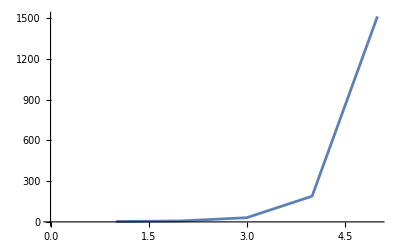

```mathematica
ListLinePlot[EikoOddDif/.y1->0]
```

## In the basis {cosh(x), G, dG/x}

-Graphics-
There are seveeral gobal parameters for the dimension
The Gobal parameter d defined in LiteRed
The Gobal parameter dim defined in KiHA (at the very beginning), which appears when one use SubFunctions
The Gobal parameter DD appears when one uses GlueAmp

Shorthand: y1 = v3.v4, y2 = a.a, y3 = b.b, y4 = b.a

The amplitude is supposed to have a generic form

```mathematica
CoeList=KroneckerProduct[{c[e,-1],c[e,0],c[e,1],c[o,0],c[o,1]},{c[e,-1],c[e,0],c[e,1],c[o,0],c[o,1]}]//Flatten//DeleteDuplicates
%//Length
```

{c[e,-1]^2,c[e,-1] c[e,0],c[e,-1] c[e,1],c[e,-1] c[o,0],c[e,-1] c[o,1],c[e,0]^2,c[e,0] c[e,1],c[e,0] c[o,0],c[e,0] c[o,1],c[e,1]^2,c[e,1] c[o,0],c[e,1] c[o,1],c[o,0]^2,c[o,0] c[o,1],c[o,1]^2}

15

### Amplitudes

on-shell spinless 4pt amp

```mathematica
M4Scalar[parSca_,parGon1_,parGon2_]:=-1/(2 dot[l[parGon1],l[parGon2]])(-dot[p[parSca],F[parGon1],F[parGon2],p[parSca]]/dot[p[parSca],l[parGon1]])^2
```

generic on-shell 3pt amp

```mathematica
M3Gen[parBH_,parGon_]:=1/M[parBH]^2 dot[p[parBH],ϵ[parGon]]^2(c[e,-1]Cosh[dot[l[parGon],a[parBH]]]+c[e,0] Sinh[dot[l[parGon],a[parBH]]]/dot[l[parGon],a[parBH]]+c[e,1](Cosh[dot[l[parGon],a[parBH]]]/dot[l[parGon],a[parBH]]^2-Sinh[dot[l[parGon],a[parBH]]]/dot[l[parGon],a[parBH]]^3))+1/M[parBH]^2 dot[p[parBH],ϵ[parGon]]dot[l[parGon],S[parBH],ϵ[parGon]](c[o,0] Sinh[dot[l[parGon],a[parBH]]]/dot[l[parGon],a[parBH]]+c[o,1](Cosh[dot[l[parGon],a[parBH]]]/dot[l[parGon],a[parBH]]^2-Sinh[dot[l[parGon],a[parBH]]]/dot[l[parGon],a[parBH]]^3))
```

The expression

```mathematica
M4Scalar[3,1,2]
```

-dot[p[3],F[1],F[2],p[3]]^2/(2 dot[l[1],l[2]] dot[l[1],p[3]]^2)

```mathematica
M3Gen[4,i1]
```

(dot[p[4],ϵ[i1]]^2 (c[e,-1] Cosh[dot[a[4],l[i1]]]+(c[e,0] Sinh[dot[a[4],l[i1]]])/dot[a[4],l[i1]]+c[e,1] (Cosh[dot[a[4],l[i1]]]/dot[a[4],l[i1]]^2-Sinh[dot[a[4],l[i1]]]/dot[a[4],l[i1]]^3)))/M[4]^2+(dot[p[4],ϵ[i1]] dot[l[i1],S[4],ϵ[i1]] ((c[o,0] Sinh[dot[a[4],l[i1]]])/dot[a[4],l[i1]]+c[o,1] (Cosh[dot[a[4],l[i1]]]/dot[a[4],l[i1]]^2-Sinh[dot[a[4],l[i1]]]/dot[a[4],l[i1]]^3)))/M[4]^2

### On-shell conditions and dot rules

not being used

```mathematica
n=4;
vponshell=vonshell[n-1,1]/.v->v[1];
gponshell=onshell[n-1];
```

```mathematica
vponshell
gponshell
```

vonshell[3,1]

onshell[3]

not being used

```mathematica
dotOnshell2={dot[p[i_],ϵ[i_]]:>0(*graviton momentum ⊥ polarization vector*),dot[p[i_],p[i_]]:>0/;i<3(*graviton momentum light-like*),dot[ϵ[i_],ϵ[i_]]:>0(*graviton polarization vector light-like*),dot[a[4],p[4]]->0(*SSC*),dot[a[5],p[5]]->0(*SSC*),dot[p[i_],p[5]]:>0/;i<3,dot[p[4],p[2]]->-dot[p[4],p[1]]};
gaugespinor={dot[p[2],ϵ[1]]->0,dot[p[1],ϵ[2]]->0};
dotOnshell2Graph1=dotOnshell2;
dotRulesHEFT={dot[a_,S[i_],a_]:>0,dot[a__,S[i_],b__]:>0/;{a,S[i],b}==Reverse[{a,S[i],b}]&&Length[{a}]==Length[{b}],dot[a__,F[i_],b__]:>0/;{a,F[i],b}==Reverse[{a,F[i],b}],dot[a__,H[i_],b__]:>0/;{a,H[i],b}==Reverse[{a,H[i],b}],dot[a__,F[i_],F[i_],b__]:>0,dot[a_,F[i_],a_]:>0,dot[a_,H[i_],a_]:>0,dot[a_,S[i_],b_]:>-dot[b,S[i],a]/;Sort[{a,b}]≠{a,b},dot[a_,F[i_],b_]:>-dot[b,F[i],a]/;Sort[{a,b}]≠{a,b},dot[a_,H[i_],b_]:>-dot[b,H[i],a]/;Sort[{a,b}]≠{a,b},dot[p[a_],F[a_],b__]:>0,dot[k[a_],F[a_],b__]:>0,dot[b__,F[a_],p[a_]]:>0,dot[b__,F[a_],k[a_]]:>0,dot[a__,H[i_],p[i_]]:>0,dot[p[i_],H[i_],a__]:>0,dot[b__,F[i_],H[i_],a__]:>0,dot[b__,H[i_],F[i_],a__]:>0,dot[a__,S[i_],v[i_]]:>0,dot[b__,S[i_],a[i_]]:>0,dot[a[i_],S[i_],b__]:>0,dot[a[i_],p[i_]]:>0,dot[a[i_],v[i_]]:>0,dot[v[i_],S[i_],a__]:>0,dot[a__,H[i_],ϵ[i_]]:>0,dot[ϵ[i_],H[i_],a__]:>0,dot[a__]:>(-1)^Length[{a}] dot@@Reverse[{a}]/;OrderedQ[{Reverse[{a}],{a}}]&&{a}=!=Reverse[{a}]};
```

On-shell conditions on the graviton cuts, to get rid of all unphysical/gauge terms (especially for ϵ) during the calculation, which is necessary for the uncompleted gluing formula.

```mathematica
ClearAll[onshellF,onshellFS]
(*onshellF={dot[g___,F[id_],F[id_],h___]:>0,dot[a_,F[i_],a_]:>0,dot[a__,F[i_],p[i_]]:>0,dot[p[i_],F[i_],a__]:>0,dot[p[id_],p[id_]]:>0/;id<3(*useless?*),tr[F[i_]]:>0,tr[S[i_]]:>0,tr[a_,F[i_],F[i_]]:>0,dot[a_,F[i_],b_]:>- dot[b,F[i],a]/;Sort[{a,b}]=!= {a,b}};*)
onshellFS={dot[g___,F[id_],F[id_],h___]:>0(*as p[id] is onshell*),dot[a_,F[i_],a_]:>0,dot[a__,F[i_],p[i_]]:>0,dot[p[i_],F[i_],a__]:>0,(*dot[p[id_],p[id_]]:>0/;id<3,*)tr[F[i_]]:>0,tr[S[i_]]:>0,tr[a_,F[i_],F[i_]]:>0,dot[a_,F[i_],b_]:>- dot[b,F[i],a]/;Sort[{a,b}]=!= {a,b}}~Join~{dot[a__,S[i_],p[i_]]->0,dot[p[i_],S[i_],a__]->0,dot[a_,S[i_],b_]:>- dot[b,S[i],a]/;Sort[{a,b}]=!= {a,b}};
(*massivecut:={dot[p[lo[1]],v[1]]->0,dot[p[lo[3]],v[1]]->0}*)
(*loopmrep:={p[lo[1]]->l[1],p[lo[2]]->q[1]-l[1]}
dotRules2={dot[a[0],S[1],b__]:>0,dot[a[1],S[0],b__]:>0,dot[b__,S[1],a[0]]:>0,dot[b__,S[0],a[1]]:>0,dot[a__,S[0],v[1]]:>0,dot[v[1],S[0],a__]:>0,dot[a[0],v[1]]:>0,dot[a[1],v[1]]:>0,dot[a[2],v[2]]:>0};*)
(*momentumconstraints:={dot[l[id_],l[id_]]:>0,dot[l[1],q[1]]:>1/2 dot[q[1]],dot[p[3],v[2]]->dot[q[1],v[2]],dot[p[id_],p[id_]]:>0}*)
```

### Glued amplitude (The propagators 1/l1.l1, 1/l2.l2, 1/l1.p4 are dismissed at this step, just so no 0 appears on the denominator after replacement)

For the amp to be glued: The to-glue gravitons are labelled by 1,2,3,.... with momenta p[1],p[2],p[3],...  Then change any to-glue graviton index i to p[i], e.g. F[1]->F[p[1]], p[1]->p[p[1]]

```mathematica
M4Scalar[3,1,2]/.{F[id_]->F[p[id]],l[id_]->p[p[id]]}
(M3Gen[4,1])(M3Gen[4,2])/.{l[id_]->p[p[id]],ϵ[id_]->ϵ[p[id]]}
```

-dot[p[3],F[p[1]],F[p[2]],p[3]]^2/(2 dot[p[3],p[p[1]]]^2 dot[p[p[1]],p[p[2]]])

((dot[p[4],ϵ[p[1]]]^2 (c[e,-1] Cosh[dot[a[4],p[p[1]]]]+(c[e,0] Sinh[dot[a[4],p[p[1]]]])/dot[a[4],p[p[1]]]+c[e,1] (Cosh[dot[a[4],p[p[1]]]]/dot[a[4],p[p[1]]]^2-Sinh[dot[a[4],p[p[1]]]]/dot[a[4],p[p[1]]]^3)))/M[4]^2+(dot[p[4],ϵ[p[1]]] dot[p[p[1]],S[4],ϵ[p[1]]] ((c[o,0] Sinh[dot[a[4],p[p[1]]]])/dot[a[4],p[p[1]]]+c[o,1] (Cosh[dot[a[4],p[p[1]]]]/dot[a[4],p[p[1]]]^2-Sinh[dot[a[4],p[p[1]]]]/dot[a[4],p[p[1]]]^3)))/M[4]^2) ((dot[p[4],ϵ[p[2]]]^2 (c[e,-1] Cosh[dot[a[4],p[p[2]]]]+(c[e,0] Sinh[dot[a[4],p[p[2]]]])/dot[a[4],p[p[2]]]+c[e,1] (Cosh[dot[a[4],p[p[2]]]]/dot[a[4],p[p[2]]]^2-Sinh[dot[a[4],p[p[2]]]]/dot[a[4],p[p[2]]]^3)))/M[4]^2+(dot[p[4],ϵ[p[2]]] dot[p[p[2]],S[4],ϵ[p[2]]] ((c[o,0] Sinh[dot[a[4],p[p[2]]]])/dot[a[4],p[p[2]]]+c[o,1] (Cosh[dot[a[4],p[p[2]]]]/dot[a[4],p[p[2]]]^2-Sinh[dot[a[4],p[p[2]]]]/dot[a[4],p[p[2]]]^3)))/M[4]^2)

The amplitude to be glued should be input as A[amp, {...}] where {...} are to-glue graviton indices. li[...] denotes the incoming momentum while lo[...] denotes the outgoing one. Note that in order to honestly replace graviton label j to li[j] (or lo[j]), one in {...} should write {li[1],li[2],...,li[j]} even there is no graviton 1,2,3,...,j-1 in the amplitude. For example, A[M3Pol[4, 2] /. {l[id_] -> p[p[id]], ϵ[id_] -> ϵ[p[id]]}, {li[1], li[2]}]. 
Then one writes GlueAmp[A[...], A[...], ...., li[j]] where li[j] is the graviton line to be glued in this running. One should run GlueAmp for every graviton line to be glued.

For convenience, one can also write GlueAmp[A[product of amplitudes with incoming momenta, {all incoming momentum indices}], A[product of amplitudes with outgoing momenta, {all outgoing momentum indices}], graviton line to be glued] such that the labelling of graviton lines are more natural.

```mathematica
intGen=GlueAmp[A[(M3Gen[4,1])(M3Gen[4,2])/.{l[id_]->p[p[id]],ϵ[id_]->ϵ[p[id]]},{li[1],li[2]}],A[M4Scalar[3,1,2]/.{F[id_]->F[p[id]],l[id_]->p[p[id]]},{lo[1],lo[2]}],li[1]];
```

If the gluing is successful, every p[j] should be replaced with li[j] or lo[j]

```mathematica
intGen//Length
intGen//Casesdot
```

315

{dot[a[4],p[li[1]]],dot[a[4],p[li[2]]],dot[p[3],p[3]],dot[p[3],p[4]],dot[p[3],p[lo[1]]],dot[p[4],p[4]],dot[p[4],ϵ[li[2]]],dot[p[lo[1]],p[lo[2]]],dot[p[3],F[lo[2]],p[3]],dot[p[4],F[lo[2]],p[3]],dot[p[li[1]],S[4],p[3]],dot[p[li[1]],S[4],p[4]],dot[p[li[2]],S[4],ϵ[li[2]]],dot[p[lo[1]],F[lo[2]],p[3]],dot[p[3],F[lo[2]],F[lo[2]],p[3]],dot[p[li[1]],S[4],F[lo[2]],p[3]]}

One should apply onshell conditions on the massless cuts  every time after GlueAmp, to get rid of all unphysical/gauge terms  during the calculation

```mathematica
intGen=intGen//.onshellFS;
```

```mathematica
intGen//Length
intGen//Casesdot
```

196

{dot[a[4],p[li[1]]],dot[a[4],p[li[2]]],dot[p[3],p[3]],dot[p[3],p[4]],dot[p[3],p[lo[1]]],dot[p[4],p[4]],dot[p[4],ϵ[li[2]]],dot[p[lo[1]],p[lo[2]]],dot[p[3],F[lo[2]],p[4]],dot[p[3],F[lo[2]],p[lo[1]]],dot[p[3],S[4],p[li[1]]],dot[p[li[2]],S[4],ϵ[li[2]]],dot[p[li[1]],S[4],F[lo[2]],p[3]]}

Glue the second graviton line. The A[...] format is needed only at the first time of GlueAmp. After that one just write GlueAmp[expr, li[j]]

```mathematica
intGen=GlueAmp[intGen,li[2]];
```

```mathematica
intGen//Casesdot
intGen//Length
```

{dot[a[4],p[li[1]]],dot[a[4],p[li[2]]],dot[p[3],p[3]],dot[p[3],p[4]],dot[p[3],p[lo[1]]],dot[p[3],p[lo[2]]],dot[p[4],p[4]],dot[p[4],p[lo[1]]],dot[p[4],p[lo[2]]],dot[p[lo[1]],p[lo[1]]],dot[p[lo[1]],p[lo[2]]],dot[p[3],S[4],p[li[1]]],dot[p[li[1]],S[4],p[3]],dot[p[li[1]],S[4],p[4]],dot[p[li[1]],S[4],p[lo[1]]],dot[p[li[1]],S[4],p[lo[2]]],dot[p[li[2]],S[4],p[3]],dot[p[li[2]],S[4],p[4]],dot[p[li[2]],S[4],p[lo[1]]],dot[p[li[1]],S[4],S[4],p[li[2]]]}

1329

```mathematica
intGen=intGen//.onshellFS;
```

```mathematica
intGen//Casesdot
intGen//Length
```

{dot[a[4],p[li[1]]],dot[a[4],p[li[2]]],dot[p[3],p[3]],dot[p[3],p[4]],dot[p[3],p[lo[1]]],dot[p[3],p[lo[2]]],dot[p[4],p[4]],dot[p[4],p[lo[1]]],dot[p[4],p[lo[2]]],dot[p[lo[1]],p[lo[1]]],dot[p[lo[1]],p[lo[2]]],dot[p[3],S[4],p[li[1]]],dot[p[3],S[4],p[li[2]]],dot[p[li[1]],S[4],p[lo[1]]],dot[p[li[1]],S[4],p[lo[2]]],dot[p[li[2]],S[4],p[lo[1]]],dot[p[li[1]],S[4],S[4],p[li[2]]]}

894

Impose all dot conditions

```mathematica
(*impose the incoming/outgoing momentum signs based on the definition of the amplitude diagram*)
intGen=intGen/.{p[lo[2]]->p[2],p[li[2]]->-p[2],p[li[1]]->-p[1],p[lo[1]]->p[1]};
(*on-shell conditions for external momenta and on-cut momenta*)intGen=intGen/.{dot[p[i_],p[i_]]/;i<=2->0 ,dot[p[i_],p[i_]]/;i>=3->M[i]^2}//.dotRules(*dot conditions for F,H,S,a*);
(*on-shell conditions plus heavy-mass conditions*)
intGen=intGen/.{dot[p[4],p[1]]->0,dot[p[4],p[2]]->0}/.{dot[p[3],p[2]]->-dot[p[3],p[1]]};
```

```mathematica
intGen//Casesdot
intGen//Length
```

{dot[a[4],p[1]],dot[a[4],p[2]],dot[p[1],p[2]],dot[p[1],p[3]],dot[p[3],p[4]],dot[p[1],S[4],p[2]],dot[p[1],S[4],p[3]],dot[p[2],S[4],p[3]],dot[p[1],S[4],S[4],p[2]]}

322

Transform even products of S tensors into metric, and apply dot conditions again

```mathematica
intGen=intGen//expandSS//Expand;
```

```mathematica
(*impose the incoming/outgoing momentum signs based on the definition of the amplitude diagram*)
intGen=intGen/.{p[lo[2]]->p[2],p[li[2]]->-p[2],p[li[1]]->-p[1],p[lo[1]]->p[1]};
(*on-shell conditions for external momenta and on-cut momenta*)intGen=intGen/.{dot[p[i_],p[i_]]/;i<=2->0 ,dot[p[i_],p[i_]]/;i>=3->M[i]^2}//.dotRules(*dot conditions for F,H,S,a*);
(*on-shell conditions plus heavy-mass conditions*)
intGen=intGen/.{dot[p[4],p[1]]->0,dot[p[4],p[2]]->0}/.{dot[p[3],p[2]]->-dot[p[3],p[1]]};
(*a^2 condition and aligned-spin condition*)
intGen=intGen/.{dot[a[4],p[3]]->0,dot[a[4],p[4]]->0};
```

```mathematica
intGen//Casesdot
intGen//Length
```

{dot[a[4],a[4]],dot[a[4],p[1]],dot[a[4],p[2]],dot[p[1],p[2]],dot[p[1],p[3]],dot[p[3],p[4]],dot[p[1],S[4],p[2]],dot[p[1],S[4],p[3]],dot[p[2],S[4],p[3]]}

401

Apply MultivariateApart to simplify (maybe)

```mathematica
intGen=intGen//MultivariateApart;
```

```mathematica
intGen//Casesdot
intGen//Length
```

{dot[a[4],a[4]],dot[a[4],p[1]],dot[a[4],p[2]],dot[p[1],p[2]],dot[p[1],p[3]],dot[p[3],p[4]],dot[p[1],S[4],p[2]],dot[p[1],S[4],p[3]],dot[p[2],S[4],p[3]]}

185

```mathematica
intGen>>"int.m"
```

```mathematica
intGen=<<"int.m";
```

Get::noopen: Cannot open int.m.

### Transfer and spin expansion prepared for IBP Load the spin-expanded integrand here

#### Transform to basis {v3,v4,q,v0} and eps to dot

Select a basis {v3,v4,q,v0} where v0 = eps[v3,v4,q,...], to expand vec to this basis and change all eps’s to dots 
The results will be in terms of vec.v3, vec.v4, vec.q, vec.v0.  l1.v0 and a4.v0 will be handled later.

```mathematica
ClearAll[a2basis]
a2basis[f_,vec_]:=Module[{vecs,onshellheftTT,eq2s,solcqImpactWFt,q2SymImpactWFt,onshellheftq1,c},vecs={v[3],v[4],v[0],q[1]};
onshellheftq1={dot[v[3],v[4]]->y,dot[v[i_],v[i_]]:>1/;i>0,dot[v[0],v[i_]]:>0/;i>0,dot[v[0],v[0]]:>(-1+y^2) dot[q[1],q[1]] ,dot[q[1],v[3]]:>0,dot[q[1],v[4]]:>0,dot[q[1],v[0]]:>0};
onshellheftTT=Join[onshellheftq1,{}(*solup,*)];
eq2s=Table[Equal@@(dot[#,vecs[[ii]]]&/@{vec,Sum[c[ii]vecs[[ii]],{ii,4}]}),{ii,Length@vecs}]/.onshellheftTT;
solcqImpactWFt=(Solve[eq2s,{c[1],c[2],c[3],c[4]}][[1]]//Simplify)/.onshellheftTT//Simplify;
q2SymImpactWFt=Sum[c[ii]vecs[[ii]],{ii,4}];(f/.{vec->q2SymImpactWFt}/.solcqImpactWFt/.onshellheftTT)//Simplify]
onshellheftq1={dot[v[3],v[4]]->y,dot[v[i_],v[i_]]:>1/;i>0,dot[v[0],v[i_]]:>0/;i>0,dot[v[0],v[0]]:>(-1+y^2) dot[q[1],q[1]] ,dot[q[1],v[3]]:>0,dot[q[1],v[4]]:>0,dot[q[1],v[0]]:>0};
```

```mathematica
(dot[a[4],l[1]]//a2basis[#,l[1]]&//a2basis[#,a[4]]&)/.eps[q[1],v[0],v[3],v[4]]->(-1+y^2) dot[q[1],q[1]]/.dot[l[1],q[1]]->1/2 dot[q[1],q[1]]/.{dot[v[3],a[4]]->0,dot[v[4],a[4]]->0}(*aligned spin*)
```

(dot[a[4],v[0]] dot[l[1],v[0]]+1/2 (-1+y^2) dot[a[4],q[1]] dot[q[1],q[1]])/((-1+y^2) dot[q[1],q[1]])

```mathematica
(eps[a[4],l[1],q[1],v[4]]//a2basis[#,l[1]]&//a2basis[#,a[4]]&)/.eps[q[1],v[0],v[3],v[4]]->(-1+y^2) dot[q[1],q[1]]/.dot[l[1],q[1]]->1/2 dot[q[1],q[1]]/.{dot[v[3],a[4]]->0,dot[v[4],a[4]]->0}(*aligned spin*)/.dot[l[1],v[4]]->0
```

-(dot[a[4],v[0]] dot[l[1],v[3]])/(-1+y^2)

```mathematica
(eps[a[4],l[1],v[3],v[4]]//a2basis[#,l[1]]&//a2basis[#,a[4]]&)/.eps[q[1],v[0],v[3],v[4]]->(-1+y^2) dot[q[1],q[1]]/.dot[l[1],q[1]]->1/2 dot[q[1],q[1]]/.{dot[v[3],a[4]]->0,dot[v[4],a[4]]->0}(*aligned spin*)/.dot[l[1],v[4]]->0
```

(dot[a[4],q[1]] dot[l[1],v[0]]-1/2 dot[a[4],v[0]] dot[q[1],q[1]])/dot[q[1],q[1]]

```mathematica
(eps[a[4],q[1],v[3],v[4]]//a2basis[#,l[1]]&//a2basis[#,a[4]]&)/.eps[q[1],v[0],v[3],v[4]]->(-1+y^2) dot[q[1],q[1]]/.dot[l[1],q[1]]->1/2 dot[q[1],q[1]]/.{dot[v[3],a[4]]->0,dot[v[4],a[4]]->0}(*aligned spin*)/.dot[l[1],v[4]]->0
```

-dot[a[4],v[0]]

```mathematica
ToBasis={dot[a[4],l[1]]->(dot[a[4],v[0]] dot[l[1],v[0]]+1/2 (-1+y^2) dot[a[4],q[1]] dot[q[1],q[1]])/((-1+y^2) dot[q[1],q[1]]), eps[a[4],l[1],q[1],v[4]]->-(dot[a[4],v[0]] dot[l[1],v[3]])/(-1+y^2), eps[a[4],l[1],v[3],v[4]]->(dot[a[4],q[1]] dot[l[1],v[0]]-1/2 dot[a[4],v[0]] dot[q[1],q[1]])/dot[q[1],q[1]], eps[a[4],q[1],v[3],v[4]]->-dot[a[4],v[0]]};
```

Simplify dot[b[1], S[4], v[3]]  by taking square

```mathematica
M[4]eps[v[4],a[4],b[1],v[3]]M[4]eps[v[4],a[4],b[1],v[3]]//expandEps;
%/.{dot[v[4],v[4]]->1,dot[v[3],v[3]]->1}/.{dot[v[4],a[4]]->0,dot[v[3],a[4]]->0,dot[a[4],b[1]]->0,dot[v[3],b[1]]->0,dot[v[4],b[1]]->0}/.{dot[v[3],v[4]]->y1,dot[a[4],a[4]]->y2,dot[b[1],b[1]]->y3}//Simplify
```

(-1+y1^2) y2 y3 M[4]^2

#### IBP preparation

Here we use S^μν=ϵ^μνρσ p_ρ a_σ (different from that in 2406.09086)

```mathematica
intGen=intGen/.{dot[b1_,S[i_],b2_]:>M[i] eps[v[i],a[i],b1,b2]}/.{p[4]->M[4]v[4],p[3]->M[3]v[3]}//Expand;
```

```mathematica
CoeList=KroneckerProduct[{c[e,-1],c[e,0],c[e,1],c[o,0],c[o,1]},{c[e,-1],c[e,0],c[e,1],c[o,0],c[o,1]}]//Flatten//DeleteDuplicates
%//Length
```

{c[e,-1]^2,c[e,-1] c[e,0],c[e,-1] c[e,1],c[e,-1] c[o,0],c[e,-1] c[o,1],c[e,0]^2,c[e,0] c[e,1],c[e,0] c[o,0],c[e,0] c[o,1],c[e,1]^2,c[e,1] c[o,0],c[e,1] c[o,1],c[o,0]^2,c[o,0] c[o,1],c[o,1]^2}

15

```mathematica
Clear[intGenIBP]
Table[intGenIBP[ii]=intGen//Coefficient[#,ii]&,
{ii,CoeList}];
```

Spin expansion up to a[4]^21

```mathematica
Clear[intGenIBPexpand]
Table[intGenIBPexpand[ii]=intGenIBP[ii]/.{a[4]->t a[4]}//Series[#,{t,0,21}]&//Normal//Expand,{ii,CoeList}];
```

The manipulation about l1 should be done after the spin expansion (which expands cosh(l1.a4)...)

```mathematica
Table[intGenIBPexpand[ii]=intGenIBPexpand[ii]/.{p[1]->l[1],p[2]->q[1]-l[1]}/.{dot[l[1],l[1]]->0,dot[l[1],q[1]]->1/2 dot[q[1],q[1]](*From l1.q=l1.l2 on massless cuts*)},{ii,CoeList}];
```

```mathematica
intGenIBPexpand[c[e,-1]c[o,0]]//Casesdot
```

{}

```mathematica
Table[intGenIBPa[ii][nn]=Which[nn==0,(intGenIBPexpand[ii]/.t->0),nn>=1,Coefficient[intGenIBPexpand[ii],t^nn] ],{ii,CoeList},{nn,0,21}];
```

```mathematica
intGenIBPaList=Table[intGenIBPa[ii][nn],{ii,CoeList},{nn,0,11}];
SaveToCell[intGenIBPaList]
```

```mathematica
intGenIBPaList="data";
```

```mathematica
intGenIBPaList="data";
```

```mathematica
Table[intGenIBPa[CoeList[[ii]]][nn]=intGenIBPaList[[ii,nn+1]],{ii,CoeList//Length},{nn,0,11}];
```

#### IBP preparation, at a generic spin order

Here we use S^μν=ϵ^μνρσ p_ρ a_σ (different from that in 2406.09086)

```mathematica
intGen=intGen/.{dot[b1_,S[i_],b2_]:>M[i] eps[v[i],a[i],b1,b2]}/.{p[4]->M[4]v[4],p[3]->M[3]v[3]}//Expand;
```

```mathematica
Clear[intGenIBP]
Table[intGenIBP[ii]=intGen//Coefficient[#,ii]&,
{ii,CoeList}];
```

```mathematica
intGenIBPaG[c[e,0]c[e,0]]=Assuming[{ao>=0},(intGenIBP[c[e,0]c[e,0]]/.{a[4]->t a[4]}//SeriesCoefficient[#,{t,0,ao}]&)]/.{p[1]->l[1],p[2]->q[1]-l[1]}/.{dot[l[1],l[1]]->0,dot[l[1],q[1]]->1/2 dot[q[1],q[1]](*From l1.q=l1.l2 on massless cuts*)}/.{(-2 dot[a[4],l[1]]+dot[a[4],q[1]])^(2+ao)->(2 dot[a[4],l[1]]-dot[a[4],q[1]])^(2+ao),(-dot[a[4],q[1]])^(2+ao)->dot[a[4],q[1]]^(2+ao)}(*since ao is even*);
```

```mathematica
Collect[intGenIBPaG[c[e,0]c[e,0]],{(2 dot[a[4],l[1]]-dot[a[4],q[1]])^(2+ao)/(dot[a[4],l[1]] (-dot[a[4],l[1]]+dot[a[4],q[1]])),dot[a[4],q[1]]^(2+ao)/(dot[a[4],l[1]] (-dot[a[4],l[1]]+dot[a[4],q[1]]))}]
Coefficient[intGenIBPaG[c[e,0]c[e,0]], (2 dot[a[4],l[1]]-dot[a[4],q[1]])^(2+ao)]+Coefficient[intGenIBPaG[c[e,0]c[e,0]], dot[a[4],q[1]]^(2+ao)]
```

0

0

```mathematica
expr=((2 dot[a[4],l[1]]-dot[a[4],q[1]])^(2+ao) -dot[a[4],q[1]]^(2+ao) )/(dot[a[4],l[1]] (-dot[a[4],l[1]]+dot[a[4],q[1]]))(M[3]^2/(2 (-2+DD)^2 (2+ao)!)+(dot[l[1],v[3]]^2 M[3]^2)/(2 dot[q[1],q[1]] (2+ao)!)-(dot[l[1],v[3]]^2 M[3]^2)/(2 (-2+DD) dot[q[1],q[1]] (2+ao)!)+(dot[q[1],q[1]] M[3]^2)/(8 (-2+DD)^2 dot[l[1],v[3]]^2 (2+ao)!)-(dot[v[3],v[4]]^2 M[3]^2)/(2 (2+ao)!)-(dot[q[1],q[1]] dot[v[3],v[4]]^2 M[3]^2)/(4 (-2+DD) dot[l[1],v[3]]^2 (2+ao)!)+(dot[q[1],q[1]] dot[v[3],v[4]]^4 M[3]^2)/(8 dot[l[1],v[3]]^2 (2+ao)!));
expr-intGenIBPaG[c[e,0]c[e,0]]//Simplify
```

-(((4 dot[a[4],l[1]]^2 (2 dot[a[4],l[1]]-dot[a[4],q[1]])^ao-4 dot[a[4],l[1]] (2 dot[a[4],l[1]]-dot[a[4],q[1]])^ao dot[a[4],q[1]]+dot[a[4],q[1]]^2 ((2 dot[a[4],l[1]]-dot[a[4],q[1]])^ao-dot[a[4],q[1]]^ao)) (4 (6-5 DD+DD^2) dot[l[1],v[3]]^4+dot[q[1],q[1]]^2 (-1+(-2+DD) dot[v[3],v[4]]^2)^2-4 dot[l[1],v[3]]^2 dot[q[1],q[1]] (-1+(-2+DD)^2 dot[v[3],v[4]]^2)) M[3]^2)/(8 (-2+DD)^2 dot[a[4],l[1]] (dot[a[4],l[1]]-dot[a[4],q[1]]) dot[l[1],v[3]]^2 dot[q[1],q[1]] (2+ao)!))

```mathematica
factor[ao_?EvenQ]:=-2/dot[a[4],l[1]] Sum[dot[a[4],q[1]]^k Sum[Binomial[ao+2-1-k,i](2dot[a[4],l[1]])^(ao+2-1-k-i)(-dot[a[4],q[1]])^i,{i,0,ao+2-1-k}],{k,0,ao+2-1}]
```

Terms with dot[a[4],l[1]] on the denominator cancel out

```mathematica
summand=-2/dot[a[4],l[1]] dot[a[4],q[1]]^k Binomial[ao+2-1-k,i](2dot[a[4],l[1]])^(ao+2-1-k-i)(-dot[a[4],q[1]])^i(M[3]^2/(2 (-2+DD)^2 (2+ao)!)+(dot[l[1],v[3]]^2 M[3]^2)/(2 dot[q[1],q[1]] (2+ao)!)-(dot[l[1],v[3]]^2 M[3]^2)/(2 (-2+DD) dot[q[1],q[1]] (2+ao)!)+(dot[q[1],q[1]] M[3]^2)/(8 (-2+DD)^2 dot[l[1],v[3]]^2 (2+ao)!)-(dot[v[3],v[4]]^2 M[3]^2)/(2 (2+ao)!)-(dot[q[1],q[1]] dot[v[3],v[4]]^2 M[3]^2)/(4 (-2+DD) dot[l[1],v[3]]^2 (2+ao)!)+(dot[q[1],q[1]] dot[v[3],v[4]]^4 M[3]^2)/(8 dot[l[1],v[3]]^2 (2+ao)!));
```

```mathematica
ToBasis
```

{dot[a[4],l[1]]→(dot[a[4],v[0]] dot[l[1],v[0]]+1/2 (-1+y^2) dot[a[4],q[1]] dot[q[1],q[1]])/((-1+y^2) dot[q[1],q[1]]),eps[a[4],l[1],q[1],v[4]]→-(dot[a[4],v[0]] dot[l[1],v[3]])/(-1+y^2),eps[a[4],l[1],v[3],v[4]]→(dot[a[4],q[1]] dot[l[1],v[0]]-1/2 dot[a[4],v[0]] dot[q[1],q[1]])/dot[q[1],q[1]],eps[a[4],q[1],v[3],v[4]]→-dot[a[4],v[0]]}

The dot[a[4],l[1]] (-dot[a[4],l[1]]+dot[a[4],q[1]]) on the denominator are gone at each spin order, and only dot[l[1],v[3]] and dot[q[1],q[1]] appear

```mathematica
intGenIBPaG[c[e,0]c[e,0]]/.ao->0//Simplify//Expand
intGenIBPaG[c[e,0]c[e,0]]/.ao->2//Simplify//Expand
intGenIBPaG[c[e,0]c[e,0]]/.ao->4//Simplify//Expand
```

0

0

0

### Generate IBP (l1.v0 needed) No l1.v0: No epsilon at a^even. Only one epsilon at a^odd but that should becomes S combining with a

Declare all vectors and numbers appearing. The numbers are those independent of the loop integral.
l1 is the loop momentum. qq is the transfer momentum. x = qq^2, y = v3.v4

```mathematica
SetDim[d];
Declare[{l1,v3,v4,qq},Vector,{x,y},Number]
```

Impose all the dot rules--on-shell conditions (on the massive/massless cuts), heavy mass conditions  and the declared Number’s. Dot rules involving loop momenta are excluded.

```mathematica
SetConstraints[{v3,v4,qq},
sp[v3,v3]=1; sp[v4,v4]=1; sp[v4,qq]=0; sp[v3,qq]=0;sp[qq,qq]=x; sp[v3,v4]=y;
]
```

Executing
qq·qq=x;qq·v3=0;qq·v4=0;v3·v3=1;v3·v4=y;v4·v4=1;

Q7. How does this work?

```mathematica
SetOptions[SolvejSector,{UseFermat->False,NMIs->Automatic}];
```

The complete set of dots involving loop momenta. Here one has {l1.l1, l1.v3, l1,v4, l1.q} so one has to select four basis dots. But note that those appearing as propagators must be selected. Here are l1.l1, (q-l1).(q-l1).

```mathematica
Clear[dsSpSc1L]
```

```mathematica
dsSpSc1L={sp[l1,v3],sp[l1,v4],sp[l1,l1],sp[qq-l1,qq-l1]}
```

{l1·v3,l1·v4,l1·l1,(-l1+qq)·(-l1+qq)}

Generate IBP. 1’s in CutDs means the associated dots are in the delta function (here is l1.v4 in the massive cut). SectorsPatern tells which dot can appear only on the numerator (here all dots can appear in the denominator).

```mathematica
Clear[SpSc1L]
NewDsBasis[SpSc1L,dsSpSc1L,{l1},CutDs->{0,1,0,0},Directory->"IBP_SpinScalar_OneLoop",SectorsPattern->{__}, SolvejSector->True(*,jsOrder->{"np","-ds","-ns"}*)]
```

SpSc1L is valid basis. The definitions of the basis will be saved in "IBP_SpinScalar_OneLoop" directory.
    Ds[SpSc1L] — denominators,
    SPs[SpSc1L] — scalar products involving loop momenta,
    LMs[SpSc1L] — loop momenta,
    EMs[SpSc1L] — external momenta,
    Parameters[SpSc1L] — parameters (invariants, masses, dimension),
    Toj[SpSc1L] — rules to transform scalar products to denominators,
    CutDs[SpSc1L] — flag vector of cut denominators.

The directory IBP_SpinScalar_OneLoop has been created.

Generating IBP…

Identities are generated.
    IBP[SpSc1L] — integration-by-part identities,
    LI[SpSc1L] — Lorentz invariance identities.

Analyzing sectors…

Found 14(2) zero(nonzero) sectors out of 16.
    ZeroSectors[SpSc1L] — zero sectors,
    NonZeroSectors[SpSc1L] — nonzero sectors,
    SimpleSectors[SpSc1L] — simple sectors (no nonzero subsectors),
    BasisSectors[SpSc1L] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[SpSc1L] — a rule to nullify all zero j[SpSc1L…],
    CutDs[SpSc1L] — a flag list of cut denominators (1=cut).

Finding symmetries…

Found 0 mapped sectors and 2 unique sectors.
    UniqueSectors[SpSc1L] — unique sectors.
    MappedSectors[SpSc1L] — mapped sectors.
    SR[SpSc1L][…] — symmetry relations for j[SpSc1L,…] from UniqueSectors[SpSc1L].
    jSymmetries[SpSc1L,…] — symmetry rules for the sector js[SpSc1L,…] in UniqueSectors[SpSc1L].
    jRules[SpSc1L,…] — reduction rules for j[SpSc1L,…] from MappedSectors[SpSc1L].
    SectorsMappings[SpSc1L] gives the list of mappings of all sectors from MappedSectors[SpSc1L] to UniqueSectors[SpSc1L].

Solving sectors…

About to solve 2 unique sectors of SpSc1L basis.

Sector js[SpSc1L,0,1,1,1]

Finished in 0 seconds.
    jRules[SpSc1L, 0, 1, 1, 1] — reduction rules for the sector.
    MIs[SpSc1L] — list of master integrals appended with 1 integrals (j[SpSc1L, 0, 1, 1, 1]).

Sector js[SpSc1L,1,1,1,1]

Finished in 0 seconds.
    jRules[SpSc1L, 1, 1, 1, 1] — reduction rules for the sector.
    MIs[SpSc1L] — list of master integrals appended with 1 integrals (j[SpSc1L, 1, 1, 1, 1]).

SpSc1L

Load the IBP from the saved data

```mathematica
SetDim[d];(*d stands for the dimensionality*)
Declare[{l1,v3,v4,qq},Vector,{x,y},Number];(*vector variables*)
<<"IBP_SpinScalar_OneLoop/SpSc1L";(*Load the basis*)
```

CheckDefinitions::warn: Some external definitions used in 'SpSc1L' basis are missing. Probably, you should run ExecuteDefinitions[SpSc1L].

```mathematica
ExecuteDefinitions[SpSc1L]
```

Condition qq·qq===x is not satisfied. Executing qq·qq=x.

Condition v3·v3===1 is not satisfied. Executing v3·v3=1.

Condition v4·v4===1 is not satisfied. Executing v4·v4=1.

Condition qq·v3===0 is not satisfied. Executing qq·v3=0.

Condition qq·v4===0 is not satisfied. Executing qq·v4=0.

Condition v3·v4===y is not satisfied. Executing v3·v4=y.

```mathematica
j[SpSc1L,1,2,1,1]+j[SpSc1L,1,1,1,2]//IBPReduce
Collectj[%,Factor]
```

-(4 (4-d) y j[SpSc1L,0,1,1,1])/(x (-1+y) (1+y))+((5-d) j[SpSc1L,1,1,1,1])/x

-(4 (4-d) y j[SpSc1L,0,1,1,1])/(x (-1+y) (1+y))+((5-d) j[SpSc1L,1,1,1,1])/x

Q. Why?

```mathematica
j[vv,1,-1,1,2]//IBPReduce
j[vv,1,0,1,2]//IBPReduce
j[vv,1,1,1,2]//IBPReduce
j[vv,1,2,1,2]//IBPReduce
j[vv,1,3,1,2]//IBPReduce
```

0

0

((5-d) j[vv,1,1,1,1])/x

-y ((4 (4-d))/(x^2 (-1+y) (1+y))+(4 (4-d) (5-d))/(x^2 (-1+y) (1+y))) j[vv,0,1,1,1]

(((5-d) (6-d) (7-d))/(2 x^2)+y^2 ((2 (5-d))/(x^2 (-1+y) (1+y))+(2 (5-d) (6-d))/(x^2 (-1+y) (1+y)))-x (((5-d) (6-d) (7-d))/(2 x^3)+((-1+y) (1+y) ((2 (5-d))/(x^2 (-1+y) (1+y))+(2 (5-d) (6-d))/(x^2 (-1+y) (1+y))))/x)) j[vv,1,1,1,1]

### IBP reduction

#### generic

One has to do Simplify before expandEps to kill all odd orders of  l1.v0. For efficiency, it is better to Simplify order by order of a.
One has to consider the sum cL[id1__]cR[id2__]+cL[id2__]cR[id1__] where the odd order of l1.v0 cancels out. This is also reasonable for a product of two amplitudes for the same object--if a term appears in the left amp, it must also appear in the right amp. So the complete contribution from terms id1,id2 needs that sum.

```mathematica
Timing[Table[intGenIBP2Ba[ii][nn]=((intGenIBPa[ii][nn]//.ToBasis//Simplify//Expand)(*to basis {v3,v4,q,v0}*)
/.dot[aa_,v[0]]->eps[v[3],v[4],q[1],aa]//expandEps)(*replace eps's*)
/.{dot[v[3],v[3]]->1,dot[v[4],v[4]]->1,dot[l[1],l[1]]->0,dot[l[1],q[1]]->1/2 dot[q[1],q[1]],dot[l[1],v[4]]->0}/.{dot[q[1],v[3]]->0,dot[q[1],v[4]]->0}/.{dot[a[4],v[3]]->0,dot[a[4],v[4]]->0}/. eps[a[4],q[1],v[3],v[4]]->-1/M[4]dot[q[1],S[4],v[3]](*onshell conditions on cuts*),{ii,CoeList}
,{nn,0,21}];]
```

$Aborted

```mathematica
Table[Print[intGenIBP2Ba[CoeList[[15]]][nn]//Casesdot],{nn,0,11}];
```

{}

{}

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]]}

{}

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]]}

{}

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]]}

{}

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]]}

{}

{dot[a[4],a[4]],dot[a[4],q[1]],dot[l[1],v[3]],dot[q[1],q[1]],dot[v[3],v[4]]}

{}

```mathematica
intGenIBP2BaList=Table[intGenIBP2Ba[ii][nn],{ii,CoeList},{nn,0,11}];
SaveToCell[intGenIBP2BaList]
```

```mathematica
intGenIBP2BaList="data";
```

```mathematica
Table[intGenIBP2Ba[CoeList[[ii]]][nn]=intGenIBP2BaList[[ii,nn+1]],{ii,CoeList//Length},{nn,0,11}];
```

```mathematica
Clear[intGenJa]
Timing[
Table[
Which[intGenIBP2Ba[ii][nn]===0,intGenJa[ii][nn]=0,True,
vars=intGenIBP2Ba[ii][nn]//Casesdot//Cases[#,dot[aa__]/;MemberQ[List[aa],l[1]]]&;
dotIBPlist=GenIBPdotList[intGenIBP2Ba[ii][nn],vars];
intGenJa[ii][nn]=mono2j[intGenIBP2Ba[ii][nn],dotIBPlist,vars];]
,{ii,CoeList},{nn,0,11}];
]
```

{82.75,Null}

```mathematica
intGenJaList=Table[intGenJa[ii][nn],{ii,CoeList},{nn,0,11}];
SaveToCell[intGenJaList]
```

```mathematica
intGenJaList="data";
```

```mathematica
Clear[intGenJaRed]
Timing[
Table[
intGenJaRed[ii][nn]=(intGenJa[ii][nn]/.j[gr1,jj__]->j[SpSc1L,jj,1,1,1]/.{dim->d,DD->d,dot[q[1],q[1]]->x,dot[v[3],v[4]]->y}//IBPReduce)/.d->4//Simplify;
,{ii,CoeList},{nn,0,11}];
]
```

Put::noopen: 无法打开 IBPReduction8\res.

DeleteDirectory::ioarg: I/O 操作对 IBPReduction8 无效.

Put::noopen: 无法打开 IBPReduction9\res.

DeleteDirectory::ioarg: I/O 操作对 IBPReduction9 无效.

DeleteDirectory::ioarg: I/O 操作对 IBPReduction10 无效.

General::stop: 在本次计算中，DeleteDirectory::ioarg 的进一步输出将被抑制.

{12.75,Null}

```mathematica
intGenJaRedList=Table[intGenJaRed[ii][nn],{ii,CoeList},{nn,0,11}];
SaveToCell[intGenJaRedList]
```

```mathematica
intGenJaRedList="data";
```

```mathematica
Table[intGenJaRed[CoeList[[ii]]][nn]=intGenJaRedList[[ii,nn+1]],{ii,CoeList//Length},{nn,0,11}];
```

#### For c[e,0]c[e,0]

```mathematica
Timing[Table[intGenIBP2Ba[c[e,0]c[e,0]][nn]=((intGenIBPa[c[e,0]c[e,0]][nn]//.ToBasis//Simplify//Expand)(*to basis {v3,v4,q,v0}*)
/.dot[aa_,v[0]]->eps[v[3],v[4],q[1],aa]//expandEps)(*replace eps's*)
/.{dot[v[3],v[3]]->1,dot[v[4],v[4]]->1,dot[l[1],l[1]]->0,dot[l[1],q[1]]->1/2 dot[q[1],q[1]],dot[l[1],v[4]]->0}/.{dot[q[1],v[3]]->0,dot[q[1],v[4]]->0}/.{dot[a[4],v[3]]->0,dot[a[4],v[4]]->0}/. eps[a[4],q[1],v[3],v[4]]->-1/M[4]dot[q[1],S[4],v[3]](*onshell conditions on cuts*)
,{nn,0,21}];]
```

{63.2656,Null}

```mathematica
Timing[
Table[
Which[intGenIBP2Ba[c[e,0]c[e,0]][nn]===0,intGenJa[c[e,0]c[e,0]][nn]=0,True,
vars=intGenIBP2Ba[c[e,0]c[e,0]][nn]//Casesdot//Cases[#,dot[aa__]/;MemberQ[List[aa],l[1]]]&;
dotIBPlist=GenIBPdotList[intGenIBP2Ba[c[e,0]c[e,0]][nn],vars];
intGenJa[c[e,0]c[e,0]][nn]=mono2j[intGenIBP2Ba[c[e,0]c[e,0]][nn],dotIBPlist,vars];]
,{nn,0,21}];
]
```

{198.125,Null}

```mathematica
Timing[
Table[
intGenJaRed[c[e,0]c[e,0]][nn]=(intGenJa[c[e,0]c[e,0]][nn]/.j[gr1,jj__]->j[SpSc1L,jj,1,1,1]/.{dim->d,DD->d,dot[q[1],q[1]]->x,dot[v[3],v[4]]->y}//IBPReduce)/.d->4//Simplify;
,{nn,0,21}];
]
```

DeleteDirectory::ioarg: I/O 操作对 IBPReduction15 无效.

DeleteDirectory::ioarg: I/O 操作对 IBPReduction16 无效.

{12.3906,Null}

#### For j[...,m,1,1,1] m>0

```mathematica
tp=Table[{j[SpSc1L,m,1,1,1]//IBPReduce//Factor,m},{m,0,17}]
```

{{j[SpSc1L,0,1,1,1],0},{j[SpSc1L,1,1,1,1],1},{-(4 (-4+d) j[SpSc1L,0,1,1,1])/(x (-1+y) (1+y)),2},{-(2 (-5+d) j[SpSc1L,1,1,1,1])/(x (-1+y) (1+y)),3},{(16 (-6+d) (-4+d) j[SpSc1L,0,1,1,1])/(3 x^2 (-1+y)^2 (1+y)^2),4},{(2 (-7+d) (-5+d) j[SpSc1L,1,1,1,1])/(x^2 (-1+y)^2 (1+y)^2),5},{-(64 (-8+d) (-6+d) (-4+d) j[SpSc1L,0,1,1,1])/(15 x^3 (-1+y)^3 (1+y)^3),6},{-(4 (-9+d) (-7+d) (-5+d) j[SpSc1L,1,1,1,1])/(3 x^3 (-1+y)^3 (1+y)^3),7},{(256 (-10+d) (-8+d) (-6+d) (-4+d) j[SpSc1L,0,1,1,1])/(105 x^4 (-1+y)^4 (1+y)^4),8},{(2 (-11+d) (-9+d) (-7+d) (-5+d) j[SpSc1L,1,1,1,1])/(3 x^4 (-1+y)^4 (1+y)^4),9},{-(1024 (-12+d) (-10+d) (-8+d) (-6+d) (-4+d) j[SpSc1L,0,1,1,1])/(945 x^5 (-1+y)^5 (1+y)^5),10},{-(4 (-13+d) (-11+d) (-9+d) (-7+d) (-5+d) j[SpSc1L,1,1,1,1])/(15 x^5 (-1+y)^5 (1+y)^5),11},{(4096 (-14+d) (-12+d) (-10+d) (-8+d) (-6+d) (-4+d) j[SpSc1L,0,1,1,1])/(10395 x^6 (-1+y)^6 (1+y)^6),12},{(4 (-15+d) (-13+d) (-11+d) (-9+d) (-7+d) (-5+d) j[SpSc1L,1,1,1,1])/(45 x^6 (-1+y)^6 (1+y)^6),13},{-(16384 (-16+d) (-14+d) (-12+d) (-10+d) (-8+d) (-6+d) (-4+d) j[SpSc1L,0,1,1,1])/(135135 x^7 (-1+y)^7 (1+y)^7),14},{-(8 (-17+d) (-15+d) (-13+d) (-11+d) (-9+d) (-7+d) (-5+d) j[SpSc1L,1,1,1,1])/(315 x^7 (-1+y)^7 (1+y)^7),15},{(65536 (-18+d) (-16+d) (-14+d) (-12+d) (-10+d) (-8+d) (-6+d) (-4+d) j[SpSc1L,0,1,1,1])/(2027025 x^8 (-1+y)^8 (1+y)^8),16},{(2 (-19+d) (-17+d) (-15+d) (-13+d) (-11+d) (-9+d) (-7+d) (-5+d) j[SpSc1L,1,1,1,1])/(315 x^8 (-1+y)^8 (1+y)^8),17}}

```mathematica
SaveToCell[tp]
```

```mathematica
tp="data";
```

m = 0,2,4,6,8, including j[...,0,1,1,1]

```mathematica
1
-(4 (-4+d))/(x (-1+y) (1+y))
(16 (-6+d) (-4+d))/(3 x^2 (-1+y)^2 (1+y)^2)
-(64 (-8+d) (-6+d) (-4+d))/(15 x^3 (-1+y)^3 (1+y)^3)
(256 (-10+d) (-8+d) (-6+d) (-4+d))/(105 x^4 (-1+y)^4 (1+y)^4)
```

```mathematica
Table[(-1)^(m/2)(2^m Product[d-4-2(k-1),{k,1,m/2}])/((m-1)!!(x(-1+y)(y+1))^(m/2)),{m,0,8,2}]
```

{1,-(4 (-4+d))/(x (-1+y) (1+y)),(16 (-6+d) (-4+d))/(3 x^2 (-1+y)^2 (1+y)^2),-(64 (-8+d) (-6+d) (-4+d))/(15 x^3 (-1+y)^3 (1+y)^3),(256 (-10+d) (-8+d) (-6+d) (-4+d))/(105 x^4 (-1+y)^4 (1+y)^4)}

m = 1,3,5,7,9,11,13  including j[...,1,1,1,1]

```mathematica
1
-(2 (-5+d))/(x (-1+y) (1+y))
(2 (-7+d) (-5+d))/(x^2 (-1+y)^2 (1+y)^2)
-(4 (-9+d) (-7+d) (-5+d))/(3 x^3 (-1+y)^3 (1+y)^3)
(2 (-11+d) (-9+d) (-7+d) (-5+d))/(3 x^4 (-1+y)^4 (1+y)^4)
-(4 (-13+d) (-11+d) (-9+d) (-7+d) (-5+d))/(15 x^5 (-1+y)^5 (1+y)^5)
(4 (-15+d) (-13+d) (-11+d) (-9+d) (-7+d) (-5+d))/(45 x^6 (-1+y)^6 (1+y)^6)
-(8 (-17+d) (-15+d) (-13+d) (-11+d) (-9+d) (-7+d) (-5+d))/(315 x^7 (-1+y)^7 (1+y)^7)
(2 (-19+d) (-17+d) (-15+d) (-13+d) (-11+d) (-9+d) (-7+d) (-5+d))/(315 x^8 (-1+y)^8 (1+y)^8)
```

```mathematica
1
2/1
2/1
4/3
2/3
4/(3 5)
4/(3 3 5)
8/(3 3 5 7)
2/(3 3 5 7)
```

```mathematica
Table[(-1)^((m+1)/2-1)((2((m+1)/2-1))!!)/(((m+1)/2-1)!((m+1)/2-1)!)1/(x(-1+y)(1+y))^((m+1)/2-1)Product[d-5-2(k-2),{k,2,(m+1)/2}],{m,1,17,2}]
```

{1,-(2 (-5+d))/(x (-1+y) (1+y)),(2 (-7+d) (-5+d))/(x^2 (-1+y)^2 (1+y)^2),-(4 (-9+d) (-7+d) (-5+d))/(3 x^3 (-1+y)^3 (1+y)^3),(2 (-11+d) (-9+d) (-7+d) (-5+d))/(3 x^4 (-1+y)^4 (1+y)^4),-(4 (-13+d) (-11+d) (-9+d) (-7+d) (-5+d))/(15 x^5 (-1+y)^5 (1+y)^5),(4 (-15+d) (-13+d) (-11+d) (-9+d) (-7+d) (-5+d))/(45 x^6 (-1+y)^6 (1+y)^6),-(8 (-17+d) (-15+d) (-13+d) (-11+d) (-9+d) (-7+d) (-5+d))/(315 x^7 (-1+y)^7 (1+y)^7),(2 (-19+d) (-17+d) (-15+d) (-13+d) (-11+d) (-9+d) (-7+d) (-5+d))/(315 x^8 (-1+y)^8 (1+y)^8)}

Formula for even and odd

```mathematica
(1/2)!
(3/2)!
```

(√π)/2

(3 √π)/4

```mathematica
Table[Which[EvenQ[m],π,OddQ[m],1](-1)^Floor[m/2]((2((m+1)/2-1))!!)/(((m+1)/2-1)!((m+1)/2-1)!)Product[(d-(m+2)+2k),{k,0,Floor[(m-2)/2]}]/(x(-1+y)(1+y))^Floor[m/2] j[SpSc1L,Mod[m,2],1,1,1],{m,0,8}]
```

{j[SpSc1L,0,1,1,1],j[SpSc1L,1,1,1,1],-(4 (-4+d) j[SpSc1L,0,1,1,1])/(x (-1+y) (1+y)),-(2 (-5+d) j[SpSc1L,1,1,1,1])/(x (-1+y) (1+y)),(16 (-6+d) (-4+d) j[SpSc1L,0,1,1,1])/(3 x^2 (-1+y)^2 (1+y)^2),(2 (-7+d) (-5+d) j[SpSc1L,1,1,1,1])/(x^2 (-1+y)^2 (1+y)^2),-(64 (-8+d) (-6+d) (-4+d) j[SpSc1L,0,1,1,1])/(15 x^3 (-1+y)^3 (1+y)^3),-(4 (-9+d) (-7+d) (-5+d) j[SpSc1L,1,1,1,1])/(3 x^3 (-1+y)^3 (1+y)^3),(256 (-10+d) (-8+d) (-6+d) (-4+d) j[SpSc1L,0,1,1,1])/(105 x^4 (-1+y)^4 (1+y)^4)}

```mathematica
(tp/.{f_,g_}->f)[[1;;9]]
```

{j[SpSc1L,0,1,1,1],j[SpSc1L,1,1,1,1],-(4 (-4+d) j[SpSc1L,0,1,1,1])/(x (-1+y) (1+y)),-(2 (-5+d) j[SpSc1L,1,1,1,1])/(x (-1+y) (1+y)),(16 (-6+d) (-4+d) j[SpSc1L,0,1,1,1])/(3 x^2 (-1+y)^2 (1+y)^2),(2 (-7+d) (-5+d) j[SpSc1L,1,1,1,1])/(x^2 (-1+y)^2 (1+y)^2),-(64 (-8+d) (-6+d) (-4+d) j[SpSc1L,0,1,1,1])/(15 x^3 (-1+y)^3 (1+y)^3),-(4 (-9+d) (-7+d) (-5+d) j[SpSc1L,1,1,1,1])/(3 x^3 (-1+y)^3 (1+y)^3),(256 (-10+d) (-8+d) (-6+d) (-4+d) j[SpSc1L,0,1,1,1])/(105 x^4 (-1+y)^4 (1+y)^4)}

```mathematica
(*m=1*)1
(*m=2*)(d-4)
(*m=3*)(d-5)
(*m=4*)(d-4)(d-6)
(*m=5*)(d-5)(d-7)
(*m=6*)(d-4)(d-6)(d-8)
(*(d-(m+2))(d-(m+2)-2)...(d-(m+2)-2(Floor((m-2)/2)))*)
```

```mathematica
Product[(d-(m+2)+2k),{k,0,Floor[(m-2)/2]}]/.m->1//Factor
```

1

```mathematica
tp
```

{{j[SpSc1L,0,1,1,1],0},{j[SpSc1L,1,1,1,1],1},{-(4 (-4+d) j[SpSc1L,0,1,1,1])/(x (-1+y) (1+y)),2},{-(2 (-5+d) j[SpSc1L,1,1,1,1])/(x (-1+y) (1+y)),3},{(16 (-6+d) (-4+d) j[SpSc1L,0,1,1,1])/(3 x^2 (-1+y)^2 (1+y)^2),4},{(2 (-7+d) (-5+d) j[SpSc1L,1,1,1,1])/(x^2 (-1+y)^2 (1+y)^2),5},{-(64 (-8+d) (-6+d) (-4+d) j[SpSc1L,0,1,1,1])/(15 x^3 (-1+y)^3 (1+y)^3),6},{-(4 (-9+d) (-7+d) (-5+d) j[SpSc1L,1,1,1,1])/(3 x^3 (-1+y)^3 (1+y)^3),7},{(256 (-10+d) (-8+d) (-6+d) (-4+d) j[SpSc1L,0,1,1,1])/(105 x^4 (-1+y)^4 (1+y)^4),8},{(2 (-11+d) (-9+d) (-7+d) (-5+d) j[SpSc1L,1,1,1,1])/(3 x^4 (-1+y)^4 (1+y)^4),9},{-(1024 (-12+d) (-10+d) (-8+d) (-6+d) (-4+d) j[SpSc1L,0,1,1,1])/(945 x^5 (-1+y)^5 (1+y)^5),10},{-(4 (-13+d) (-11+d) (-9+d) (-7+d) (-5+d) j[SpSc1L,1,1,1,1])/(15 x^5 (-1+y)^5 (1+y)^5),11},{(4096 (-14+d) (-12+d) (-10+d) (-8+d) (-6+d) (-4+d) j[SpSc1L,0,1,1,1])/(10395 x^6 (-1+y)^6 (1+y)^6),12},{(4 (-15+d) (-13+d) (-11+d) (-9+d) (-7+d) (-5+d) j[SpSc1L,1,1,1,1])/(45 x^6 (-1+y)^6 (1+y)^6),13},{-(16384 (-16+d) (-14+d) (-12+d) (-10+d) (-8+d) (-6+d) (-4+d) j[SpSc1L,0,1,1,1])/(135135 x^7 (-1+y)^7 (1+y)^7),14},{-(8 (-17+d) (-15+d) (-13+d) (-11+d) (-9+d) (-7+d) (-5+d) j[SpSc1L,1,1,1,1])/(315 x^7 (-1+y)^7 (1+y)^7),15},{(65536 (-18+d) (-16+d) (-14+d) (-12+d) (-10+d) (-8+d) (-6+d) (-4+d) j[SpSc1L,0,1,1,1])/(2027025 x^8 (-1+y)^8 (1+y)^8),16},{(2 (-19+d) (-17+d) (-15+d) (-13+d) (-11+d) (-9+d) (-7+d) (-5+d) j[SpSc1L,1,1,1,1])/(315 x^8 (-1+y)^8 (1+y)^8),17}}

#### For j[...,m,1,1,1] m<0

```mathematica
Table[{j[SpSc1L,m,1,1,1]//IBPReduce//Factor,m},{m,0,-8,-1}]
```

{{j[SpSc1L,0,1,1,1],0},{0,-1},{(x (-1+y) (1+y) j[SpSc1L,0,1,1,1])/(4 (-2+d)),-2},{0,-3},{(3 x^2 (-1+y)^2 (1+y)^2 j[SpSc1L,0,1,1,1])/(16 (-2+d) d),-4},{0,-5},{(15 x^3 (-1+y)^3 (1+y)^3 j[SpSc1L,0,1,1,1])/(64 (-2+d) d (2+d)),-6},{0,-7},{(105 x^4 (-1+y)^4 (1+y)^4 j[SpSc1L,0,1,1,1])/(256 (-2+d) d (2+d) (4+d)),-8}}

m = 0,-2,-4,-6,-8, including j[...,0,1,1,1]

```mathematica
Table[2^m((Abs[m]-1)!!(x(-1+y)(y+1))^(Abs[m]/2))/Product[d-4+2Abs[k],{k,1,Abs[m]/2}],{m,0,-8,-2}]
```

{1,(x (-1+y) (1+y))/(4 (-2+d)),(3 x^2 (-1+y)^2 (1+y)^2)/(16 (-2+d) d),(15 x^3 (-1+y)^3 (1+y)^3)/(64 (-2+d) d (2+d)),(105 x^4 (-1+y)^4 (1+y)^4)/(256 (-2+d) d (2+d) (4+d))}

### Compute Eikonals

#### Function for impact parameter space FT

```mathematica
Unprotect[b];
declareVectorHead[b]
```

b declared as a dim-dimensional vector header.

Using the formula: ∫(d^d q)/(2π)^(d-2)e^(ib·q)δ(v_3·q)δ(v_4·q)
where  ∫(d^d q)/(2π)^(d-2)e^(ib·q)δ(v_3·q)δ(v_4·q),     y1 = v3.v4

```mathematica
(*Clear[IPSFT]
IPSFT[dot[q[i_],q[i_]]^(α_.)]:=1/dot[b[i],b[i]]^((d-2)/2+α) (π^(-(d-2)/2)2^(d-2+2α)ⅇ^(-I π (4α+d-2)/2))/(√(y1^2-1)) Gamma[(d-2)/2+α]/Gamma[-α]//Simplify
IPSFT[dot[q[i_],q[i_]]^(α_.),dots_]:=Module[{db,res,dotSp,idlist},
(*Define the derivative db=-i∂/(∂b^μ)*)
db[f_Plus, μ_]:=db[#,μ]&/@f;
db[f_ g_, μ_]:=db[f,μ]g+f db[g, μ];
db[b[j_][ν_],μ_]:=-I eta[μ,ν];
db[dot[b[j_],b[j_]]^p_,μ_]:=-I 2 p b[j][μ] dot[b[j],b[j]]^(p-1);
db[num_?NumberQ,μ_]:=0;
db[eta[__],μ_]:=0;db[d,μ_]:=0;

dotSp=dots/.{dot[aa_,q[i]]^(p_.):>Times@@Table[Module[{λ},aa[ui[λ]]q[i][di[λ]]],{jj,1,p}],dot[q[i],aa_]^(p_.):>Times@@Table[Module[{λ},aa[ui[λ]]q[i][di[λ]]],{jj,1,p}]}(*separate dot*);
idlist=Cases[dotSp,q[i][_]]/.q[i][id_]->id;
res=1/dot[b[i],b[i]]^((d-2)/2+α)//Simplify;
Table[res=db[res,id]/.db[d,_]->0,{id,idlist}];
(res (dotSp/.q[1][_]->1)/.{di->lI,ui->lI}//contract) ((π^(-(d-2)/2)2^(d-2+2α)ⅇ^(-I π (4α+d-2)/2))/(√(y1^2-1)) Gamma[(d-2)/2+α]/Gamma[-α])
 ]*)
```

The power of q.q shouldn’t have symbols except for d (to be fixed)

```mathematica
Clear[IPSFT]
IPSFT[dot[q[i_],q[i_]]^(α_.)]:=IPSFT[dot[q[i],q[i]]^α]=1/dot[b[i],b[i]]^((d-2)/2+α) (π^(-(d-2)/2)2^(d-2+2α)ⅇ^(-I π (4α+d-2)/2))/(√(y1^2-1)) Gamma[(d-2)/2+α]/Gamma[-α]//Simplify
IPSFT[dot[q[i_],q[i_]]^(α_.),dots_]:=IPSFT[dot[q[i],q[i]]^α,dots]=Module[{db,res,dotSp,idlist},
(*Define the derivative db=-i∂/(∂b^μ)*)
db[f_Plus, μ_]:=db[#,μ]&/@f;
db[f_ g_, μ_]:=db[f,μ]g+f db[g, μ];
db[b[j_][ν_],μ_]:=-I eta[μ,ν];
db[dot[b[j_],b[j_]]^p_,μ_]:=-I 2 p b[j][μ] dot[b[j],b[j]]^(p-1);
db[num_?NumberQ,μ_]:=0;
db[eta[__],μ_]:=0;db[d,μ_]:=0;db[α,μ_]:=0;

dotSp=dots/.{dot[aa__,q[i]]^(p_.):>Times@@Table[Module[{λ},dot[aa,ui[λ]]q[i][di[λ]]],{jj,1,p}],dot[q[i],aa__]^(p_.):>Times@@Table[Module[{λ},dot[ui[λ],aa]q[i][di[λ]]],{jj,1,p}]}(*separate dot*);
idlist=Cases[dotSp,q[i][_]]/.q[i][id_]->id;
res=1/dot[b[i],b[i]]^((d-2)/2+α)//Simplify;
Table[res=db[res,id]/.db[d,_]->0,{id,idlist}];
(res (dotSp/.q[1][_]->1)/.{di->lI,ui->lI}//contractAnti//contract) ((π^(-(d-2)/2)2^(d-2+2α)ⅇ^(-I π (4α+d-2)/2))/(√(y1^2-1)) Gamma[(d-2)/2+α]/Gamma[-α])
 ]
```

```mathematica
IPSFT[dot[q[1],q[1]]^(-5/2+d/2)]//Simplify
IPSFT[dot[q[1],q[1]]^(-5/2+d/2),dot[a[4],q[1]]^2]//Collect[#,dot[__],Factor]&
```

(2^(-7+2 d) ⅇ^(-3/2 ⅈ d π) π^(1-d/2) dot[b[1],b[1]]^(7/2-d) Gamma[-7/2+d])/(√(-1+y1^2) Gamma[5/2-d/2])

-(2^(-7+2 d) (-7+2 d) (-5+2 d) ⅇ^(-1/2 ⅈ (-2+4 (-5/2+d/2)+d) π) π^(1-d/2) dot[a[4],b[1]]^2 dot[b[1],b[1]]^(3/2-d) Gamma[-5/2+1/2 (-2+d)+d/2])/(√(-1+y1^2) Gamma[5/2-d/2])+(2^(-7+2 d) (-7+2 d) ⅇ^(-1/2 ⅈ (-2+4 (-5/2+d/2)+d) π) π^(1-d/2) dot[a[4],a[4]] dot[b[1],b[1]]^(5/2-d) Gamma[-5/2+1/2 (-2+d)+d/2])/(√(-1+y1^2) Gamma[5/2-d/2])

Formula for  IPSFT of (q.q)^d(a.q)^(n=even)

```mathematica
IPSFTaq[α_,n_?EvenQ]:=Which[n==0,(2^(-2+d+2 α) ⅇ^(-1/2 ⅈ π (-2+d+4 α)) π^(1-d/2) dot[b[1],b[1]]^(1-d/2-α) Gamma[1/2 (-2+d)+α])/(√(-1+y1^2) Gamma[-α]),
n/2>=1,(2^(-2+d+2α) ⅇ^(-1/2 ⅈ (-2+d+4α) π) π^(1-d/2)   Gamma[1/2 (-2+d)+α])/(√(-1+y1^2) Gamma[-α]) dot[b[1],b[1]]^(-d/2-α-(n/2-1))dot[a[4],a[4]]^(n/2)(n-1)!!Product[-2+d+2α+2(κ-1),{κ,1,n/2}]//Factor]
```

#### Eikonal (overall factor (2 GN^2 π M[4]^2)/M[3] included)

The Polyakov amp has the structure c[e,0] + c[e,1] + c[o,1]

```mathematica
CoePol=KroneckerProduct[{c[e,0],c[e,1],c[o,1]},{c[e,0],c[e,1],c[o,1]}]//Flatten//DeleteDuplicates
```

{c[e,0]^2,c[e,0] c[e,1],c[e,0] c[o,1],c[e,1]^2,c[e,1] c[o,1],c[o,1]^2}

Compute the eikonal

```mathematica
Timing[
 Table[
EikoGena[ii][nn]=(2 GN^2 π M[4]^2)/M[3](intGenJaRed[ii][nn]/.{y->y1, x->y3p}
/.j[SpSc1L,0,1,1,1]->(2^(4-d) π (-1)^((d-5)/2) y3p^((d-5)/2) Sec[π d/2])/Gamma[d/2 -1] (*loop integral*)//Collect[#,y3p]&)
/.y3p^(α_.)dot[a[4],q[1]]^(m_.) dot[q[1],S[4],v[3]]^(n_.):>IPSFT[dot[q[1],q[1]]^α,dot[a[4],q[1]]^m dot[q[1],S[4],v[3]]^n]/.y3p^(α_.) dot[a[4],q[1]]^(n_.):>IPSFT[dot[q[1],q[1]]^α,dot[a[4],q[1]]^n ] /.y3p^(α_.) dot[q[1],S[4],v[3]]^(n_.):>IPSFT[dot[q[1],q[1]]^α,dot[q[1],S[4],v[3]]^n]/.y3p^(α_.):> IPSFT[dot[q[1],q[1]]^α](*impact parameter space FT*)
/.d->4/.{dot[a[4],a[4]]->y2,dot[b[1],b[1]]->y3,dot[a[4],b[1]]->y4}/.y4->0/.dot[b[1],S[4],v[3]]->M[4] 1  √y2 √y3 √(y1^2-1)//Simplify
,{ii,CoePol},{nn,0,11}];
]
```

{6818.,Null}

Check for the Kerr’s which has the structure c[e,-1]+c[o,1]

```mathematica
CoeKerr=KroneckerProduct[{c[e,-1],c[o,0]},{c[e,-1],c[o,0]}]//Flatten//DeleteDuplicates
```

{c[e,-1]^2,c[e,-1] c[o,0],c[o,0]^2}

```mathematica
Table[
EikoGena[ii][nn]=(2 GN^2 π M[4]^2)/M[3](intGenJaRed[ii][nn]/.{y->y1, x->y3p}
/.j[SpSc1L,0,1,1,1]->(2^(4-d) π (-1)^((d-5)/2) y3p^((d-5)/2) Sec[π d/2])/Gamma[d/2 -1] (*loop integral*)//Collect[#,y3p]&)
/.y3p^(α_.)dot[a[4],q[1]]^(m_.) dot[q[1],S[4],v[3]]^(n_.):>IPSFT[dot[q[1],q[1]]^α,dot[a[4],q[1]]^m dot[q[1],S[4],v[3]]^n]/.y3p^(α_.) dot[a[4],q[1]]^(n_.):>IPSFT[dot[q[1],q[1]]^α,dot[a[4],q[1]]^n ] /.y3p^(α_.) dot[q[1],S[4],v[3]]^(n_.):>IPSFT[dot[q[1],q[1]]^α,dot[q[1],S[4],v[3]]^n]/.y3p^(α_.):> IPSFT[dot[q[1],q[1]]^α](*impact parameter space FT*)
/.d->4/.{dot[a[4],a[4]]->y2,dot[b[1],b[1]]->y3,dot[a[4],b[1]]->y4}/.y4->0/.dot[b[1],S[4],v[3]]->M[4] 1  √y2 √y3 √(y1^2-1)//Simplify
,{ii,CoeKerr},{nn,0,11}];
```

Compute the complete set of CoeList

```mathematica
Table[
EikoGena[ii][nn]=(2 GN^2 π M[4]^2)/M[3](intGenJaRed[ii][nn]/.{y->y1, x->y3p}
/.j[SpSc1L,0,1,1,1]->(2^(4-d) π (-1)^((d-5)/2) y3p^((d-5)/2) Sec[π d/2])/Gamma[d/2 -1] (*loop integral*)//Collect[#,y3p]&)
/.y3p^(α_.)dot[a[4],q[1]]^(m_.) dot[q[1],S[4],v[3]]^(n_.):>IPSFT[dot[q[1],q[1]]^α,dot[a[4],q[1]]^m dot[q[1],S[4],v[3]]^n]/.y3p^(α_.) dot[a[4],q[1]]^(n_.):>IPSFT[dot[q[1],q[1]]^α,dot[a[4],q[1]]^n ] /.y3p^(α_.) dot[q[1],S[4],v[3]]^(n_.):>IPSFT[dot[q[1],q[1]]^α,dot[q[1],S[4],v[3]]^n]/.y3p^(α_.):> IPSFT[dot[q[1],q[1]]^α](*impact parameter space FT*)
/.d->4/.{dot[a[4],a[4]]->y2,dot[b[1],b[1]]->y3,dot[a[4],b[1]]->y4}/.y4->0/.dot[b[1],S[4],v[3]]->M[4] 1  √y2 √y3 √(y1^2-1)//Simplify
,{ii,CoeList},{nn,0,11}];
```

```mathematica
EikoGenList=Table[EikoGena[ii][nn],{ii,CoeList},{nn,0,11}];
SaveToCell[EikoGenList]
```

```mathematica
EikoGenList="data";
```

```mathematica
Table[EikoGena[CoeList[[ii]]][nn]=EikoGenList[[ii,nn+1]],{ii,CoeList//Length},{nn,0,11}];
```

#### Eikonal for c[e,0]c[e,0] (overall factor (2 GN^2 π M[4]^2)/M[3] included)

Compute the eikonal

```mathematica
Timing[
 Table[
EikoGena[c[e,0]c[e,0]][nn]=(2 GN^2 π M[4]^2)/M[3](intGenJaRed[c[e,0]c[e,0]][nn]/.{y->y1, x->y3p}
/.j[SpSc1L,0,1,1,1]->(2^(4-d) π (-1)^((d-5)/2) y3p^((d-5)/2) Sec[π d/2])/Gamma[d/2 -1] (*loop integral*)//Collect[#,y3p]&)
(*/.y3p^(α_.)dot[a[4],q[1]]^(m_.) dot[q[1],S[4],v[3]]^(n_.):>IPSFT[dot[q[1],q[1]]^α,dot[a[4],q[1]]^m dot[q[1],S[4],v[3]]^n]*)/.y3p^(α_.) dot[a[4],q[1]]^(n_.):>IPSFTaq[α,n](*/.y3p^(α_.) dot[q[1],S[4],v[3]]^(n_.):>IPSFT[dot[q[1],q[1]]^α,dot[q[1],S[4],v[3]]^n]*)/.y3p^(α_.):> IPSFT[dot[q[1],q[1]]^α](*impact parameter space FT*)
/.d->4/.{dot[a[4],a[4]]->y2,dot[b[1],b[1]]->y3,dot[a[4],b[1]]->y4}/.y4->0/.dot[b[1],S[4],v[3]]->M[4] 1  √y2 √y3 √(y1^2-1)//Simplify
,{nn,0,21}];
]
```

{0.15625,Null}

### Eikonal Resummation

#### c[e,0] c[o,1] (done)

```mathematica
Table[EikoGena[c[e,0] c[o,1]][nn],{nn,1,11,2}]
```

{-(GN^2 π y1 (-3+5 y1^2) √y2 M[3] M[4]^2)/(3 (-1+y1^2) y3),-(GN^2 π y1 (-9+16 y1^2) y2^(3/2) M[3] M[4]^2)/(15 (-1+y1^2) y3^2),-(GN^2 π y1 (-6+11 y1^2) y2^(5/2) M[3] M[4]^2)/(14 (-1+y1^2) y3^3),-(GN^2 π y1 (-15+28 y1^2) y2^(7/2) M[3] M[4]^2)/(45 (-1+y1^2) y3^4),-(GN^2 π y1 (-9+17 y1^2) y2^(9/2) M[3] M[4]^2)/(33 (-1+y1^2) y3^5),-(GN^2 π y1 (-21+40 y1^2) y2^(11/2) M[3] M[4]^2)/(91 (-1+y1^2) y3^6)}

```mathematica
Table[-(GN^2 π y1 y2^((2n-1)/2) M[3] M[4]^2)/((-1+y1^2) y3^n)(-3/(2n+1)+1/3 1/(n(n+1)(2n+1)/6)n(3n+2)y1^2)//Simplify,{n,1,6}]
```

{-(GN^2 π y1 (-3+5 y1^2) √y2 M[3] M[4]^2)/(3 (-1+y1^2) y3),-(GN^2 π y1 (-9+16 y1^2) y2^(3/2) M[3] M[4]^2)/(15 (-1+y1^2) y3^2),-(GN^2 π y1 (-6+11 y1^2) y2^(5/2) M[3] M[4]^2)/(14 (-1+y1^2) y3^3),-(GN^2 π y1 (-15+28 y1^2) y2^(7/2) M[3] M[4]^2)/(45 (-1+y1^2) y3^4),-(GN^2 π y1 (-9+17 y1^2) y2^(9/2) M[3] M[4]^2)/(33 (-1+y1^2) y3^5),-(GN^2 π y1 (-21+40 y1^2) y2^(11/2) M[3] M[4]^2)/(91 (-1+y1^2) y3^6)}

The constant part GOOD

```mathematica
3/3
3/5
3/7
3/9
3/11
3/13
```

The y1^2 part

```mathematica
1/1 1/3 5
1/5 1/3 16
1/(2 7) 1/3 3 11
1/(5 3 2)1/3 56
1/(5 11)1/3 85
```

```mathematica
Table[n(n+1)(2n+1)/6,{n,1,6}](*denominator*)
Table[n(3n+2),{n,1,6}](*y1^2*)
Table[1/3 1/(n(n+1)(2n+1)/6)n(3n+2)y1^2,{n,1,6}]
```

{1,5,14,30,55,91}

{5,16,33,56,85,120}

{(5 y1^2)/3,(16 y1^2)/15,(11 y1^2)/14,(28 y1^2)/45,(17 y1^2)/33,(40 y1^2)/91}

#### c[e,1] c[o,1] (done)

```mathematica
Table[EikoGena[c[e,1] c[o,1]][nn],{nn,1,11,2}]
```

{-(GN^2 π y1 (-3+5 y1^2) √y2 M[3] M[4]^2)/(9 (-1+y1^2) y3),-(GN^2 π y1 (-21+37 y1^2) y2^(3/2) M[3] M[4]^2)/(120 (-1+y1^2) y3^2),-(GN^2 π y1 (-16+29 y1^2) y2^(5/2) M[3] M[4]^2)/(140 (-1+y1^2) y3^3),-(GN^2 π y1 (-45+83 y1^2) y2^(7/2) M[3] M[4]^2)/(540 (-1+y1^2) y3^4),-(GN^2 π y1 (-15+28 y1^2) y2^(9/2) M[3] M[4]^2)/(231 (-1+y1^2) y3^5),-(GN^2 π y1 (-77+145 y1^2) y2^(11/2) M[3] M[4]^2)/(1456 (-1+y1^2) y3^6)}

```mathematica
Table[-(GN^2 π y1 y2^((2n-1)/2) M[3] M[4]^2)/((-1+y1^2) y3^n) (-1/2 1/(n(2n+1)Binomial[n+2,n]/3)(n(n+1)(n+5))/6 + 1/2 1/((n+1)(n+2)(2n+1))((20-13)+2 n^2+11n)y1^2)//Simplify,{n,1,6}]
```

{-(GN^2 π y1 (-3+5 y1^2) √y2 M[3] M[4]^2)/(9 (-1+y1^2) y3),-(GN^2 π y1 (-21+37 y1^2) y2^(3/2) M[3] M[4]^2)/(120 (-1+y1^2) y3^2),-(GN^2 π y1 (-16+29 y1^2) y2^(5/2) M[3] M[4]^2)/(140 (-1+y1^2) y3^3),-(GN^2 π y1 (-45+83 y1^2) y2^(7/2) M[3] M[4]^2)/(540 (-1+y1^2) y3^4),-(GN^2 π y1 (-15+28 y1^2) y2^(9/2) M[3] M[4]^2)/(231 (-1+y1^2) y3^5),-(GN^2 π y1 (-77+145 y1^2) y2^(11/2) M[3] M[4]^2)/(1456 (-1+y1^2) y3^6)}

number part

```mathematica
1/3 1/2 2
1/(5 4) 1/2 7
1/(2 5 7)1/2 2 2 4
1/(4 5  9) 1/2 2 3 5
1/(5 7  11)1/2 2 5 5 
1/728 1/2 77
```

1/3

7/40

4/35

1/12

5/77

11/208

```mathematica
Table[n*(2*n+1)*Binomial[n+2,n]/3,{n,1,6}](*denominator*)
Table[(n)*(n+1)*(n+5)/6,{n,1,6}](*number*)
Table[1/2 1/(n(2n+1)Binomial[n+2,n]/3)(n(n+1)(n+5))/6,{n,1,6}]
```

{3,20,70,180,385,728}

{2,7,16,30,50,77}

{1/3,7/40,4/35,1/12,5/77,11/208}

y1^2 part     denominator = 1/((n+1)(n+2)(2n+1))

```mathematica
2 3 3
3 4 5
4 5 7
5 6 9
6 7 11
7 8 13
```

18

60

140

270

462

728

```mathematica
2 2 5
37
2 29
83
4 28
5 29
```

20

37

58

83

112

145

```mathematica
FindSequenceFunction[{20,37,58,83,112,145}]
```

7+11 #1+2 #1^2&

```mathematica
{37-20, 58-37, 83-58,112-83,145-112}
```

{17,21,25,29,33}

```mathematica
1/(2 3 3)1/2 2 2 5
1/(3 4  5)1/2 37
1/(4 5 7)1/2 2 29
1/(5 6 9)1/2 83
1/(6 7 11)1/2 4 28
1/(7 8 13) 1/2 5 29
```

5/9

37/120

29/140

83/540

4/33

145/1456

```mathematica
Table[1/((n+1)(n+2)(2n+1)),{n,1,6}](*denominator*)
Table[(20-13)+2 n^2+11n,{n,1,6}](*y1^2*)
Table[1/2 1/((n+1)(n+2)(2n+1))((20-13)+2 n^2+11n),{n,1,6}]
```

{1/18,1/60,1/140,1/270,1/462,1/728}

{20,37,58,83,112,145}

{5/9,37/120,29/140,83/540,4/33,145/1456}

#### Polyakov spin-odd

Shorthand: y1 = v3.v4, y2 = a.a, y3 = b.b, y4 = b.a

```mathematica
EikoPolodd=Sum[-(GN^2 π y1 y2^((2n-1)/2) M[3] M[4]^2)/((-1+y1^2) y3^n)(-3/(2n+1)+1/3 1/(n(n+1)(2n+1)/6)n(3n+2)y1^2-1/2 1/(n(2n+1)Binomial[n+2,n]/3)(n(n+1)(n+5))/6 + 1/2 1/((n+1)(n+2)(2n+1))((20-13)+2 n^2+11n)y1^2),{n,1,∞}]//Simplify
```

(GN^2 π y1 (y2 ((-51+69 y1^2) y2+2 (3-7 y1^2) y3)-2 (-27+20 y1^2) y2^(3/2) √y3 ArcTanh[(√y2)/(√y3)]+2 y3 (y1^2 (18 y2-7 y3)+3 y3) Log[1-y2/y3]) M[3] M[4]^2)/(12 (-1+y1^2) y2^(5/2))

#### c[e,0] c[e,0]

```mathematica
tp=Table[EikoGena[c[e,0] c[e,0]][nn],{nn,0,20,2}]
```

{-(3 ⅈ GN^2 π (-1+5 y1^2) M[3] M[4]^2)/(4 √(-1+y1^2) √y3),-(ⅈ GN^2 π (29-138 y1^2+125 y1^4) y2 M[3] M[4]^2)/(96 (-1+y1^2)^(3/2) y3^(3/2)),-(ⅈ GN^2 π (91-406 y1^2+379 y1^4) y2^2 M[3] M[4]^2)/(480 (-1+y1^2)^(3/2) y3^(5/2)),-(ⅈ GN^2 π (989-4282 y1^2+4061 y1^4) y2^3 M[3] M[4]^2)/(7168 (-1+y1^2)^(3/2) y3^(7/2)),-(ⅈ GN^2 π (2497-10626 y1^2+10177 y1^4) y2^4 M[3] M[4]^2)/(23040 (-1+y1^2)^(3/2) y3^(9/2)),-(ⅈ GN^2 π (12057-50738 y1^2+48921 y1^4) y2^5 M[3] M[4]^2)/(135168 (-1+y1^2)^(3/2) y3^(11/2)),-(ⅈ GN^2 π (28243-117926 y1^2+114259 y1^4) y2^6 M[3] M[4]^2)/(372736 (-1+y1^2)^(3/2) y3^(13/2)),-(ⅈ GN^2 π (517853-2149818 y1^2+2090717 y1^4) y2^7 M[3] M[4]^2)/(7864320 (-1+y1^2)^(3/2) y3^(15/2)),-(ⅈ GN^2 π (1167493-4825354 y1^2+4706437 y1^4) y2^8 M[3] M[4]^2)/(20054016 (-1+y1^2)^(3/2) y3^(17/2)),-(ⅈ GN^2 π (5196691-21403430 y1^2+20925331 y1^4) y2^9 M[3] M[4]^2)/(99614720 (-1+y1^2)^(3/2) y3^(19/2)),-(ⅈ GN^2 π (11446157-47009562 y1^2+46049165 y1^4) y2^10 M[3] M[4]^2)/(242221056 (-1+y1^2)^(3/2) y3^(21/2))}

```mathematica
Table[1/(2n-1) 1/(n!) ((n-1)!(n-1)!)/((2n-2)!!)1/(2^(Sum[Floor[n/2^k],{k,0,n}]-n+2)),{n,1,11}]
```

{1/4,1/96,1/480,1/7168,1/23040,1/135168,1/372736,1/7864320,1/20054016,1/99614720,1/242221056}

```mathematica
3(-1+5 y1^2) (-1+y1^2)//Expand
```

3-18 y1^2+15 y1^4

number

```mathematica
(I (-1+y1^2)^(3/2)  tp/.{y2->1,y3->1,GN->1,M[_]->1,π->1}//Expand)/.y1->0
```

{3/4,29/96,91/480,989/7168,2497/23040,4019/45056,28243/372736,517853/7864320,1167493/20054016,5196691/99614720,11446157/242221056}

```mathematica
Table[1/2^(2n+3)Binomial[2 n,n]/(-1+2 n),{n,1,6}]
```

{1/16,1/64,1/128,5/1024,7/2048,21/8192}

denominator = 1/(2^(2n)n (2n-1))    NOT GOOD

```mathematica
FindSequenceFunction[{3,29,2 91, 989, 2 2497, 2 3 4019}]
```

FindSequenceFunction[{3,29,182,989,4994,24114}]

```mathematica
1/(2^1 1 1)1/2 3
1/(2^3 2 3) 1/2 29
1/(2^5 3 5)1/2 2 91
1/(2^7 4 7)1/2 989
1/(2^9 5 9) 1/2 2 2497
1/(2^11 6(*n*) 11(*2n-1*))1/2 2 3 4019
```

3/4

29/96

91/480

989/7168

2497/23040

4019/45056

```mathematica
{3,29, 2 91, 989, 2 2497, 2 3 4019}
FindSequenceFunction[%][n]
```

{3,29,182,989,4994,24114}

FindSequenceFunction[{3,29,182,989,4994,24114}][n]

denominator = ((2n-3)!!)/(2n!)  Not Good

```mathematica
242221056//FactorInteger
```

{{2,20},{3,1},{7,1},{11,1}}

```mathematica
-1/2 1/1 1/2(-3)
1/(2^3 3)1/2^2 29
3/(2^4 3 3 5)1/3 3/2 91
(3 5)/(2^7 3 3 5 7)1/2^3 3/2 23 43
(3 5 7)/(2^8 3^4 5 5 7)3/2 11 227
(3 5 7 9)/(2^10 3^5 5 5 7 11)(3 3 5)/2^2 4019
(3 5 7 9 11)/(2^11 3^5 5 5 7 7 11 13)(3 3 5)/2 28243
(3 5 7 9 11 13)/(2^15 3^6 5^3 7 7 11 13)(3 3 5 7)/2^4 517853
(3 5 7 9 11 13 15)/(2^16 3^8 5^3 7 7 11 13 17)(3 3 5 7)/2 1167493
(3 5 7 9  11 13 15 17)/(2^18 3^8 5^4 7 7 11 13 17 19)(3 3 5 7 9)/2^2 5196691
(3 5 7 9 11 13 15 17 19(*(2n-3)!!*))/(2^19 3^9 5^4 7^3 11 11 13 17 19(*2n!*))(3 5 3 5 7 9)/2 11446157 (*11th*)
```

3/4

29/96

91/480

989/14336

2497/23040

4019/45056

28243/372736

517853/7864320

1167493/20054016

5196691/99614720

11446157/242221056

1/(2n-1) 1/(n!) ((n-1)!(n-1)!)/((2n-2)!!) 1/2^(2-n+∑_(k=0)^n Floor(n/2^k))   NOT GOOD but very close

```mathematica
(I (-1+y1^2)^(3/2)  tp/.{y2->1,y3->1,GN->1,M[_]->1,π->1}//Expand)/.y1->0
```

{3/4,29/96,91/480,989/7168,2497/23040,4019/45056,28243/372736,517853/7864320,1167493/20054016,5196691/99614720,11446157/242221056}

```mathematica
n!!/.n->11//FactorInteger
(2n)!!/.n->11//FactorInteger
```

{{3,3},{5,1},{7,1},{11,1}}

{{2,19},{3,4},{5,2},{7,1},{11,1}}

```mathematica
1/2 Table[1/(2^(Sum[Floor[n/2^k],{k,0,n}]-n+1)),{n,1,11}]
```

{1/4,1/8,1/8,1/32,1/32,1/64,1/64,1/512,1/512,1/1024,1/1024}

```mathematica
{3,29,91,989,2497,12057,28243,517853,1167493,5196691,11446157}
FindSequenceFunction[%]
```

{3,29,91,989,2497,12057,28243,517853,1167493,5196691,11446157}

FindSequenceFunction[{3,29,91,989,2497,12057,28243,517853,1167493,5196691,11446157}]

```mathematica
29-3
91- 29
989-91
2497-989
```

26

62

898

1508

```mathematica
1/(1 1)1/1 1/2^2 3
1/(2 3)1/2 1/2^3 29
1/(2 3 5)2^2/2^3 1/2^3 91
1/(2^3 3 7)(2^2 3^2)/(2^4 3^1)1/2^5 989
1/(2^3 3^3 5)(2^6 3^2)/(2^7 3^1)1/2^5 2497
1/(2^4 3 3 5 11)(2^6 3^2 5^2)/(2^8 3^1 5^1)1/2^6 12057
1/(2^4 3 3 5 7 13)(2^8 3^4 5^2)/(2^10 3^2 5^1)1/2^6 28243
1/(2^7 3^3 5 5 7)(2^8 3^4 5^2 7^2)/(2^11 3^2 5^1 7^1)1/2^9 517853
1/(2^7 3^4 5 7 17)(2^14 3^4 5^2 7^2)/(2^15 3^2 5^1 7^1)1/2^9 1167493
1/(2^8 3^4 5 5 7 19)(2^14 3^8 5^2 7^2)/(2^16 3^4 5^1 7^1)1/2^10    5196691
1/(2^8 3^5 5 5 7 7 11(*n!(2n-1)*))(2^16 3^8 5^4 7^2(*(n-1)!(n-1)!*))/(2^18 3^4 5^2 7^1(*(2n-2)!!*))1/2^10 11446157
```

3/4

29/96

91/480

989/7168

2497/23040

4019/45056

28243/372736

517853/7864320

1167493/20054016

5196691/99614720

11446157/242221056

y1^2 part

```mathematica
I (-1+y1^2)^(3/2)  tp/.{y2->1,y3->1,GN->1,M[_]->1,π->1}//Expand//Coefficient[#,y1^2]&
```

{-9/2,-23/16,-203/240,-2141/3584,-1771/3840,-25369/67584}

```mathematica
67584//FactorInteger
```

{{2,11},{3,1},{11,1}}

```mathematica
1/2 9
1/2^4 23
1/(2^4 3 5)203
1/(2^9 7)2141
1/(2^8 3 5)1771
1/(2^11 3 11)25369
```

9/2

23/16

203/240

2141/3584

1771/3840

25369/67584

```mathematica
1/(2 1 1)9
1/(2^3 2 3)3 23
1/(2^4 3 5)203
1/(2^7 4 7)2141
1/(2^8 5 9)3 1771
1/(2^10 6(*n*) 11(*2n-1*))25369
```

9/2

23/16

203/240

2141/3584

1771/3840

25369/67584

#### c[e,0] c[e,1] (done)

```mathematica
tp=Table[EikoGena[c[e,0] c[e,1]][nn],{nn,0,10,2}]
```

{-(ⅈ GN^2 π (-1+5 y1^2) M[3] M[4]^2)/(2 √(-1+y1^2) √y3),-(ⅈ GN^2 π (29-138 y1^2+125 y1^4) y2 M[3] M[4]^2)/(180 (-1+y1^2)^(3/2) y3^(3/2)),-(ⅈ GN^2 π (37-165 y1^2+154 y1^4) y2^2 M[3] M[4]^2)/(420 (-1+y1^2)^(3/2) y3^(5/2)),-(ⅈ GN^2 π (49-212 y1^2+201 y1^4) y2^3 M[3] M[4]^2)/(840 (-1+y1^2)^(3/2) y3^(7/2)),-(ⅈ GN^2 π (127-540 y1^2+517 y1^4) y2^4 M[3] M[4]^2)/(2970 (-1+y1^2)^(3/2) y3^(9/2)),-(ⅈ GN^2 π (401-1686 y1^2+1625 y1^4) y2^5 M[3] M[4]^2)/(12012 (-1+y1^2)^(3/2) y3^(11/2))}

```mathematica
Table[-(ⅈ GN^2 π  y2^(n-1) M[3] M[4]^2)/((-1+y1^2)^(3/2) y3^((2n-1)/2))(1/2 1/(n(n+1)(2n-1)(2n+1))(-1+n+5 n^2+n^3)-1/2 1/((n+1)(2n-1)(2n+1))(11+21 n+4 n^2)y1^2+1/2 1/(n(n+1)(2n-1))(-1+9 n+2 n^2)y1^4)//Simplify,{n,1,6}]
```

{-(ⅈ GN^2 π (-1+5 y1^2) M[3] M[4]^2)/(2 √(-1+y1^2) √y3),-(ⅈ GN^2 π (29-138 y1^2+125 y1^4) y2 M[3] M[4]^2)/(180 (-1+y1^2)^(3/2) y3^(3/2)),-(ⅈ GN^2 π (37-165 y1^2+154 y1^4) y2^2 M[3] M[4]^2)/(420 (-1+y1^2)^(3/2) y3^(5/2)),-(ⅈ GN^2 π (49-212 y1^2+201 y1^4) y2^3 M[3] M[4]^2)/(840 (-1+y1^2)^(3/2) y3^(7/2)),-(ⅈ GN^2 π (127-540 y1^2+517 y1^4) y2^4 M[3] M[4]^2)/(2970 (-1+y1^2)^(3/2) y3^(9/2)),-(ⅈ GN^2 π (401-1686 y1^2+1625 y1^4) y2^5 M[3] M[4]^2)/(12012 (-1+y1^2)^(3/2) y3^(11/2))}

```mathematica
Sum[-(ⅈ GN^2 π  y2^(n-1) M[3] M[4]^2)/((-1+y1^2)^(3/2) y3^((2n-1)/2))(1/2 1/(n(n+1)(2n-1)(2n+1))(-1+n+5 n^2+n^3)-1/2 1/((n+1)(2n-1)(2n+1))(11+21 n+4 n^2)y1^2+1/2 1/(n(n+1)(2n-1))(-1+9 n+2 n^2)y1^4),{n,1,∞}]
```

-1/(180 (-1+y1^2)^(3/2) y2^2 (y2-y3) y3^(3/2))ⅈ (210 GN^2 π y2^2 y3^2 M[3] M[4]^2-660 GN^2 π y1^2 y2^2 y3^2 M[3] M[4]^2+240 GN^2 π y1^4 y2^2 y3^2 M[3] M[4]^2-195 GN^2 π y2 y3^3 M[3] M[4]^2+600 GN^2 π y1^2 y2 y3^3 M[3] M[4]^2-240 GN^2 π y1^4 y2 y3^3 M[3] M[4]^2-30 GN^2 π y2^(5/2) y3^(3/2) ArcTanh[(√y2)/(√y3)] M[3] M[4]^2-330 GN^2 π y1^2 y2^(5/2) y3^(3/2) ArcTanh[(√y2)/(√y3)] M[3] M[4]^2+480 GN^2 π y1^4 y2^(5/2) y3^(3/2) ArcTanh[(√y2)/(√y3)] M[3] M[4]^2-105 GN^2 π y2^(3/2) y3^(5/2) ArcTanh[(√y2)/(√y3)] M[3] M[4]^2+750 GN^2 π y1^2 y2^(3/2) y3^(5/2) ArcTanh[(√y2)/(√y3)] M[3] M[4]^2-480 GN^2 π y1^4 y2^(3/2) y3^(5/2) ArcTanh[(√y2)/(√y3)] M[3] M[4]^2+135 GN^2 π √y2 y3^(7/2) ArcTanh[(√y2)/(√y3)] M[3] M[4]^2-420 GN^2 π y1^2 √y2 y3^(7/2) ArcTanh[(√y2)/(√y3)] M[3] M[4]^2+120 GN^2 π y2^3 y3 Hypergeometric2F1[1/2,2,5/2,y2/y3] M[3] M[4]^2-500 GN^2 π y1^2 y2^3 y3 Hypergeometric2F1[1/2,2,5/2,y2/y3] M[3] M[4]^2-120 GN^2 π y2^2 y3^2 Hypergeometric2F1[1/2,2,5/2,y2/y3] M[3] M[4]^2+500 GN^2 π y1^2 y2^2 y3^2 Hypergeometric2F1[1/2,2,5/2,y2/y3] M[3] M[4]^2+8 GN^2 π y2^4 Hypergeometric2F1[3/2,3,7/2,y2/y3] M[3] M[4]^2-32 GN^2 π y1^2 y2^4 Hypergeometric2F1[3/2,3,7/2,y2/y3] M[3] M[4]^2-8 GN^2 π y2^3 y3 Hypergeometric2F1[3/2,3,7/2,y2/y3] M[3] M[4]^2+32 GN^2 π y1^2 y2^3 y3 Hypergeometric2F1[3/2,3,7/2,y2/y3] M[3] M[4]^2-90 GN^2 π y2^2 y3^2 Log[(-y2+y3)/y3] M[3] M[4]^2-90 GN^2 π y1^4 y2^2 y3^2 Log[(-y2+y3)/y3] M[3] M[4]^2+150 GN^2 π y2 y3^3 Log[(-y2+y3)/y3] M[3] M[4]^2-180 GN^2 π y1^2 y2 y3^3 Log[(-y2+y3)/y3] M[3] M[4]^2+330 GN^2 π y1^4 y2 y3^3 Log[(-y2+y3)/y3] M[3] M[4]^2-60 GN^2 π y3^4 Log[(-y2+y3)/y3] M[3] M[4]^2+180 GN^2 π y1^2 y3^4 Log[(-y2+y3)/y3] M[3] M[4]^2-240 GN^2 π y1^4 y3^4 Log[(-y2+y3)/y3] M[3] M[4]^2)

```mathematica
%//Simplify
```

1/(180 (-1+y1^2)^(3/2) y2^2 (y2-y3) y3^(3/2))ⅈ GN^2 π (-15 √y2 (y2-y3) y3^(3/2) ((-2-22 y1^2+32 y1^4) y2+(-9+28 y1^2) y3) ArcTanh[(√y2)/(√y3)]+20 (-6+25 y1^2) y2^2 (y2-y3) y3 Hypergeometric2F1[1/2,2,5/2,y2/y3]+8 (-1+4 y1^2) y2^3 (y2-y3) Hypergeometric2F1[3/2,3,7/2,y2/y3]+15 y3^2 (y2 (-2 (7-22 y1^2+8 y1^4) y2+(13-40 y1^2+16 y1^4) y3)+2 (y2-y3) (3 (1+y1^4) y2-2 (1-3 y1^2+4 y1^4) y3) Log[1-y2/y3])) M[3] M[4]^2

```mathematica
(-1+5 y1^2)(y1^2-1)//Expand
```

1-6 y1^2+5 y1^4

number part

```mathematica
FindSequenceFunction[{6,29, 2 37, 3 49, 2  127, 401}]
%[n]-%[n-1]//Simplify
```

-1+#1+5 #1^2+#1^3&

-3+7 n+3 n^2

```mathematica
1/(1 2 1 3)1/2 2 3
1/(2 3 3 5)1/2 29
1/(3 4 5 7) 1/2 2 37
1/(4 5 7  9)1/2 3 49
1/(5 6  9 11)1/2 2 127
1/(6(*n*) 7(*n+1*) 11(*2n-1*) 13(*2n+1*))1/2 401
```

1/2

29/180

37/420

7/120

127/2970

401/12012

```mathematica
Table[1/2 1/(n(n+1)(2n-1)(2n+1))(-1+n+5 n^2+n^3),{n,1,6}]
```

{1/2,29/180,37/420,7/120,127/2970,401/12012}

y1^2 part

```mathematica
I (-1+y1^2)^(3/2)  tp/.{y2->1,y3->1,GN->1,M[_]->1,π->1}/.y1^4->0//Coefficient[#,y1^2]&
```

{-3,-23/30,-11/28,-53/210,-2/11,-281/2002}

```mathematica
1/(2 1 3)1/2 2 2 3 3
1/(3 3 5)1/2 3 23
1/(4 5 7)1/2 2 5 11
1/(5 7 9)1/2 3 53
1/(6 9 11)1/2 2 6 9 2
1/(7 11 13)1/2 281
```

3

23/30

11/28

53/210

2/11

281/2002

```mathematica
{2 2 3 3, 3 23, 2 5 11, 3 53, 2 6 9 2, 281 }
FindSequenceFunction[%][n]
```

{36,69,110,159,216,281}

11+21 n+4 n^2

```mathematica
Table[1/2 1/((n+1)(2n-1)(2n+1))(11+21 n+4 n^2),{n,1,6}]
```

{3,23/30,11/28,53/210,2/11,281/2002}

y1^4 part

```mathematica
(I (-1+y1^2)^(3/2)  tp/.{y2->1,y3->1,GN->1,M[_]->1,π->1}//Expand)/.y1^2->0//Coefficient[#,y1^4]&
```

{5/2,25/36,11/30,67/280,47/270,125/924}

```mathematica
1/(1 2 1) 1/2 2 5
1/(2 3 3)1/2 25
1/(3 4  5)1/2 2 2 11
1/(4 5 7)1/2 67
1/(5 6  9)1/2 2 47
1/(6 7 11)1/2 125
```

5/2

25/36

11/30

67/280

47/270

125/924

```mathematica
{2 5,25, 2 2 11, 67, 2 47, 125}
FindSequenceFunction[%][n]//Simplify
```

{10,25,44,67,94,125}

-1+9 n+2 n^2

```mathematica
Table[1/2 1/(n(n+1)(2n-1))(-1+9 n+2 n^2),{n,1,6}]
```

{5/2,25/36,11/30,67/280,47/270,125/924}

#### c[e,1] c[e,1] (done)

```mathematica
tp=Table[EikoGena[c[e,1] c[e,1]][nn],{nn,0,10,2}]
```

{-(ⅈ GN^2 π (-1+5 y1^2) M[3] M[4]^2)/(12 √(-1+y1^2) √y3),-(ⅈ GN^2 π (29-138 y1^2+125 y1^4) y2 M[3] M[4]^2)/(1440 (-1+y1^2)^(3/2) y3^(3/2)),-(ⅈ GN^2 π (37-165 y1^2+154 y1^4) y2^2 M[3] M[4]^2)/(4200 (-1+y1^2)^(3/2) y3^(5/2)),-(ⅈ GN^2 π (49-212 y1^2+201 y1^4) y2^3 M[3] M[4]^2)/(10080 (-1+y1^2)^(3/2) y3^(7/2)),-(ⅈ GN^2 π (127-540 y1^2+517 y1^4) y2^4 M[3] M[4]^2)/(41580 (-1+y1^2)^(3/2) y3^(9/2)),-(ⅈ GN^2 π (401-1686 y1^2+1625 y1^4) y2^5 M[3] M[4]^2)/(192192 (-1+y1^2)^(3/2) y3^(11/2))}

```mathematica
Table[-(ⅈ GN^2 π  y2^(n-1) M[3] M[4]^2)/((-1+y1^2)^(3/2) y3^((2n-1)/2))(1/2^2 1/(n(n+1)(n+2)(2n-1)(2n+1))(-1+n+5 n^2+n^3)-1/2^2 1/((n+1)(n+2)(2n-1)(2n+1))(11+21 n+4 n^2)y1^2+1/2^2 1/(n(n+1)(n+2)(2n-1))(-1+9 n+2 n^2)y1^4)//Simplify,{n,1,6}]
```

{-(ⅈ GN^2 π (-1+5 y1^2) M[3] M[4]^2)/(12 √(-1+y1^2) √y3),-(ⅈ GN^2 π (29-138 y1^2+125 y1^4) y2 M[3] M[4]^2)/(1440 (-1+y1^2)^(3/2) y3^(3/2)),-(ⅈ GN^2 π (37-165 y1^2+154 y1^4) y2^2 M[3] M[4]^2)/(4200 (-1+y1^2)^(3/2) y3^(5/2)),-(ⅈ GN^2 π (49-212 y1^2+201 y1^4) y2^3 M[3] M[4]^2)/(10080 (-1+y1^2)^(3/2) y3^(7/2)),-(ⅈ GN^2 π (127-540 y1^2+517 y1^4) y2^4 M[3] M[4]^2)/(41580 (-1+y1^2)^(3/2) y3^(9/2)),-(ⅈ GN^2 π (401-1686 y1^2+1625 y1^4) y2^5 M[3] M[4]^2)/(192192 (-1+y1^2)^(3/2) y3^(11/2))}

```mathematica
(-1+5 y1^2)(-1+y1^2)//Expand
```

1-6 y1^2+5 y1^4

number part

```mathematica
(I (-1+y1^2)^(3/2)  tp/.{y2->1,y3->1,GN->1,M[_]->1,π->1}//Expand)/.y1->0
```

{1/12,29/1440,37/4200,7/1440,127/41580,401/192192}

```mathematica
1/(2^2 1 3 2 1 3)2 3
1/(2^2 2 4 3 3 5)29
1/(2^2 3 5 4 5 7)2 37
1/(2^2 4 6 5 7 9) 3 7 7
1/(2^2  5 7 6 9 11)2 127
1/(2^2 6 (*n*)8 (*n+2*)7(*n+1*) 11(*2n-1*) 13(*2n+1*))401
```

1/12

29/1440

37/4200

7/1440

127/41580

401/192192

```mathematica
{2 3, 29, 2 37, 3 7 7, 2 127, 401}
FindSequenceFunction[%][n]
```

{6,29,74,147,254,401}

-1+n+5 n^2+n^3

```mathematica
Table[1/2^2 1/(n(n+1)(n+2)(2n-1)(2n+1))(-1+n+5 n^2+n^3),{n,1,6}]
```

{1/12,29/1440,37/4200,7/1440,127/41580,401/192192}

y1^2 part

```mathematica
I (-1+y1^2)^(3/2)  tp/.{y2->1,y3->1,GN->1,M[_]->1,π->1}//Expand//Coefficient[#,y1^2]&
```

{-1/2,-23/240,-11/280,-53/2520,-1/77,-281/32032}

```mathematica
1/(2^2 3 2 1 3)2^2 3 3
1/(2^2 4 3 3 5)3 23
1/(2^2 5 4 5 7)2 5 11
1/(2^2 6 5 7 9)3 53
1/(2^2 7 6 9 11)2^2 6 9
1/(2^2 8(*n+2*) 7(*n+1*) 11(*2n-1*) 13(*2n+1*))281
```

1/2

23/240

11/280

53/2520

1/77

281/32032

```mathematica
{2^2 3 3, 3 23, 2 5 11, 3 53, 2^2 6 9, 281}
FindSequenceFunction[%][n]
```

{36,69,110,159,216,281}

11+21 n+4 n^2

```mathematica
Table[1/2^2 1/((n+1)(n+2)(2n-1)(2n+1))(11+21 n+4 n^2), {n,1,6}]
```

{1/2,23/240,11/280,53/2520,1/77,281/32032}

y1^4 part

```mathematica
I (-1+y1^2)^(3/2)  tp/.{y2->1,y3->1,GN->1,M[_]->1,π->1}//Expand//Coefficient[#,y1^4]&
```

{5/12,25/288,11/300,67/3360,47/3780,125/14784}

```mathematica
1/(2^2 1 3 2 1)2 5
1/(2^2 2 4 3 3)25
1/(2^2 3 5 4 5)2^2 11
1/(2^2 4 6 5 7)67
1/(2^2  5 7 6 9)2 47
1/(2^2 6(*n*) 8(*n+2*) 7(*n+1*) 11(*2n-1*))125
```

5/12

25/288

11/300

67/3360

47/3780

125/14784

```mathematica
{2 5, 25, 2^2 11, 67, 2 47, 125}
FindSequenceFunction[%][n]
```

{10,25,44,67,94,125}

-1+9 n+2 n^2

```mathematica
Table[1/2^2 1/(n(n+1)(n+2)(2n-1))(-1+9 n+2 n^2),{n,1,6}]
```

{5/12,25/288,11/300,67/3360,47/3780,125/14784}

#### c[o,1] c[o,1]

```mathematica
tp=Table[EikoGena[c[o,1] c[o,1]][nn],{nn,0,10,2}]
```

{0,(ⅈ GN^2 π (-1+65 y1^2) y2 M[3] M[4]^2)/(288 √(-1+y1^2) y3^(3/2)),(ⅈ GN^2 π (-1+97 y1^2) y2^2 M[3] M[4]^2)/(480 √(-1+y1^2) y3^(5/2)),(ⅈ GN^2 π (-47+6191 y1^2) y2^3 M[3] M[4]^2)/(35840 √(-1+y1^2) y3^(7/2)),(ⅈ GN^2 π (-61+10301 y1^2) y2^4 M[3] M[4]^2)/(69120 √(-1+y1^2) y3^(9/2)),(ⅈ GN^2 π (-593+123473 y1^2) y2^5 M[3] M[4]^2)/(946176 √(-1+y1^2) y3^(11/2))}

number part

```mathematica
(I (-1+y1^2)^(3/2)  tp/.{y2->1,y3->1,GN->1,M[_]->1,π->1}//Expand)/.y1->0
```

{0,-1/288,-1/480,-47/35840,-61/69120,-593/946176}

```mathematica
Table[1/2^(2n+1)Binomial[2 n,n]/(-1+2 n),{n,1,6}]
```

{1/4,1/16,1/32,5/256,7/512,21/2048}

```mathematica
0
1/(2^4 2 3 3)
1/(2^3 3 4 5)
1/(2^8 4 5 7)47
1/(2^8 5 6 9) 61
1/(2^11 6(*n*) 7(*n+1*) 11(*2n-1*))593
```

0

1/288

1/480

47/35840

61/69120

593/946176

```mathematica
0
1/(2^2 4 6 3)
1/(2 6 8 5)
1/(2^6 8 10 7)47
1/(2^6 10 12 9) 61
1/(2^9 12(*2n*) 14(*2n+2*) 11(*2n-1*))593
```

0

1/288

1/480

47/35840

61/69120

593/946176

```mathematica
0
1/(2^4 2 3 3)
1/(2^3 3 4 5)
1/(2^8 4 5 7)47
1/(2^8 5 6 9) 61
1/(2^11 6(*n*) 7(*n+1*) 11(*2n-1*))593
```

```mathematica
2 4 8
2  6 10
```

```mathematica
4n-8=4(n-2)
```

```mathematica
36//FactorInteger
```

{{2,2},{3,2}}

y1^2 part

```mathematica
I (-1+y1^2)^(3/2)  tp/.{y2->1,y3->1,GN->1,M[_]->1,π->1}//Expand//Coefficient[#,y1^2]&
```

{0,11/48,49/240,3119/17920,1727/11520,62033/473088}

```mathematica
0
1/(2^3  2 3 3)3 11
1/(2^3 3 4 5)2 49
1/(2^7 4 5 7)3119
1/(2^7 5 6 9)3 1727
1/(2^10 6(*n*) 7(*n+1*) 11(*2n-1*))62033
```

0

11/48

49/240

3119/17920

1727/11520

62033/473088

NOT GOOD

```mathematica
0
1/(2^10 2 3 3)2^7 3 11
1/(2^10 3 4 5)2^7 2 49
1/(2^10 4 5 7)2^3 3119
1/(2^10 5 6 9)2^3 3 1727
1/(2^10 6(*n*) 7(*n+1*) 11(*2n-1*))62033
```

0

11/48

49/240

3119/17920

1727/11520

62033/473088

```mathematica
{2^7 3 11, 2^7 2 49, 2^3 3119, 2^3 3 1727, 62033}
FindSequenceFunction[%]
```

{4224,12544,24952,41448,62033}

FindSequenceFunction[{4224,12544,24952,41448,62033}]

```mathematica
0
1/(2^3 2 3 3)3 11
1/(2^3 3 4 5)2 49
1/(2^7 4 5 7)3119
1/(2^7 5 6 9)3 1727
1/(2^10 6(*n*) 7(*n+1*) 11(*2n-1*))62033
```

y1^4 part

```mathematica
I (-1+y1^2)^(3/2)  tp/.{y2->1,y3->1,GN->1,M[_]->1,π->1}//Expand//Coefficient[#,y1^4]&
```

{0,-65/288,-97/480,-6191/35840,-10301/69120,-17639/135168}

5 in (n+1)-series gives 7 at n=6
5 at n=4: (n+1) or (2n-3)
5*8=40 at n=4: 10n

```mathematica
0
1/(2^4 3 2 3)65
1/(2^3 4 3 5)97
1/(2^8 5 4 7) 6191
1/(2^8 6 5 9)10301
1/(2^11 7 (*n+1*)6(*n*) 11(*2n-1*))7 17639
```

0

65/288

97/480

6191/35840

10301/69120

17639/135168

```mathematica
0
1/(2^4 3 2 3)65
1/(2^3 4 3 5)97
1/(2^8 5 4 7) 6191
1/(2^8 6 5 9)10301
1/(2^11 7 (*n+1*)6(*n*) 11(*2n-1*))17639
```

#### Check with even: c[e,-1] c[e,-1] + c[o,0] c[o,0]

```mathematica
Table[EikoGena[c[e,-1] c[e,-1]][nn]-EikoGena[c[o,0] c[o,0]][nn]//Simplify,{nn,0,8,2}]
```

{-(3 ⅈ GN^2 π (-1+5 y1^2) M[3] M[4]^2)/(4 √(-1+y1^2) √y3),-(ⅈ GN^2 π (15-102 y1^2+95 y1^4) y2 M[3] M[4]^2)/(16 (-1+y1^2)^(3/2) y3^(3/2)),-(ⅈ GN^2 π (35-250 y1^2+239 y1^4) y2^2 M[3] M[4]^2)/(32 (-1+y1^2)^(3/2) y3^(5/2)),-(15 ⅈ GN^2 π (21-154 y1^2+149 y1^4) y2^3 M[3] M[4]^2)/(256 (-1+y1^2)^(3/2) y3^(7/2)),-(7 ⅈ GN^2 π (99-738 y1^2+719 y1^4) y2^4 M[3] M[4]^2)/(512 (-1+y1^2)^(3/2) y3^(9/2))}

#### c[e,-1] c[e,-1] (done)

```mathematica
tp=Table[EikoGena[c[e,-1] c[e,-1]][nn],{nn,0,10,2}]
```

{-(3 ⅈ GN^2 π (-1+5 y1^2) M[3] M[4]^2)/(4 √(-1+y1^2) √y3),-(ⅈ GN^2 π (29-138 y1^2+125 y1^4) y2 M[3] M[4]^2)/(32 (-1+y1^2)^(3/2) y3^(3/2)),-(ⅈ GN^2 π (17-76 y1^2+71 y1^4) y2^2 M[3] M[4]^2)/(16 (-1+y1^2)^(3/2) y3^(5/2)),-(15 ⅈ GN^2 π (41-178 y1^2+169 y1^4) y2^3 M[3] M[4]^2)/(512 (-1+y1^2)^(3/2) y3^(7/2)),-(7 ⅈ GN^2 π (97-414 y1^2+397 y1^4) y2^4 M[3] M[4]^2)/(512 (-1+y1^2)^(3/2) y3^(9/2)),-(21 ⅈ GN^2 π (281-1186 y1^2+1145 y1^4) y2^5 M[3] M[4]^2)/(4096 (-1+y1^2)^(3/2) y3^(11/2))}

number part

```mathematica
(I (-1+y1^2)^(3/2)  tp/.{y2->1,y3->1,GN->1,M[_]->1,π->1}//Expand)/.y1->0
```

{3/4,29/32,17/16,615/512,679/512,5901/4096}

```mathematica
Table[1/2(2^(-1-2 n) Binomial[2 n,n])/(-1+2 n)(-1-n+8 n^2),{n,1,6}]
```

{3/4,29/32,17/16,615/512,679/512,5901/4096}

```mathematica
Table[(2^(-1-2 n) Binomial[2 n,n])/(-1+2 n),{n,1,6}]
```

{1/4,1/16,1/32,5/256,7/512,21/2048}

```mathematica
1/4 1/2 2 3
1/16 1/2 29
1/32 1/2 2 2 17
5/2^8 1/2 123
7/2^9 1/2 2 97
21/2^11 1/2 281
```

3/4

29/32

17/16

615/512

679/512

5901/4096

```mathematica
{2 3, 29, 2 2 17, 123, 2 97, 281}
FindSequenceFunction[%][n]
```

{6,29,68,123,194,281}

-1-n+8 n^2

```mathematica
Table[1/2(2^(-1-2 n) Binomial[2 n,n])/(-1+2 n)(-1-n+8 n^2),{n,1,6}]
```

{3/4,29/32,17/16,615/512,679/512,5901/4096}

y1^2 part

```mathematica
I (-1+y1^2)^(3/2)  tp/.{y2->1,y3->1,GN->1,M[_]->1,π->1}//Expand//Coefficient[#,y1^2]&
```

{-9/2,-69/16,-19/4,-1335/256,-1449/256,-12453/2048}

```mathematica
Table[(2^(-1-2 n) Binomial[2 n,n])/(-1+2 n),{n,1,6}]
```

{1/4,1/16,1/32,5/256,7/512,21/2048}

```mathematica
1/4 2 9
1/16 69
1/32 2^3 19
5/256 1/5 1335
7/512 1/7 2 1449
21/2048 1/21 12453
```

9/2

69/16

19/4

1335/256

1449/256

12453/2048

```mathematica
{2 9, 69, 2^3 19, 1/5 1335, 1/7 2 1449, 1/21 12453}
FindSequenceFunction[%][n]
```

{18,69,152,267,414,593}

-1+3 n+16 n^2

```mathematica
Table[(2^(-1-2 n) Binomial[2 n,n])/(-1+2 n)(-1+3 n+16 n^2),{n,1,6}]
```

{9/2,69/16,19/4,1335/256,1449/256,12453/2048}

y1^4 part

```mathematica
I (-1+y1^2)^(3/2)  tp/.{y2->1,y3->1,GN->1,M[_]->1,π->1}//Expand//Coefficient[#,y1^4]&
```

{15/4,125/32,71/16,2535/512,2779/512,24045/4096}

```mathematica
Table[(2^(-1-2 n) Binomial[2 n,n])/(-1+2 n),{n,1,6}]
```

{1/4,1/16,1/32,5/256,7/512,21/2048}

#### c[o, 0] c[o, 0] (done)

```mathematica
Table[EikoGena[c[o,0] c[o,0]][nn],{nn,0,8,2}]
```

{0,(ⅈ GN^2 π (-1+65 y1^2) y2 M[3] M[4]^2)/(32 √(-1+y1^2) y3^(3/2)),(ⅈ GN^2 π (-1+97 y1^2) y2^2 M[3] M[4]^2)/(32 √(-1+y1^2) y3^(5/2)),(15 ⅈ GN^2 π (-1+129 y1^2) y2^3 M[3] M[4]^2)/(512 √(-1+y1^2) y3^(7/2)),(7 ⅈ GN^2 π (-1+161 y1^2) y2^4 M[3] M[4]^2)/(256 √(-1+y1^2) y3^(9/2))}

```mathematica
1/2^5
2^2/2^7
(3 5)/2^9
(2^3 7)/2^11
```

1/32

128

### Eikonal Resummation with a generic spin order

#### dot[a[4],q[1]] at a^even

#(q.q)^β (a.q)^(2k)+ #(q.q)^(β+1)(a.q)^(2(k-1))+...+#(q.q)^(β+k)(a.q)^0             at a^(2k)

```mathematica
Table[intGenJaRed[c[e,0]c[e,0]][nn]/.{y->y1, x->y3p}/.j[SpSc1L,0,1,1,1]->(2^(4-d) π (-1)^((d-5)/2) y3p^((d-5)/2) Sec[π d/2])/Gamma[d/2 -1] (*loop integral*)//Collect[#,y3p]&,{nn,0,11}]/.{coe_ y3p^(aa_.)dot[a[4],q[1]]^(bb_.)-> y3p^aa dot[a[4],q[1]]^bb,coe_ y3p^(aa_.)->y3p^aa}
```

{y3p^(-5/2+d/2),0,y3p^(-3/2+d/2)+y3p^(-5/2+d/2) dot[a[4],q[1]]^2,0,y3p^(-1/2+d/2)+y3p^(-3/2+d/2) dot[a[4],q[1]]^2+y3p^(-5/2+d/2) dot[a[4],q[1]]^4,0,y3p^(1/2+d/2)+y3p^(-1/2+d/2) dot[a[4],q[1]]^2+y3p^(-3/2+d/2) dot[a[4],q[1]]^4+y3p^(-5/2+d/2) dot[a[4],q[1]]^6,0,y3p^(3/2+d/2)+y3p^(1/2+d/2) dot[a[4],q[1]]^2+y3p^(-1/2+d/2) dot[a[4],q[1]]^4+y3p^(-3/2+d/2) dot[a[4],q[1]]^6+y3p^(-5/2+d/2) dot[a[4],q[1]]^8,0,y3p^(5/2+d/2)+y3p^(3/2+d/2) dot[a[4],q[1]]^2+y3p^(1/2+d/2) dot[a[4],q[1]]^4+y3p^(-1/2+d/2) dot[a[4],q[1]]^6+y3p^(-3/2+d/2) dot[a[4],q[1]]^8+y3p^(-5/2+d/2) dot[a[4],q[1]]^10,0}

```mathematica
Table[intGenJaRed[c[o,1]c[o,1]][nn]/.{y->y1, x->y3p}/.j[SpSc1L,0,1,1,1]->(2^(4-d) π (-1)^((d-5)/2) y3p^((d-5)/2) Sec[π d/2])/Gamma[d/2 -1] (*loop integral*)//Collect[#,y3p]&,{nn,0,11}]/.{coe_ y3p^(aa_.)dot[a[4],q[1]]^(bb_.)-> y3p^aa dot[a[4],q[1]]^bb,coe_ y3p^(aa_.)->y3p^aa}
```

{0,0,y3p^(-3/2+d/2)+y3p^(-5/2+d/2) dot[a[4],q[1]]^2,0,y3p^(-1/2+d/2)+y3p^(-3/2+d/2) dot[a[4],q[1]]^2+y3p^(-5/2+d/2) dot[a[4],q[1]]^4,0,y3p^(1/2+d/2)+y3p^(-1/2+d/2) dot[a[4],q[1]]^2+y3p^(-3/2+d/2) dot[a[4],q[1]]^4+y3p^(-5/2+d/2) dot[a[4],q[1]]^6,0,y3p^(3/2+d/2)+y3p^(1/2+d/2) dot[a[4],q[1]]^2+y3p^(-1/2+d/2) dot[a[4],q[1]]^4+y3p^(-3/2+d/2) dot[a[4],q[1]]^6+y3p^(-5/2+d/2) dot[a[4],q[1]]^8,0,y3p^(5/2+d/2)+y3p^(3/2+d/2) dot[a[4],q[1]]^2+y3p^(1/2+d/2) dot[a[4],q[1]]^4+y3p^(-1/2+d/2) dot[a[4],q[1]]^6+y3p^(-3/2+d/2) dot[a[4],q[1]]^8+y3p^(-5/2+d/2) dot[a[4],q[1]]^10,0}

#### Formula for IPSFT of (q.q)^d(a.q)^(n=even)

```mathematica
IPSFTaq[α_,n_?EvenQ]:=Which[n==0,(2^(-2+d+2 α) ⅇ^(-1/2 ⅈ π (-2+d+4 α)) π^(1-d/2) dot[b[1],b[1]]^(1-d/2-α) Gamma[1/2 (-2+d)+α])/(√(-1+y1^2) Gamma[-α]),
n/2>=1,(2^(-2+d+2α) ⅇ^(-1/2 ⅈ (-2+d+4α) π) π^(1-d/2)   Gamma[1/2 (-2+d)+α])/(√(-1+y1^2) Gamma[-α]) dot[b[1],b[1]]^(-d/2-α-(n/2-1))dot[a[4],a[4]]^(n/2)(n-1)!!Product[-2+d+2α+2(κ-1),{κ,1,n/2}]//Factor]
```

The pattern of this formula is found in what follows

```mathematica
Timing[Table[FTaq[n]=IPSFT[dot[q[1],q[1]]^α,dot[a[4],q[1]]^n ]/.dot[a[4],b[1]]->0 ,{n,0,8,2}];]
```

{118.859,Null}

```mathematica
FTaq[10]=IPSFT[dot[q[1],q[1]]^d,dot[a[4],q[1]]^10 ]/.dot[a[4],b[1]]->0 ;
```

```mathematica
FTaqList=Table[FTaq[n]//Factor ,{n,0,10,2}];
SaveToCell[FTaqList]
```

```mathematica
FTaqList="data";
```

```mathematica
Table[FTaq[n]//Factor ,{n,0,10,2}]
```

{(2^(-2+d+2 α) ⅇ^(-1/2 ⅈ π (-2+d+4 α)) π^(1-d/2) dot[b[1],b[1]]^(1-d/2-α) Gamma[1/2 (-2+d)+α])/(√(-1+y1^2) Gamma[-α]),(2^(-2+d+2 α) ⅇ^(-1/2 ⅈ π (-2+d+4 α)) π^(1-d/2) (-2+d+2 α) dot[a[4],a[4]] dot[b[1],b[1]]^(-d/2-α) Gamma[1/2 (-2+d)+α])/(√(-1+y1^2) Gamma[-α]),(3 2^(-2+d+2 α) ⅇ^(-1/2 ⅈ π (-2+d+4 α)) π^(1-d/2) (-2+d+2 α) (d+2 α) dot[a[4],a[4]]^2 dot[b[1],b[1]]^(-1-d/2-α) Gamma[1/2 (-2+d)+α])/(√(-1+y1^2) Gamma[-α]),(15 2^(-2+d+2 α) ⅇ^(-1/2 ⅈ π (-2+d+4 α)) π^(1-d/2) (-2+d+2 α) (d+2 α) (2+d+2 α) dot[a[4],a[4]]^3 dot[b[1],b[1]]^(-2-d/2-α) Gamma[1/2 (-2+d)+α])/(√(-1+y1^2) Gamma[-α]),(105 2^(-2+d+2 α) ⅇ^(-1/2 ⅈ π (-2+d+4 α)) π^(1-d/2) (-2+d+2 α) (d+2 α) (2+d+2 α) (4+d+2 α) dot[a[4],a[4]]^4 dot[b[1],b[1]]^(-3-d/2-α) Gamma[1/2 (-2+d)+α])/(√(-1+y1^2) Gamma[-α]),FTaq[10]}

```mathematica
Table[Which[k==0,(2^(-2+d+2 α) ⅇ^(-1/2 ⅈ π (-2+d+4 α)) π^(1-d/2) dot[b[1],b[1]]^(1-d/2-α) Gamma[1/2 (-2+d)+α])/(√(-1+y1^2) Gamma[-α]),
k>=1,(2^(-2+d+2α) ⅇ^(-1/2 ⅈ (-2+d+4α) π) π^(1-d/2)   Gamma[1/2 (-2+d)+α])/(√(-1+y1^2) Gamma[-α]) dot[b[1],b[1]]^(-d/2-α-(k-1))dot[a[4],a[4]]^k(2k-1)!!Product[-2+d+2α+2(κ-1),{κ,1,k}]//Factor],{k,0,5}]
%-Table[FTaq[n]//Factor ,{n,0,10,2}]
```

{(2^(-2+d+2 α) ⅇ^(-1/2 ⅈ π (-2+d+4 α)) π^(1-d/2) dot[b[1],b[1]]^(1-d/2-α) Gamma[1/2 (-2+d)+α])/(√(-1+y1^2) Gamma[-α]),(2^(-2+d+2 α) ⅇ^(-1/2 ⅈ π (-2+d+4 α)) π^(1-d/2) (-2+d+2 α) dot[a[4],a[4]] dot[b[1],b[1]]^(-d/2-α) Gamma[1/2 (-2+d)+α])/(√(-1+y1^2) Gamma[-α]),(3 2^(-2+d+2 α) ⅇ^(-1/2 ⅈ π (-2+d+4 α)) π^(1-d/2) (-2+d+2 α) (d+2 α) dot[a[4],a[4]]^2 dot[b[1],b[1]]^(-1-d/2-α) Gamma[1/2 (-2+d)+α])/(√(-1+y1^2) Gamma[-α]),(15 2^(-2+d+2 α) ⅇ^(-1/2 ⅈ π (-2+d+4 α)) π^(1-d/2) (-2+d+2 α) (d+2 α) (2+d+2 α) dot[a[4],a[4]]^3 dot[b[1],b[1]]^(-2-d/2-α) Gamma[1/2 (-2+d)+α])/(√(-1+y1^2) Gamma[-α]),(105 2^(-2+d+2 α) ⅇ^(-1/2 ⅈ π (-2+d+4 α)) π^(1-d/2) (-2+d+2 α) (d+2 α) (2+d+2 α) (4+d+2 α) dot[a[4],a[4]]^4 dot[b[1],b[1]]^(-3-d/2-α) Gamma[1/2 (-2+d)+α])/(√(-1+y1^2) Gamma[-α]),1/(√(-1+y1^2) Gamma[-α])945 2^(-2+d+2 α) ⅇ^(-1/2 ⅈ π (-2+d+4 α)) π^(1-d/2) (-2+d+2 α) (d+2 α) (2+d+2 α) (4+d+2 α) (6+d+2 α) dot[a[4],a[4]]^5 dot[b[1],b[1]]^(-4-d/2-α) Gamma[1/2 (-2+d)+α]}

{0,0,0,0,0,-FTaq[10]+1/(√(-1+y1^2) Gamma[-α])945 2^(-2+d+2 α) ⅇ^(-1/2 ⅈ π (-2+d+4 α)) π^(1-d/2) (-2+d+2 α) (d+2 α) (2+d+2 α) (4+d+2 α) (6+d+2 α) dot[a[4],a[4]]^5 dot[b[1],b[1]]^(-4-d/2-α) Gamma[1/2 (-2+d)+α]}

## Draft

```mathematica
Table[2n,{n,1,6}]
```

{2,4,6,8,10,12}

## Div

```mathematica
2^m((Abs[m]-1)!!(x(-1+y)(y+1))^(Abs[m]/2))/Product[d-4+2Abs[k],{k,1,Abs[m]/2}]
```